```mathematica
Quit[]
```

# Bosonic n-point function derivation: ∂_k (Γ^(2))_(k,ππ)

## Automated Vertex functions for the effective potential

Define invariants |Δ|^2 and ϕ^2 and their vacuum exepctations values:

```mathematica
Δ=Sqrt[R1^2+I1^2+R2^2+I2^2+R3^2+I3^2];
ϕ=Sqrt[σ^2+π1^2+π2^2+π3^2];
vev = {R1->d,R2->0,R3->0,I1->0,I2->0,I3->0,π1->0,π2->0,π3->0};
fVec={π1,π2,π3,σ,R1,I1,R2,I2,R3,I3};
```

```mathematica
V[ϕ_,Δ_]:=U[ϕ^2,Δ^2]-2 μ^2 Δ^2;
```

```mathematica
Γ2[a_,b_]:=D[D[V[ϕ,Δ],a],b]/.vev
Γ3[a_,b_,c_]:=D[D[D[V[ϕ,Δ],a],b],c]/.vev
Γ4[a_,b_,c_,d_]:=D[D[D[D[V[ϕ,Δ],a],b],c],d]/.vev
```

Example:

```mathematica
Γ2[σ,σ]
```

2 U^(1,0)[σ^2,d^2]+4 σ^2 U^(2,0)[σ^2,d^2]

two-point vertex functions (Note: This is only the contribution from the effective potential, for the two-point functions there are additional contributions from the kinetic terms, but which I couldn’t automate)

```mathematica
For[ii=1,ii≤10,ii++,For[jj=1,jj≤10,jj++,If[Length[Γ2[fVec[[ii]],fVec[[jj]]]]!=0,Print[Subscript[(Γ^(2)), k,ToString[fVec[[ii]]] fVec[[jj]]]," = ",Γ2[fVec[[ii]],fVec[[jj]]]]]]]
```

(Γ^2)_(k,π1 π1) = 2 U^(1,0)[σ^2,d^2]

(Γ^2)_(k,π2 π2) = 2 U^(1,0)[σ^2,d^2]

(Γ^2)_(k,π3 π3) = 2 U^(1,0)[σ^2,d^2]

(Γ^2)_(k,σ σ) = 2 U^(1,0)[σ^2,d^2]+4 σ^2 U^(2,0)[σ^2,d^2]

(Γ^2)_(k,σ R1) = 4 d σ U^(1,1)[σ^2,d^2]

(Γ^2)_(k,R1 σ) = 4 d σ U^(1,1)[σ^2,d^2]

(Γ^2)_(k,R1 R1) = -4 μ^2+2 U^(0,1)[σ^2,d^2]+4 d^2 U^(0,2)[σ^2,d^2]

(Γ^2)_(k,I1 I1) = -4 μ^2+2 U^(0,1)[σ^2,d^2]

(Γ^2)_(k,R2 R2) = -4 μ^2+2 U^(0,1)[σ^2,d^2]

(Γ^2)_(k,I2 I2) = -4 μ^2+2 U^(0,1)[σ^2,d^2]

(Γ^2)_(k,R3 R3) = -4 μ^2+2 U^(0,1)[σ^2,d^2]

(Γ^2)_(k,I3 I3) = -4 μ^2+2 U^(0,1)[σ^2,d^2]

Three-point vertices:

```mathematica
For[ii=1,ii≤10,ii++,For[jj=1,jj≤10,jj++,If[Length[Γ3[fVec[[ii]],fVec[[jj]],π1]]!=0,Print[Subscript[(Γ^(4)), k,π1 ToString[fVec[[ii]]] fVec[[jj]]]," = ",Γ3[fVec[[ii]],fVec[[jj]],π1]]]]]
```

(Γ^4)_(k,π1 π1 σ) = 4 σ U^(2,0)[σ^2,d^2]

(Γ^4)_(k,π1 R1 π1) = 4 d U^(1,1)[σ^2,d^2]

(Γ^4)_(k,σ π1^2) = 4 σ U^(2,0)[σ^2,d^2]

(Γ^4)_(k,R1 π1^2) = 4 d U^(1,1)[σ^2,d^2]

Four-point vertices:

```mathematica
For[ii=1,ii≤10,ii++,For[jj=1,jj≤10,jj++,If[Length[Γ4[fVec[[ii]],fVec[[jj]],π1,π1]]!=0,Print[Subscript[(Γ^(4)), k,π1π1 ToString[fVec[[ii]]] fVec[[jj]]]," = ",Γ4[fVec[[ii]],fVec[[jj]],π1,π1]]]]]
```

(Γ^4)_(k,π1 π1 π1π1) = 12 U^(2,0)[σ^2,d^2]

(Γ^4)_(k,π2 π1π1 π2) = 4 U^(2,0)[σ^2,d^2]

(Γ^4)_(k,π3 π1π1 π3) = 4 U^(2,0)[σ^2,d^2]

(Γ^4)_(k,σ π1π1 σ) = 4 U^(2,0)[σ^2,d^2]+8 σ^2 U^(3,0)[σ^2,d^2]

(Γ^4)_(k,σ R1 π1π1) = 8 d σ U^(2,1)[σ^2,d^2]

(Γ^4)_(k,R1 π1π1 σ) = 8 d σ U^(2,1)[σ^2,d^2]

(Γ^4)_(k,R1 R1 π1π1) = 4 U^(1,1)[σ^2,d^2]+8 d^2 U^(1,2)[σ^2,d^2]

(Γ^4)_(k,I1 I1 π1π1) = 4 U^(1,1)[σ^2,d^2]

(Γ^4)_(k,R2 R2 π1π1) = 4 U^(1,1)[σ^2,d^2]

(Γ^4)_(k,I2 I2 π1π1) = 4 U^(1,1)[σ^2,d^2]

(Γ^4)_(k,R3 R3 π1π1) = 4 U^(1,1)[σ^2,d^2]

(Γ^4)_(k,I3 I3 π1π1) = 4 U^(1,1)[σ^2,d^2]

## Field Matrices

Notation: π = (π1, π2, π3), Δ_k = R_k + I I_k, k = 1, 2, 3

```mathematica
fieldMatrix={{Γπ1π1,Γπ1π2,Γπ1π3,Γπ1σ,Γπ1R1,Γπ1I1,Γπ1R2,Γπ1I2,Γπ1R3,Γπ1I3},{Γπ2π1,Γπ2π2,Γπ2π3,Γπ2σ,Γπ2R1,Γπ2I1,Γπ2R2,Γπ2I2,Γπ2R3,Γπ2I3},
{Γπ3π1,Γπ3π2,Γπ3π3,Γπ3σ,Γπ3R1,Γπ3I1,Γπ3R2,Γπ3I2,Γπ3R3,Γπ3I3},{Γσπ1,Γσπ2,Γσπ3,Γσσ,ΓσR1,ΓσI1,ΓσR2,ΓσI2,ΓσR3,ΓσI3},{ΓR1π1,ΓR1π2,ΓR1π3,ΓR1σ,ΓR1R1,ΓR1I1,ΓR1R2,ΓR1I2,ΓR1R3,ΓR1I3},{ΓI1π1,ΓI1π2,ΓI1π3,ΓI1σ,ΓI1R1,ΓI1I1,ΓI1R2,ΓI1I2,ΓI1R3,ΓI1I3},{ΓR2π1,ΓR2π2,ΓR2π3,ΓR2σ,ΓR2R1,ΓR2I1,ΓR2R2,ΓR2I2,ΓR2R3,ΓR2I3},{ΓI2π1,ΓI2π2,ΓI2π3,ΓI2σ,ΓI2R1,ΓI2I1,ΓI2R2,ΓI2I2,ΓI2R3,ΓI2I3},{ΓR3π1,ΓR3π2,ΓR3π3,ΓR3σ,ΓR3R1,ΓR3I1,ΓR3R2,ΓR3I2,ΓR3R3,ΓR3I3},{ΓI3π1,ΓI3π2,ΓI3π3,ΓI3σ,ΓI3R1,ΓI3I1,ΓI3R2,ΓI3I2,ΓI3R3,ΓI3I3}};
reg=Rk IdentityMatrix[10];
```

Symmetric Case: π = π1 = π2 = π3:

```mathematica
fieldMatrixSym={{Γππ,0,0,Γπσ,ΓπR1,ΓπI1,ΓπR2,ΓπI2,ΓπR3,ΓπI3},{0,Γππ,0,Γπσ,ΓπR1,ΓπI1,ΓπR2,ΓπI2,ΓπR3,ΓπI3},
{0,0,Γππ,Γπσ,ΓπR1,ΓπI1,ΓπR2,ΓπI2,ΓπR3,ΓπI3},{Γσπ,Γσπ,Γσπ,Γσσ,ΓσR1,ΓσI1,ΓσR2,ΓσI2,ΓσR3,ΓσI3},{ΓR1π,ΓR1π,ΓR1π,ΓR1σ,ΓR1R1,ΓR1I1,ΓR1R2,ΓR1I2,ΓR1R3,ΓR1I3},{ΓI1π,ΓI1π,ΓI1π,ΓI1σ,ΓI1R1,ΓI1I1,ΓI1R2,ΓI1I2,ΓI1R3,ΓI1I3},{ΓR2π,ΓR2π,ΓR2π,ΓR2σ,ΓR2R1,ΓR2I1,ΓR2R2,ΓR2I2,ΓR2R3,ΓR2I3},{ΓI2π,ΓI2π,ΓI2π,ΓI2σ,ΓI2R1,ΓI2I1,ΓI2R2,ΓI2I2,ΓI2R3,ΓI2I3},{ΓR3π,ΓR3π,ΓR3π,ΓR3σ,ΓR3R1,ΓR3I1,ΓR3R2,ΓR3I2,ΓR3R3,ΓR3I3},{ΓI3π,ΓI3π,ΓI3π,ΓI3σ,ΓI3R1,ΓI3I1,ΓI3R2,ΓI3I2,ΓI3R3,ΓI3I3}};
reg=Rk IdentityMatrix[10];
```

## Propagator

Γ^(2)evaluated for constant fields: π = 0, σ = σ, Re Δ = d, Im Δ = 0
mGap^2 = 4 d^2 Udd + 2 Ud - 4 μ^2;mNoGap^2 = 2 Ud - 4 μ^2

```mathematica
PotReplace={2 Derivative[1,0][U][σ^2,d^2]->mπ^2,2 Derivative[1,0][U][σ^2,d^2]+4 σ^2 Derivative[2,0][U][σ^2,d^2]->mσ^2,-4 μ^2+2 Derivative[0,1][U][σ^2,d^2]+4 d^2 Derivative[0,2][U][σ^2,d^2]->mGap^2,-4 μ^2+2 Derivative[0,1][U][σ^2,d^2]->mNoGap^2};
```

```mathematica
fieldMatrix2PotContr=ConstantArray[0,{10,10}];
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,fieldMatrix2PotContr[[i,j]]=Γ2[fVec[[i]],fVec[[j]]]]]
fieldMatrix2PotContr=fieldMatrix2PotContr/.PotReplace;
MatrixForm[fieldMatrix2PotContr]
```

(mπ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | mπ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | mπ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | mσ^2 | 4 d σ U^(1,1)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 d σ U^(1,1)[σ^2,d^2] | mGap^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | mNoGap^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | mNoGap^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | mNoGap^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | mNoGap^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | mNoGap^2)

Contribution from the kinetic terms

```mathematica
fieldMatrixKinContr=IdentityMatrix[10]*q^2;
fieldMatrixKinContr[[5,6]]=4 q0 μ;
fieldMatrixKinContr[[6,5]]=-4 q0 μ;
fieldMatrixKinContr[[7,8]]=4 q0 μ;
fieldMatrixKinContr[[8,7]]=-4 q0 μ;
fieldMatrixKinContr[[9,10]]=4 q0 μ;
fieldMatrixKinContr[[10,9]]=-4 q0 μ;
```

```mathematica
fieldMatrixConst = fieldMatrix2PotContr+fieldMatrixKinContr;
MatrixForm[fieldMatrixConst ]
```

(mπ^2+q^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | mπ^2+q^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | mπ^2+q^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | mσ^2+q^2 | 4 d σ U^(1,1)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 d σ U^(1,1)[σ^2,d^2] | mGap^2+q^2 | 4 q0 μ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -4 q0 μ | mNoGap^2+q^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | mNoGap^2+q^2 | 4 q0 μ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4 q0 μ | mNoGap^2+q^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | mNoGap^2+q^2 | 4 q0 μ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 q0 μ | mNoGap^2+q^2)

Invert; DN = “Denominator”, replace denominators for more compact notation

```mathematica
DNGAPV=16 q0^2 (mσ^2+q^2+Rk) μ^2+(mNoGap^2+q^2+Rk) ((mσ^2+q^2+Rk) (mGap^2+q^2+Rk)-16 d^2 (Derivative[1,1][U][σ^2,d^2])^2 σ^2);
DNNOGAPV=16 q0^2 μ^2+(mNoGap^2+q^2+Rk)^2;
```

```mathematica
J=FullSimplify[Inverse[fieldMatrixConst+reg]/.{16 q0^2 (mσ^2+q^2+Rk) μ^2+(mNoGap^2+q^2+Rk) ((mσ^2+q^2+Rk) (mGap^2+q^2+Rk)-16 d^2 (Derivative[1,1][U][σ^2,d^2])^2 σ^2)->DNGAP,16 q0^2 μ^2+(mNoGap^2+q^2+Rk)^2->DNNOGAP}];
```

```mathematica
J//MatrixForm
```

(1/(mπ^2+q^2+Rk) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(mπ^2+q^2+Rk) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(mπ^2+q^2+Rk) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ((mGap^2+q^2+Rk) (mNoGap^2+q^2+Rk)+16 q0^2 μ^2)/DNGAP | -(4 d (mNoGap^2+q^2+Rk) σ U^(1,1)[σ^2,d^2])/DNGAP | (16 d q0 μ σ U^(1,1)[σ^2,d^2])/DNGAP | 0 | 0 | 0 | 0
0 | 0 | 0 | -(4 d (mNoGap^2+q^2+Rk) σ U^(1,1)[σ^2,d^2])/DNGAP | ((mNoGap^2+q^2+Rk) (mσ^2+q^2+Rk))/DNGAP | -(4 q0 (mσ^2+q^2+Rk) μ)/DNGAP | 0 | 0 | 0 | 0
0 | 0 | 0 | -(16 d q0 μ σ U^(1,1)[σ^2,d^2])/DNGAP | (4 q0 (mσ^2+q^2+Rk) μ)/DNGAP | ((mGap^2+q^2+Rk) (mσ^2+q^2+Rk)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2)/DNGAP | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (mNoGap^2+q^2+Rk)/DNNOGAP | -(4 q0 μ)/DNNOGAP | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (4 q0 μ)/DNNOGAP | (mNoGap^2+q^2+Rk)/DNNOGAP | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (mNoGap^2+q^2+Rk)/DNNOGAP | -(4 q0 μ)/DNNOGAP
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 q0 μ)/DNNOGAP | (mNoGap^2+q^2+Rk)/DNNOGAP)

## three-point function matrix

First: Only π derivative

```mathematica
fieldMatrix3Const=ConstantArray[0,{10,10}];
```

```mathematica
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,fieldMatrix3Const[[i,j]]=Γ3[fVec[[i]],fVec[[j]],π1]]]
MatrixForm[fieldMatrix3Const]
```

(0 | 0 | 0 | 4 σ U^(2,0)[σ^2,d^2] | 4 d U^(1,1)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 σ U^(2,0)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 d U^(1,1)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## four-point function matrix

```mathematica
fieldMatrix4Const=ConstantArray[0,{10,10}];
For[i=1,i≤10,i++,
For[j=1,j≤10,j++,fieldMatrix4Const[[i,j]]=Γ4[fVec[[i]],fVec[[j]],π1,π1] ]]
MatrixForm[fieldMatrix4Const]
```

(12 U^(2,0)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 U^(2,0)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 U^(2,0)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 4 U^(2,0)[σ^2,d^2]+8 σ^2 U^(3,0)[σ^2,d^2] | 8 d σ U^(2,1)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8 d σ U^(2,1)[σ^2,d^2] | 4 U^(1,1)[σ^2,d^2]+8 d^2 U^(1,2)[σ^2,d^2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 U^(1,1)[σ^2,d^2] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 U^(1,1)[σ^2,d^2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 U^(1,1)[σ^2,d^2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 U^(1,1)[σ^2,d^2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 U^(1,1)[σ^2,d^2])

## Flow equation for effective potential

Approach: Calculate Tr[J], and the evaluate the Matsubara sum

```mathematica
twoPtPart=Simplify[Tr[J/.{DNGAP->DNGAPV,DNNOGAP->DNNOGAPV}]/.{q^2->q0^2+qv^2,Rk->k^2-qv^2}/.{k^2+mπ^2->Epi^2,k^2+mσ^2->Es^2,k^2+mGap^2->EG^2-4 μ^2,k^2+mNoGap^2->ENG^2-4 μ^2}]
```

3/(Epi^2+q0^2)+(4 (ENG^2+q0^2-4 μ^2))/(16 q0^2 μ^2+(ENG^2+q0^2-4 μ^2)^2)+((Es^2+q0^2) (ENG^2+q0^2-4 μ^2))/(16 q0^2 (Es^2+q0^2) μ^2+(ENG^2+q0^2-4 μ^2) ((Es^2+q0^2) (EG^2+q0^2-4 μ^2)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2))+(16 q0^2 μ^2+(EG^2+q0^2-4 μ^2) (ENG^2+q0^2-4 μ^2))/(16 q0^2 (Es^2+q0^2) μ^2+(ENG^2+q0^2-4 μ^2) ((Es^2+q0^2) (EG^2+q0^2-4 μ^2)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2))+((Es^2+q0^2) (EG^2+q0^2-4 μ^2)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2)/(16 q0^2 (Es^2+q0^2) μ^2+(ENG^2+q0^2-4 μ^2) ((Es^2+q0^2) (EG^2+q0^2-4 μ^2)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2))

Evaluate Matsubara sum, either by hand or using some package, e.g., https://github.com/EverettYou/MatsubaraSum

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
twoPtPionPart=FullSimplify[MatsubaraSum[twoPtPart[[1]]/.{q0->-I z},z∈Bosonic]]
```

(3+6 n_B[Epi])/(2 Epi)

```mathematica
twoPtUngappedPart=FullSimplify[MatsubaraSum[twoPtPart[[2]]/.{q0->-I z},z∈Bosonic]]
```

(-n_B[-ENG-2 μ]+n_B[ENG-2 μ]-n_B[-ENG+2 μ]+n_B[ENG+2 μ])/ENG

For the next three third term, which stem from the mixed σ/Δ part, we need to prepare the expression a little bit in order to determine the Matsubara sum

```mathematica
twoPtGapPart =FullSimplify[twoPtPart[[3]]+twoPtPart[[4]]+twoPtPart[[5]]]
```

(3 q0^4+16 μ^4+2 Es^2 (q0^2-4 μ^2)+ENG^2 (Es^2+2 q0^2-4 μ^2)+EG^2 (ENG^2+Es^2+2 q0^2-4 μ^2)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2)/((Es^2+q0^2) ((EG^2+q0^2) (ENG^2+q0^2)-4 (EG^2+ENG^2-2 q0^2) μ^2+16 μ^4)-16 d^2 (ENG^2+q0^2-4 μ^2) σ^2 (U^(1,1)[σ^2,d^2])^2)

Rearrange expression by sorting them with respect to orders of q_0^2

```mathematica
simplyfiedNum=Collect[Numerator[Together[twoPtGapPart]],q0];
simplyfiedDenom=Collect[Denominator[Together[twoPtGapPart ]],q0];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
B3=Coefficient[simplyfiedDenom,q0,6];
B2=Coefficient[simplyfiedDenom,q0,4];
B1=Coefficient[simplyfiedDenom,q0,2];
B0=Coefficient[simplyfiedDenom,q0,0];
```

Now the expression can be simplified to:

```mathematica
simplyfiedNum2=simplyfiedNum/.{A1->α1}/.{A0->α0}/.{A2->α2};
simplyfiedDenom2=simplyfiedDenom/.{B1->β1}/.{B0->β0}/.{B2->β2};
simplyfiedNum2/simplyfiedDenom2
```

(α0+q0^2 α1+q0^4 α2)/(q0^6+β0+q0^2 β1+q0^4 β2)

Next, rearrange again in products of zeros

```mathematica
roots=Roots[simplyfiedDenom2==0,q0];
r1=Simplify[roots[[1,2]]];
r2=Simplify[roots[[3,2]]];
r3=Simplify[roots[[5,2]]];
```

```mathematica
simplyfiedDenom3=(R1^2+q0^2)(R2^2+q0^2)(R3^2+q0^2);
```

```mathematica
Simplify[simplyfiedDenom3/.{R1->I r1, R2->I r2,R3->I r3}]
```

q0^6+β0+q0^2 β1+q0^4 β2

```mathematica
twoPtGapPartMat=MatsubaraSum[simplyfiedNum2/simplyfiedDenom3/.{q0->-I z},z∈Bosonic]
```

-((α0-R1^2 α1+R1^4 α2) n_B[-R1])/(2 R1 (R1^2-R2^2) (R1^2-R3^2))+((α0-R1^2 α1+R1^4 α2) n_B[R1])/(2 R1 (R1^2-R2^2) (R1^2-R3^2))-((α0-R2^2 α1+R2^4 α2) n_B[-R2])/(2 R2 (-R1^2+R2^2) (R2^2-R3^2))+((α0-R2^2 α1+R2^4 α2) n_B[R2])/(2 R2 (-R1^2+R2^2) (R2^2-R3^2))-((α0-R3^2 α1+R3^4 α2) n_B[-R3])/(2 R3 (-R1^2+R3^2) (-R2^2+R3^2))+((α0-R3^2 α1+R3^4 α2) n_B[R3])/(2 R3 (-R1^2+R3^2) (-R2^2+R3^2))

This is the result! R1, R2, R3 need to be replaced by the roots i r1, i r2 and i r3

## Threshold function contribution for two-point function

```mathematica
fractionExpand[expr_]:=Replace[Expand@expr,expr2_Plus:>(Together@*Plus@@@GatherBy[List@@expr2,Variables@*Denominator]//Total)]
(* Credit to: https://mathematica.stackexchange.com/questions/111984/collect-factor-a-fraction *)
```

Calculate matrix product J.fieldMatrix4Const.J, take Trace, and apply fractionExpand, which expands the expression in terms of common denominators

```mathematica
thresh=fractionExpand[Tr[J.fieldMatrix4Const.J]/.{DNGAP->DNGAPV,DNNOGAP->DNNOGAPV}/.{q^2->q0^2+qv^2,Rk->k^2-qv^2}/.{k^2+mNoGap^2->ENG^2-4 μ^2,k^2+mGap^2->EG^2-4 μ^2,k^2+mπ^2->Eπ^2,k^2+mσ^2->Eσ^2}];(*/.{DNGAP->DNGAPV,DNNOGAP->DNNOGAPV}/.Γ4replace/.{p0->q0,p^2->q0^2+qv^2,Rk->k^2-qv^2}*)
```

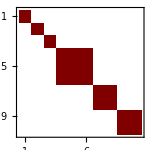

```mathematica
MatrixPlot[J.fieldMatrix4Const.J,ImageSize->150]
```

Evaluate Matsubara sum, either by hand or using some package, e.g., https://github.com/EverettYou/MatsubaraSum

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
threshΔNG=FullSimplify[MatsubaraSum[thresh[[1]]/.{q0->-I z},z∈Bosonic]]
```

-1/ENG^3 2 (n_B[-ENG-2 μ]-n_B[ENG-2 μ]+n_B[-ENG+2 μ]-n_B[ENG+2 μ]+ENG (n'_B[-ENG-2 μ]+n'_B[ENG-2 μ]+n'_B[-ENG+2 μ]+n'_B[ENG+2 μ])) U^(1,1)[σ^2,d^2]

```mathematica
thresh4π=FullSimplify[MatsubaraSum[FullSimplify[thresh[[2]]]/.{q0->-I z},z∈Bosonic]]
```

(5 (1+2 n_B[Eπ]-2 Eπ n'_B[Eπ]) U^(2,0)[σ^2,d^2])/Eπ^3

For the third term, which stems from the mixed σ/Δ part, we need to prepare the expression a little bit in order to determine the Matsubara sum

```mathematica
Simplify[thresh[[3]]]
```

(4 (16 d^2 (ENG^4-2 Eσ^2 q0^2-q0^4-2 EG^2 (Eσ^2+q0^2)+8 Eσ^2 μ^2-16 q0^2 μ^2+16 μ^4+2 ENG^2 (q0^2-4 μ^2)) σ^2 (U^(1,1)[σ^2,d^2])^3+256 d^4 σ^4 (U^(1,1)[σ^2,d^2])^5+2 d^2 (Eσ^2+q0^2)^2 (ENG^4+q0^4-24 q0^2 μ^2+16 μ^4+2 ENG^2 (q0^2-4 μ^2)) U^(1,2)[σ^2,d^2]+U^(1,1)[σ^2,d^2] ((Eσ^2+q0^2)^2 (EG^4+ENG^4+2 EG^2 (q0^2-4 μ^2)+2 ENG^2 (q0^2-4 μ^2)+2 (q0^4-24 q0^2 μ^2+16 μ^4))-16 d^2 (Eσ^2 q0^4+2 q0^6-24 Eσ^2 q0^2 μ^2-20 q0^4 μ^2+16 Eσ^2 μ^4-64 μ^6+EG^2 (ENG^2+q0^2-4 μ^2)^2+ENG^4 (Eσ^2+2 q0^2-4 μ^2)+2 ENG^2 (Eσ^2 (q0^2-4 μ^2)+2 (q0^4-2 q0^2 μ^2+8 μ^4))) σ^2 U^(2,1)[σ^2,d^2])+(ENG^2 (q0^2-4 μ^2)+EG^2 (ENG^2+q0^2-4 μ^2)+(q0^2+4 μ^2)^2)^2 (U^(2,0)[σ^2,d^2]+2 σ^2 U^(3,0)[σ^2,d^2])+16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2 (2 d^2 (ENG^2+q0^2-4 μ^2)^2 U^(1,2)[σ^2,d^2]+(ENG^4+q0^4-24 q0^2 μ^2+16 μ^4+2 ENG^2 (q0^2-4 μ^2)) (U^(2,0)[σ^2,d^2]+2 σ^2 U^(3,0)[σ^2,d^2]))))/((Eσ^2+q0^2) (ENG^2 (q0^2-4 μ^2)+EG^2 (ENG^2+q0^2-4 μ^2)+(q0^2+4 μ^2)^2)-16 d^2 (ENG^2+q0^2-4 μ^2) σ^2 (U^(1,1)[σ^2,d^2])^2)^2

Rearrange expression by sorting them with respect to orders of q_0^2

```mathematica
simplyfiedNum=Collect[Numerator[Together[thresh[[3]]]],q0];
simplyfiedDenom=Collect[Denominator[Together[thresh[[3]]]][[1]],q0];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
B3=Coefficient[simplyfiedDenom,q0,6];
B2=Coefficient[simplyfiedDenom,q0,4];
B1=Coefficient[simplyfiedDenom,q0,2];
B0=Coefficient[simplyfiedDenom,q0,0];
```

```mathematica
simplyfiedNum2=simplyfiedNum/.{A1->a1}/.{A0->a0}/.{A2->a2}/.{A3->a3}/.{A4->a4}
simplyfiedDenom2=simplyfiedDenom/.{B1->b1}/.{B0->b0}/.{B2->b2}/.{B3->b3}
```

a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8

b0+b1 q0^2+b2 q0^4+q0^6

Now the expression can be simplified to:

```mathematica
simplyfiedNum2/simplyfiedDenom2
```

(a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8)/(b0+b1 q0^2+b2 q0^4+q0^6)

Next, rearrange again in products of zeros

```mathematica
roots=Roots[simplyfiedDenom2==0,q0];
r1=Simplify[roots[[1,2]]];
r2=Simplify[roots[[3,2]]];
r3=Simplify[roots[[5,2]]];
```

```mathematica
simplyfiedDenom3=(R1^2+q0^2)(R2^2+q0^2)(R3^2+q0^2);
```

Note: Running the next line takes a long time (20 minutes or more)

```mathematica
Part3MatSum=FullSimplify[MatsubaraSum[simplyfiedNum2/(simplyfiedDenom3)^2/.{q0->-I z},z∈Bosonic]]
```

-((-(R1-R2)^3 (R1-R3)^3 (R2-R3)^3 (a0 (R2^2 R3^2 (R2+R3)^3+3 R1 R2 R3 (R2+R3)^4+R1^5 (R2^2+3 R2 R3+R3^2)+3 R1^4 (R2+R3) (R2^2+3 R2 R3+R3^2)+R1^2 (R2+R3)^3 (R2^2+9 R2 R3+R3^2)+R1^3 (3 R2^4+18 R2^3 R3+31 R2^2 R3^2+18 R2 R3^3+3 R3^4))+R1^2 R2^2 R3^2 (R1 R2 R3 (a2 R1^2+3 a2 R1 R2+a2 R2^2+a3 R1^2 R2^2+a4 R1^3 R2^3+3 (R1+R2) (a2+R1 R2 (a3+a4 R1 R2)) R3+(a2+a3 (R1^2+3 R1 R2+R2^2)+a4 R1 R2 (3 R1^2+7 R1 R2+3 R2^2)) R3^2+a4 (R1+R2)^3 R3^3)+a1 (R1^3+3 R1^2 (R2+R3)+(R2+R3)^3+R1 (3 R2^2+7 R2 R3+3 R3^2))))-2 R2^3 (R2-R3)^3 R3^3 (R2+R3)^3 (R1^6 (-7 a1+5 a2 R1^2-3 a3 R1^4+a4 R1^6)+R1^4 (3 a1-a2 R1^2-a3 R1^4+3 a4 R1^6) R2^2+R1^2 (3 a1 R1^2-R1^4 (a2+a3 R1^2-3 a4 R1^4)+(a1-3 a2 R1^2+5 a3 R1^4-7 a4 R1^6) R2^2) R3^2+a0 (9 R1^4+R2^2 R3^2-5 R1^2 (R2^2+R3^2))) n_B[R1]-2 R1^3 (R1-R3)^3 R3^3 (R1+R3)^3 (5 a0 R1^2 R2^2-3 (3 a0+a1 R1^2) R2^4+(7 a1+a2 R1^2) R2^6+(-5 a2+a3 R1^2) R2^8+3 (a3-a4 R1^2) R2^10-a4 R2^12+(-a0 R1^2+(5 a0-a1 R1^2) R2^2-3 (a1-a2 R1^2) R2^4+(a2-5 a3 R1^2) R2^6+(a3+7 a4 R1^2) R2^8-3 a4 R2^10) R3^2) n_B[R2]+2 R1 (R1-R2) R2 (R1+R2) (-R1^2 (R1-R2)^2 R2^2 (R1+R2)^2 (a0 R1^2 R2^2+(a1 R1^2 R2^2-5 a0 (R1^2+R2^2)) R3^2+3 (3 a0-a2 R1^2 R2^2+a1 (R1^2+R2^2)) R3^4-(7 a1-5 a3 R1^2 R2^2+a2 (R1^2+R2^2)) R3^6+(5 a2-7 a4 R1^2 R2^2-a3 (R1^2+R2^2)) R3^8+3 (-a3+a4 (R1^2+R2^2)) R3^10+a4 R3^12) n_B[R3]+(R1-R3) (R2-R3) R3 (R1+R3) (R2+R3) ((a0-a1 R1^2+a2 R1^4-a3 R1^6+a4 R1^8) R2^2 R3^2 (R2^2-R3^2)^2 n'_B[R1]+R1^2 ((a0-a1 R2^2+a2 R2^4-a3 R2^6+a4 R2^8) (-R1^2 R3+R3^3)^2 n'_B[R2]+(-R1^2 R2+R2^3)^2 (a0-a1 R3^2+a2 R3^4-a3 R3^6+a4 R3^8) n'_B[R3]))))/(4 R1^3 (R1-R2)^3 R2^3 (R1+R2)^3 (R1-R3)^3 (R2-R3)^3 R3^3 (R1+R3)^3 (R2+R3)^3))

#### A4σΔ Block Function

Define Block function for further use

```mathematica
nB[x_]:=1/(Exp[x/T]-1)
nBd[x_]:=-Csch[x/(2 T)]^2/(4 T)
```

```mathematica
A4σΔ[k_,ENG_,EG_,Eσ_,σ_,d_,Ti_,μi_,T_,μ_]:=Block[{R1,R2,R3,a0,a1,a2,a3,a4,b0,b1,b2,bVar},
b0=(ENG^2-4 μ^2) (Eσ^2 (EG^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2);
b1=ENG^2 Eσ^2-4 ENG^2 μ^2+8 Eσ^2 μ^2+16 μ^4+EG^2 (ENG^2+Eσ^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2;
b2=EG^2+ENG^2+Eσ^2+8 μ^2;
bVar=(-27 b0+9 b1 b2-2 b2^3+3 √3 √(27 b0^2+4 b1^3-18 b0 b1 b2-b1^2 b2^2+4 b0 b2^3));
a0=4 (16 d^2 (ENG^4-2 EG^2 Eσ^2-8 ENG^2 μ^2+8 μ^2 (Eσ^2+2 μ^2)) σ^2 Ukσd[k,σ,d,Ti,μi]^3+256 d^4 σ^4 Ukσd[k,σ,d,Ti,μi]^5+Ukσd[k,σ,d,Ti,μi] (Eσ^4 (EG^4+ENG^4-8 EG^2 μ^2-8 ENG^2 μ^2+32 μ^4)-16 d^2 (ENG^2-4 μ^2)^2 (EG^2+Eσ^2-4 μ^2) σ^2 Ukσσd[k,σ,d,Ti,μi])+16 d^2 (ENG^2-4 μ^2)^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2 (2 d^2 Ukσdd[k,σ,d,Ti,μi]+Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi])+(ENG^2-4 μ^2)^2 (2 d^2 Eσ^4 Ukσdd[k,σ,d,Ti,μi]+(EG^2-4 μ^2)^2 (Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi])));
a1=8 (-16 d^2 (EG^2-ENG^2+Eσ^2+8 μ^2) σ^2 Ukσd[k,σ,d,Ti,μi]^3+2 d^2 Eσ^2 (ENG^4-12 Eσ^2 μ^2+16 μ^4+ENG^2 (Eσ^2-8 μ^2)) Ukσdd[k,σ,d,Ti,μi]+Ukσd[k,σ,d,Ti,μi] (Eσ^2 (EG^4+ENG^4-24 Eσ^2 μ^2+32 μ^4+EG^2 (Eσ^2-8 μ^2)+ENG^2 (Eσ^2-8 μ^2))-16 d^2 (ENG^4-12 Eσ^2 μ^2+EG^2 (ENG^2-4 μ^2)+ENG^2 (Eσ^2-4 μ^2)) σ^2 Ukσσd[k,σ,d,Ti,μi])+(EG^2-4 μ^2) (ENG^2-4 μ^2) (EG^2+ENG^2+8 μ^2) (Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi])+16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2 (2 d^2 (ENG^2-4 μ^2) Ukσdd[k,σ,d,Ti,μi]+(ENG^2-12 μ^2) (Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi])));
a2=4 (-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^3+2 d^2 (ENG^4+Eσ^4-48 Eσ^2 μ^2+16 μ^4+4 ENG^2 (Eσ^2-2 μ^2)) Ukσdd[k,σ,d,Ti,μi]+Ukσd[k,σ,d,Ti,μi] (EG^4+ENG^4+4 ENG^2 Eσ^2+2 Eσ^4-8 ENG^2 μ^2-96 Eσ^2 μ^2+32 μ^4+4 EG^2 (Eσ^2-2 μ^2)-16 d^2 (EG^2+4 ENG^2+Eσ^2-20 μ^2) σ^2 Ukσσd[k,σ,d,Ti,μi])+(EG^4+ENG^4+8 ENG^2 μ^2+96 μ^4+4 EG^2 (ENG^2+2 μ^2)) (Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi])+16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2 (2 d^2 Ukσdd[k,σ,d,Ti,μi]+Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi]));
a3=8 (2 d^2 (ENG^2+Eσ^2-12 μ^2) Ukσdd[k,σ,d,Ti,μi]+Ukσd[k,σ,d,Ti,μi] (EG^2+ENG^2+2 Eσ^2-24 μ^2-16 d^2 σ^2 Ukσσd[k,σ,d,Ti,μi])+(EG^2+ENG^2+8 μ^2) (Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi]));
a4=4 (2 Ukσd[k,σ,d,Ti,μi]+2 d^2 Ukσdd[k,σ,d,Ti,μi]+Ukσσ[k,σ,d,Ti,μi]+2 σ^2 Ukσσσ[k,σ,d,Ti,μi]);
R1=I (√(-2 b2+(2 2^(1/3) (-3 b1+b2^2))/bVar^(1/3)+2^(2/3) bVar^(1/3)))/(√6);
R2=I (√(-2 b2+(2 (-2)^(1/3) (3 b1-b2^2))/bVar^(1/3)+(-2)^(2/3) bVar^(1/3)))/(√6);
R3=I √(-b2/3+((-1)^(2/3) 2^(1/3) (-3 b1+b2^2))/(3 bVar^(1/3))-1/3 (-1/2)^(1/3) bVar^(1/3));
-((-(R1-R2)^3 (R1-R3)^3 (R2-R3)^3 (a0 (R2^2 R3^2 (R2+R3)^3+3 R1 R2 R3 (R2+R3)^4+R1^5 (R2^2+3 R2 R3+R3^2)+3 R1^4 (R2+R3) (R2^2+3 R2 R3+R3^2)+R1^2 (R2+R3)^3 (R2^2+9 R2 R3+R3^2)+R1^3 (3 R2^4+18 R2^3 R3+31 R2^2 R3^2+18 R2 R3^3+3 R3^4))+R1^2 R2^2 R3^2 (R1 R2 R3 (a2 R1^2+3 a2 R1 R2+a2 R2^2+a3 R1^2 R2^2+a4 R1^3 R2^3+3 (R1+R2) (a2+R1 R2 (a3+a4 R1 R2)) R3+(a2+a3 (R1^2+3 R1 R2+R2^2)+a4 R1 R2 (3 R1^2+7 R1 R2+3 R2^2)) R3^2+a4 (R1+R2)^3 R3^3)+a1 (R1^3+3 R1^2 (R2+R3)+(R2+R3)^3+R1 (3 R2^2+7 R2 R3+3 R3^2))))-2 R2^3 (R2-R3)^3 R3^3 (R2+R3)^3 (R1^6 (-7 a1+5 a2 R1^2-3 a3 R1^4+a4 R1^6)+R1^4 (3 a1-a2 R1^2-a3 R1^4+3 a4 R1^6) R2^2+R1^2 (3 a1 R1^2-R1^4 (a2+a3 R1^2-3 a4 R1^4)+(a1-3 a2 R1^2+5 a3 R1^4-7 a4 R1^6) R2^2) R3^2+a0 (9 R1^4+R2^2 R3^2-5 R1^2 (R2^2+R3^2))) nB[R1]-2 R1^3 (R1-R3)^3 R3^3 (R1+R3)^3 (5 a0 R1^2 R2^2-3 (3 a0+a1 R1^2) R2^4+(7 a1+a2 R1^2) R2^6+(-5 a2+a3 R1^2) R2^8+3 (a3-a4 R1^2) R2^10-a4 R2^12+(-a0 R1^2+(5 a0-a1 R1^2) R2^2-3 (a1-a2 R1^2) R2^4+(a2-5 a3 R1^2) R2^6+(a3+7 a4 R1^2) R2^8-3 a4 R2^10) R3^2) nB[R2]+2 R1 (R1-R2) R2 (R1+R2) (-R1^2 (R1-R2)^2 R2^2 (R1+R2)^2 (a0 R1^2 R2^2+(a1 R1^2 R2^2-5 a0 (R1^2+R2^2)) R3^2+3 (3 a0-a2 R1^2 R2^2+a1 (R1^2+R2^2)) R3^4-(7 a1-5 a3 R1^2 R2^2+a2 (R1^2+R2^2)) R3^6+(5 a2-7 a4 R1^2 R2^2-a3 (R1^2+R2^2)) R3^8+3 (-a3+a4 (R1^2+R2^2)) R3^10+a4 R3^12) nB[R3]+(R1-R3) (R2-R3) R3 (R1+R3) (R2+R3) ((a0-a1 R1^2+a2 R1^4-a3 R1^6+a4 R1^8) R2^2 R3^2 (R2^2-R3^2)^2 nBd[R1]+R1^2 ((a0-a1 R2^2+a2 R2^4-a3 R2^6+a4 R2^8) (-R1^2 R3+R3^3)^2 nBd[R2]+(-R1^2 R2+R2^3)^2 (a0-a1 R3^2+a2 R3^4-a3 R3^6+a4 R3^8) nBd[R3]))))/(4 R1^3 (R1-R2)^3 R2^3 (R1+R2)^3 (R1-R3)^3 (R2-R3)^3 R3^3 (R1+R3)^3 (R2+R3)^3))
]
```

## Loop function contribution for two-point function

```mathematica
fractionExpand[expr_]:=Replace[Expand@expr,expr2_Plus:>(Together@*Plus@@@GatherBy[List@@expr2,Variables@*Denominator]//Total)]
(* Credit to: https://mathematica.stackexchange.com/questions/111984/collect-factor-a-fraction *)
```

For the loop function at external momentum, there are two possible cases: k^2>qv^2 (Jq1) or k^2<qv^2 (Jq2)

```mathematica
Jqp=(J/.{q^2->q0^2+(qv+pv)^2}/.{Rk->k^2-(qv+pv)^2});
Jq1=(J/.{q^2->q0^2+qv^2}/.{Rk->k^2-qv^2});
Jq2=(J/.{DNGAP->DNGAP2}/.{q^2->q0^2+qv^2}/.{Rk->0});
```

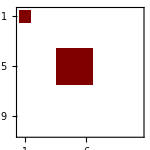

```mathematica
MatrixPlot[Jqp.fieldMatrix3Const.Jq1.fieldMatrix3Const.Jqp,ImageSize->150]
```

```mathematica
loop1=FullSimplify[Tr[Jqp.fieldMatrix3Const.Jq1.fieldMatrix3Const.Jqp]/.{k^2+mNoGap^2->ENG^2-4 μ^2,k^2+mGap^2->EG^2-4 μ^2,k^2+mπ^2->Eπ^2,k^2+mσ^2->Eσ^2}]
```

1/(DNGAP^2 (Eπ^2+q0^2)^2)16 (16 d^4 (Eπ^2+q0^2) (ENG^2+q0^2-4 μ^2)^2 σ^2 (U^(1,1)[σ^2,d^2])^4+((EG^2+q0^2) (ENG^2+q0^2)-4 (EG^2+ENG^2-2 q0^2) μ^2+16 μ^4) (DNGAP+(Eπ^2+q0^2) ((EG^2+q0^2) (ENG^2+q0^2)-4 (EG^2+ENG^2-2 q0^2) μ^2+16 μ^4)) σ^2 (U^(2,0)[σ^2,d^2])^2+d^2 (U^(1,1)[σ^2,d^2])^2 ((Eσ^2+q0^2) (DNGAP (ENG^2+q0^2-4 μ^2)+(Eπ^2+q0^2) (Eσ^2+q0^2) ((ENG^2+q0^2)^2-8 (ENG^2+3 q0^2) μ^2+16 μ^4))-8 σ^2 U^(2,0)[σ^2,d^2] (DNGAP (ENG^2+q0^2-4 μ^2)+(Eπ^2+q0^2) ((ENG^2+q0^2)^2 (EG^2+Eσ^2+2 q0^2)-4 (ENG^4+6 Eσ^2 q0^2+5 q0^4+2 EG^2 (ENG^2+q0^2)+2 ENG^2 (Eσ^2+q0^2)) μ^2+16 (EG^2+2 ENG^2+Eσ^2) μ^4-64 μ^6)-2 (Eπ^2+q0^2) (ENG^2+q0^2-4 q0 μ-4 μ^2) (ENG^2+q0^2+4 q0 μ-4 μ^2) σ^2 U^(2,0)[σ^2,d^2])))

```mathematica
loop2=FullSimplify[Tr[Jqp.fieldMatrix3Const.Jq2.fieldMatrix3Const.Jqp]/.{k^2+mNoGap^2->ENG^2-4 μ^2,k^2+mGap^2->EG^2-4 μ^2,k^2+mπ^2->Eπ^2,k^2+mσ^2->Eσ^2}/.{qv^2+mNoGap^2->ENGq^2-4 μ^2,qv^2+mGap^2->EGq^2-4 μ^2,qv^2+mπ^2->Eπq^2,qv^2+mσ^2->Eσq^2}]
```

(16 (16 d^4 DNGAP2 (Eπ^2+q0^2)^2 (ENG^2+q0^2-4 μ^2)^2 σ^2 (U^(1,1)[σ^2,d^2])^4+(DNGAP2 (Eπ^2+q0^2)^2 ((EG^2+q0^2) (ENG^2+q0^2)-4 (EG^2+ENG^2-2 q0^2) μ^2+16 μ^4)^2+DNGAP^2 (Eπq^2+q0^2) ((EGq^2+q0^2) (ENGq^2+q0^2)-4 (EGq^2+ENGq^2-2 q0^2) μ^2+16 μ^4)) σ^2 (U^(2,0)[σ^2,d^2])^2+d^2 (U^(1,1)[σ^2,d^2])^2 (DNGAP^2 (Eπq^2+q0^2) (Eσq^2+q0^2) (ENGq^2+q0^2-4 μ^2)+DNGAP2 (Eπ^2+q0^2)^2 (Eσ^2+q0^2)^2 ((ENG^2+q0^2)^2-8 (ENG^2+3 q0^2) μ^2+16 μ^4)-8 σ^2 U^(2,0)[σ^2,d^2] (DNGAP^2 (Eπq^2+q0^2) (ENGq^2+q0^2-4 μ^2)+DNGAP2 (Eπ^2+q0^2)^2 ((ENG^2+q0^2)^2 (EG^2+Eσ^2+2 q0^2)-4 (ENG^4+6 Eσ^2 q0^2+5 q0^4+2 EG^2 (ENG^2+q0^2)+2 ENG^2 (Eσ^2+q0^2)) μ^2+16 (EG^2+2 ENG^2+Eσ^2) μ^4-64 μ^6)-2 DNGAP2 (Eπ^2+q0^2)^2 (ENG^2+q0^2-4 q0 μ-4 μ^2) (ENG^2+q0^2+4 q0 μ-4 μ^2) σ^2 U^(2,0)[σ^2,d^2]))))/(DNGAP^2 DNGAP2 (Eπ^2+q0^2)^2 (Eπq^2+q0^2))

Splitting up loop2 makes things easier later on

```mathematica
loop2P1=Simplify[Collect[Numerator[loop2],DNGAP2][[1]]/Denominator[loop2]];
loop2P2=Simplify[Collect[Numerator[loop2],DNGAP2][[2]]/Denominator[loop2]];
```

```mathematica
Simplify[loop2P1+loop2P2==loop2]
```

True

#### loop 1:

```mathematica
Denominator[loop1]
```

DNGAP^2 (Eπ^2+q0^2)^2

We need to prepare the denominator a little bit in order to properly evaluate the Matsubara sum. The next steps may be a little bit confusing, but it should become clear in MatSum1 why we did these manipulations.

```mathematica
den=Simplify[(DNGAPV/.{q^2->q0^2+qv^2,Rk->k^2-qv^2})]
```

16 q0^2 (k^2+mσ^2+q0^2) μ^2+(k^2+mNoGap^2+q0^2) ((k^2+mGap^2+q0^2) (k^2+mσ^2+q0^2)-16 d^2 σ^2 (U^(1,1)[σ^2,d^2])^2)

```mathematica
simplyfiedNum=Collect[Numerator[Together[loop1]],q0];
simplyfiedDenom=Collect[den,q0];
A5=Coefficient[simplyfiedNum,q0,10];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
B3=Coefficient[simplyfiedDenom,q0,6];
B2=Coefficient[simplyfiedDenom,q0,4];
B1=Coefficient[simplyfiedDenom,q0,2];
B0=Coefficient[simplyfiedDenom,q0,0];
```

```mathematica
simplyfiedNum2=simplyfiedNum/.{A1->a1}/.{A0->a0}/.{A2->a2}/.{A3->a3}/.{A4->a4}/.{A5->a5}
simplyfiedDenom2=simplyfiedDenom/.{B1->b1}/.{B0->b0}/.{B2->b2}/.{B3->b3}
```

a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8+a5 q0^10

b0+b1 q0^2+b2 q0^4+q0^6

```mathematica
roots=Roots[simplyfiedDenom2==0,q0];
r1=Simplify[roots[[1,2]]];
r2=Simplify[roots[[3,2]]];
r3=Simplify[roots[[5,2]]];
```

```mathematica
simplyfiedDenom3=(R1^2+q0^2)(R2^2+q0^2)(R3^2+q0^2);
```

```mathematica
Simplify[simplyfiedDenom3/.{R1->I r1,R2->I r2,R3->I r3}]
```

b0+b1 q0^2+b2 q0^4+q0^6

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
MatSum1=MatsubaraSum[simplyfiedNum2/((Eπ^2+q0^2)^2 (simplyfiedDenom3)^2)/.{q0->-I z},z∈Bosonic];
```

Next line takes at least 20 minutes...

```mathematica
Simplify[MatSum1]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

1/8 ((2 ((a0 (-13 Eπ^6+R1^2 R2^2 R3^2+9 Eπ^4 (R1^2+R2^2+R3^2)-5 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))-a2 Eπ^4 (9 Eπ^6+3 R1^2 R2^2 R3^2-5 Eπ^4 (R1^2+R2^2+R3^2)+Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a1 Eπ^2 (11 Eπ^6+R1^2 R2^2 R3^2-7 Eπ^4 (R1^2+R2^2+R3^2)+3 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+Eπ^6 (a5 Eπ^4 (3 Eπ^6+9 R1^2 R2^2 R3^2+Eπ^4 (R1^2+R2^2+R3^2)-5 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a3 (7 Eπ^6+5 R1^2 R2^2 R3^2-3 Eπ^4 (R1^2+R2^2+R3^2)-Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a4 (-5 Eπ^8-7 Eπ^2 R1^2 R2^2 R3^2+Eπ^6 (R1^2+R2^2+R3^2)+3 Eπ^4 (R2^2 R3^2+R1^2 (R2^2+R3^2))))) n_B[-Eπ]+Eπ (-a0+Eπ^2 (a1-a2 Eπ^2+a3 Eπ^4-a4 Eπ^6+a5 Eπ^8)) (Eπ^2-R1^2) (Eπ^2-R2^2) (Eπ^2-R3^2) n'_B[-Eπ]))/(Eπ^3 (Eπ^2-R1^2)^3 (Eπ^2-R2^2)^3 (Eπ^2-R3^2)^3)-(2 ((a0 (-13 Eπ^6+R1^2 R2^2 R3^2+9 Eπ^4 (R1^2+R2^2+R3^2)-5 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))-a2 Eπ^4 (9 Eπ^6+3 R1^2 R2^2 R3^2-5 Eπ^4 (R1^2+R2^2+R3^2)+Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a1 Eπ^2 (11 Eπ^6+R1^2 R2^2 R3^2-7 Eπ^4 (R1^2+R2^2+R3^2)+3 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+Eπ^6 (a5 Eπ^4 (3 Eπ^6+9 R1^2 R2^2 R3^2+Eπ^4 (R1^2+R2^2+R3^2)-5 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a3 (7 Eπ^6+5 R1^2 R2^2 R3^2-3 Eπ^4 (R1^2+R2^2+R3^2)-Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a4 (-5 Eπ^8-7 Eπ^2 R1^2 R2^2 R3^2+Eπ^6 (R1^2+R2^2+R3^2)+3 Eπ^4 (R2^2 R3^2+R1^2 (R2^2+R3^2))))) n_B[Eπ]+Eπ (a0-Eπ^2 (a1-a2 Eπ^2+a3 Eπ^4-a4 Eπ^6+a5 Eπ^8)) (Eπ^2-R1^2) (Eπ^2-R2^2) (Eπ^2-R3^2) n'_B[Eπ]))/(Eπ^3 (Eπ^2-R1^2)^3 (Eπ^2-R2^2)^3 (Eπ^2-R3^2)^3)+(2 ((a0 (-13 R1^6-5 R1^2 R2^2 R3^2+9 R1^4 (R2^2+R3^2)+Eπ^2 (9 R1^4+R2^2 R3^2-5 R1^2 (R2^2+R3^2)))+R1^2 (a5 R1^8 (3 R1^6-5 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4+9 R2^2 R3^2-5 R1^2 (R2^2+R3^2)))+a2 R1^2 (-9 R1^6-R1^2 R2^2 R3^2+5 R1^4 (R2^2+R3^2)+Eπ^2 (5 R1^4-3 R2^2 R3^2-R1^2 (R2^2+R3^2)))-a3 R1^4 (-7 R1^6+R1^2 R2^2 R3^2+3 R1^4 (R2^2+R3^2)+Eπ^2 (3 R1^4-5 R2^2 R3^2+R1^2 (R2^2+R3^2)))+a4 R1^6 (-5 R1^6+3 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4-7 R2^2 R3^2+3 R1^2 (R2^2+R3^2)))+a1 (11 R1^6+3 R1^2 R2^2 R3^2-7 R1^4 (R2^2+R3^2)+Eπ^2 (-7 R1^4+R2^2 R3^2+3 R1^2 (R2^2+R3^2))))) n_B[-R1]+R1 (Eπ^2-R1^2) (a0-R1^2 (a1-a2 R1^2+a3 R1^4-a4 R1^6+a5 R1^8)) (R1^2-R2^2) (R1^2-R3^2) n'_B[-R1]))/(R1^3 (-Eπ^2+R1^2)^3 (R1^2-R2^2)^3 (R1^2-R3^2)^3)+(-2 (a0 (-13 R1^6-5 R1^2 R2^2 R3^2+9 R1^4 (R2^2+R3^2)+Eπ^2 (9 R1^4+R2^2 R3^2-5 R1^2 (R2^2+R3^2)))+R1^2 (a5 R1^8 (3 R1^6-5 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4+9 R2^2 R3^2-5 R1^2 (R2^2+R3^2)))+a2 R1^2 (-9 R1^6-R1^2 R2^2 R3^2+5 R1^4 (R2^2+R3^2)+Eπ^2 (5 R1^4-3 R2^2 R3^2-R1^2 (R2^2+R3^2)))-a3 R1^4 (-7 R1^6+R1^2 R2^2 R3^2+3 R1^4 (R2^2+R3^2)+Eπ^2 (3 R1^4-5 R2^2 R3^2+R1^2 (R2^2+R3^2)))+a4 R1^6 (-5 R1^6+3 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4-7 R2^2 R3^2+3 R1^2 (R2^2+R3^2)))+a1 (11 R1^6+3 R1^2 R2^2 R3^2-7 R1^4 (R2^2+R3^2)+Eπ^2 (-7 R1^4+R2^2 R3^2+3 R1^2 (R2^2+R3^2))))) n_B[R1]+2 R1 (Eπ^2-R1^2) (a0-R1^2 (a1-a2 R1^2+a3 R1^4-a4 R1^6+a5 R1^8)) (R1^2-R2^2) (R1^2-R3^2) n'_B[R1])/(R1^3 (-Eπ^2+R1^2)^3 (R1^2-R2^2)^3 (R1^2-R3^2)^3)+(2 ((a0 (-13 R2^6+9 R2^4 R3^2+R1^2 (9 R2^4-5 R2^2 R3^2)+Eπ^2 (9 R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+R3^2)))+R2^2 (a4 R2^6 (-5 R2^6+R2^4 R3^2+R1^2 (R2^4+3 R2^2 R3^2)+Eπ^2 (R2^4+3 R2^2 R3^2+R1^2 (3 R2^2-7 R3^2)))+a1 (11 R2^6-7 R2^4 R3^2+R1^2 (-7 R2^4+3 R2^2 R3^2)+Eπ^2 (-7 R2^4+3 R2^2 R3^2+R1^2 (3 R2^2+R3^2)))-a3 R2^4 (-7 R2^6+3 R2^4 R3^2+R1^2 R2^2 (3 R2^2+R3^2)+Eπ^2 (R1^2 (R2^2-5 R3^2)+R2^2 (3 R2^2+R3^2)))-a2 R2^2 (9 R2^6-5 R2^4 R3^2+R1^2 (-5 R2^4+R2^2 R3^2)+Eπ^2 (-5 R2^4+R2^2 R3^2+R1^2 (R2^2+3 R3^2)))+a5 R2^8 (R2^4 (3 R2^2+R3^2)+R1^2 (R2^4-5 R2^2 R3^2)+Eπ^2 (R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+9 R3^2))))) n_B[-R2]+R2 (-Eπ^2+R2^2) (-R1^2+R2^2) (-a0+R2^2 (a1-a2 R2^2+a3 R2^4-a4 R2^6+a5 R2^8)) (R2^2-R3^2) n'_B[-R2]))/(R2^3 (-Eπ^2+R2^2)^3 (-R1^2+R2^2)^3 (R2^2-R3^2)^3)-(2 ((a0 (-13 R2^6+9 R2^4 R3^2+R1^2 (9 R2^4-5 R2^2 R3^2)+Eπ^2 (9 R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+R3^2)))+R2^2 (a4 R2^6 (-5 R2^6+R2^4 R3^2+R1^2 (R2^4+3 R2^2 R3^2)+Eπ^2 (R2^4+3 R2^2 R3^2+R1^2 (3 R2^2-7 R3^2)))+a1 (11 R2^6-7 R2^4 R3^2+R1^2 (-7 R2^4+3 R2^2 R3^2)+Eπ^2 (-7 R2^4+3 R2^2 R3^2+R1^2 (3 R2^2+R3^2)))-a3 R2^4 (-7 R2^6+3 R2^4 R3^2+R1^2 R2^2 (3 R2^2+R3^2)+Eπ^2 (R1^2 (R2^2-5 R3^2)+R2^2 (3 R2^2+R3^2)))-a2 R2^2 (9 R2^6-5 R2^4 R3^2+R1^2 (-5 R2^4+R2^2 R3^2)+Eπ^2 (-5 R2^4+R2^2 R3^2+R1^2 (R2^2+3 R3^2)))+a5 R2^8 (R2^4 (3 R2^2+R3^2)+R1^2 (R2^4-5 R2^2 R3^2)+Eπ^2 (R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+9 R3^2))))) n_B[R2]+R2 (Eπ^2-R2^2) (R1^2-R2^2) (a0-R2^2 (a1-a2 R2^2+a3 R2^4-a4 R2^6+a5 R2^8)) (R2^2-R3^2) n'_B[R2]))/(R2^3 (-Eπ^2+R2^2)^3 (-R1^2+R2^2)^3 (R2^2-R3^2)^3)+(2 ((a0 (9 R2^2 R3^4-13 R3^6+R1^2 (-5 R2^2 R3^2+9 R3^4)+Eπ^2 (-5 R2^2 R3^2+9 R3^4+R1^2 (R2^2-5 R3^2)))-a2 R3^4 (-5 R2^2 R3^4+9 R3^6+R1^2 R3^2 (R2^2-5 R3^2)+Eπ^2 (R3^2 (R2^2-5 R3^2)+R1^2 (3 R2^2+R3^2)))+a1 R3^2 (-7 R2^2 R3^4+11 R3^6+R1^2 (3 R2^2 R3^2-7 R3^4)+Eπ^2 (3 R2^2 R3^2-7 R3^4+R1^2 (R2^2+3 R3^2)))+R3^6 (a5 R3^4 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4)+Eπ^2 (-5 R2^2 R3^2+R3^4+R1^2 (9 R2^2-5 R3^2)))+a3 (-3 R2^2 R3^4+7 R3^6-R1^2 R3^2 (R2^2+3 R3^2)+Eπ^2 (R1^2 (5 R2^2-R3^2)-R3^2 (R2^2+3 R3^2)))+a4 (R3^6 (R2^2-5 R3^2)+R1^2 (3 R2^2 R3^4+R3^6)+Eπ^2 (3 R2^2 R3^4+R3^6+R1^2 (-7 R2^2 R3^2+3 R3^4))))) n_B[-R3]+R3 (Eπ^2-R3^2) (R1^2-R3^2) (R2^2-R3^2) (a0-R3^2 (a1-a2 R3^2+a3 R3^4-a4 R3^6+a5 R3^8)) n'_B[-R3]))/(R3^3 (-Eπ^2+R3^2)^3 (-R1^2+R3^2)^3 (-R2^2+R3^2)^3)+(-2 (a0 (9 R2^2 R3^4-13 R3^6+R1^2 (-5 R2^2 R3^2+9 R3^4)+Eπ^2 (-5 R2^2 R3^2+9 R3^4+R1^2 (R2^2-5 R3^2)))-a2 R3^4 (-5 R2^2 R3^4+9 R3^6+R1^2 R3^2 (R2^2-5 R3^2)+Eπ^2 (R3^2 (R2^2-5 R3^2)+R1^2 (3 R2^2+R3^2)))+a1 R3^2 (-7 R2^2 R3^4+11 R3^6+R1^2 (3 R2^2 R3^2-7 R3^4)+Eπ^2 (3 R2^2 R3^2-7 R3^4+R1^2 (R2^2+3 R3^2)))+R3^6 (a5 R3^4 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4)+Eπ^2 (-5 R2^2 R3^2+R3^4+R1^2 (9 R2^2-5 R3^2)))+a3 (-3 R2^2 R3^4+7 R3^6-R1^2 R3^2 (R2^2+3 R3^2)+Eπ^2 (R1^2 (5 R2^2-R3^2)-R3^2 (R2^2+3 R3^2)))+a4 (R3^6 (R2^2-5 R3^2)+R1^2 (3 R2^2 R3^4+R3^6)+Eπ^2 (3 R2^2 R3^4+R3^6+R1^2 (-7 R2^2 R3^2+3 R3^4))))) n_B[R3]+2 R3 (Eπ^2-R3^2) (R1^2-R3^2) (R2^2-R3^2) (a0-R3^2 (a1-a2 R3^2+a3 R3^4-a4 R3^6+a5 R3^8)) n'_B[R3])/(R3^3 (-Eπ^2+R3^2)^3 (-R1^2+R3^2)^3 (-R2^2+R3^2)^3))

#### Three point contribution Part 1 Block Function

```mathematica
Γ3P1[k_,ENG_,Eπ_,EG_,Eσ_,σ_,d_,Ti_,μi_,T_,μ_]:=Block[{R1,R2,R3,a0,a1,a2,a3,a4,a5,b0,b1,b2,bVar,R123,R12p3,R1p2p3},
b0=(ENG^2-4 μ^2) (Eσ^2 (EG^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2);
b1=ENG^2 Eσ^2-4 ENG^2 μ^2+8 Eσ^2 μ^2+16 μ^4+EG^2 (ENG^2+Eσ^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2;
b2=EG^2+ENG^2+Eσ^2+8 μ^2;
bVar=(-27 b0+9 b1 b2-2 b2^3+3 √3 √(27 b0^2+4 b1^3-18 b0 b1 b2-b1^2 b2^2+4 b0 b2^3));
a0=16 (ENG^2-4 μ^2)^2 ((Eπ^2+Eσ^2) (EG^2-4 μ^2)^2 σ^2 Ukσσ[k,σ,d,Ti,μi]^2+16 d^4 σ^2 Ukσd[k,σ,d,Ti,μi]^4 (Eπ^2-Eσ^2+8 σ^2 Ukσσ[k,σ,d,Ti,μi])+d^2 Ukσd[k,σ,d,Ti,μi]^2 (Eσ^4 (EG^2+Eπ^2-4 μ^2)-8 σ^2 Ukσσ[k,σ,d,Ti,μi] (Eπ^2 Eσ^2+EG^2 (Eπ^2+Eσ^2)-4 (Eπ^2+Eσ^2) μ^2+2 (EG^2-Eπ^2-4 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi])));
a1=32 ((EG^2-4 μ^2) (ENG^2-4 μ^2) (ENG^2 (Eπ^2+Eσ^2-4 μ^2)+EG^2 (ENG^2+Eπ^2+Eσ^2-4 μ^2)+8 μ^2 (Eπ^2+Eσ^2+2 μ^2)) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+16 d^4 (ENG^2-4 μ^2) σ^2 Ukσd[k,σ,d,Ti,μi]^4 (Eπ^2-Eσ^2+8 σ^2 Ukσσ[k,σ,d,Ti,μi])+d^2 Ukσd[k,σ,d,Ti,μi]^2 (Eσ^2 (-64 μ^6+ENG^2 (Eσ^2-8 μ^2) (Eπ^2-4 μ^2)+EG^2 (ENG^2-4 μ^2) (ENG^2+Eσ^2-4 μ^2)+ENG^4 (Eπ^2+Eσ^2-4 μ^2)+4 Eπ^2 μ^2 (-3 Eσ^2+4 μ^2))-8 (ENG^4 (Eπ^2+Eσ^2-4 μ^2)+EG^2 (ENG^2-4 μ^2) (ENG^2+Eπ^2+Eσ^2-4 μ^2)-4 μ^2 (3 Eπ^2 Eσ^2+16 μ^4)+ENG^2 (-4 μ^2 (Eσ^2-8 μ^2)+Eπ^2 (Eσ^2-4 μ^2))) σ^2 Ukσσ[k,σ,d,Ti,μi]-16 (EG^2 (ENG^2-4 μ^2)-ENG^2 (Eπ^2-4 μ^2)+4 μ^2 (3 Eπ^2-4 μ^2)) σ^4 Ukσσ[k,σ,d,Ti,μi]^2));
a2=16 ((ENG^4 (Eπ^2+Eσ^2-16 μ^2)+EG^4 (4 ENG^2+Eπ^2+Eσ^2-16 μ^2)+8 ENG^2 μ^2 (Eπ^2+Eσ^2-8 μ^2)+32 μ^4 (3 Eπ^2+3 Eσ^2+16 μ^2)+4 EG^2 (ENG^4+ENG^2 (Eπ^2+Eσ^2)+2 μ^2 (Eπ^2+Eσ^2-8 μ^2))) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+16 d^4 σ^2 Ukσd[k,σ,d,Ti,μi]^4 (Eπ^2-Eσ^2+8 σ^2 Ukσσ[k,σ,d,Ti,μi])+d^2 Ukσd[k,σ,d,Ti,μi]^2 (ENG^4 Eπ^2+4 ENG^4 Eσ^2+4 ENG^2 Eπ^2 Eσ^2+4 ENG^2 Eσ^4+Eπ^2 Eσ^4-4 ENG^4 μ^2-8 ENG^2 Eπ^2 μ^2-16 ENG^2 Eσ^2 μ^2-48 Eπ^2 Eσ^2 μ^2-20 Eσ^4 μ^2+32 ENG^2 μ^4+16 Eπ^2 μ^4-64 μ^6+EG^2 (ENG^4+Eσ^4-16 Eσ^2 μ^2+16 μ^4+4 ENG^2 (Eσ^2-2 μ^2))-8 (3 ENG^4+Eπ^2 Eσ^2-20 Eπ^2 μ^2-20 Eσ^2 μ^2-16 μ^4+EG^2 (4 ENG^2+Eπ^2+Eσ^2-16 μ^2)+4 ENG^2 (Eπ^2+Eσ^2-2 μ^2)) σ^2 Ukσσ[k,σ,d,Ti,μi]-16 (EG^2-Eπ^2+28 μ^2) σ^4 Ukσσ[k,σ,d,Ti,μi]^2));
a3=32 ((EG^4+ENG^4+ENG^2 (Eπ^2+Eσ^2+8 μ^2)+EG^2 (4 ENG^2+Eπ^2+Eσ^2+8 μ^2)+8 μ^2 (Eπ^2+Eσ^2+12 μ^2)) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (ENG^4+ENG^2 Eπ^2+4 ENG^2 Eσ^2+Eπ^2 Eσ^2+Eσ^4-4 ENG^2 μ^2-12 Eπ^2 μ^2-20 Eσ^2 μ^2+EG^2 (ENG^2+Eσ^2-4 μ^2)-8 (EG^2+3 ENG^2+Eπ^2+Eσ^2-8 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]));
a4=16 ((4 EG^2+4 ENG^2+Eπ^2+Eσ^2+32 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (EG^2+4 ENG^2+Eπ^2+4 Eσ^2-20 μ^2-24 σ^2 Ukσσ[k,σ,d,Ti,μi]));
a5=32 (d^2 Ukσd[k,σ,d,Ti,μi]^2+σ^2 Ukσσ[k,σ,d,Ti,μi]^2);
R1=I (√(-2 b2+(2 2^(1/3) (-3 b1+b2^2))/bVar^(1/3)+2^(2/3) bVar^(1/3)))/(√6);
R2=I (√(-2 b2+(2 (-2)^(1/3) (3 b1-b2^2))/bVar^(1/3)+(-2)^(2/3) bVar^(1/3)))/(√6);
R3=I √(-b2/3+((-1)^(2/3) 2^(1/3) (-3 b1+b2^2))/(3 bVar^(1/3))-1/3 (-1/2)^(1/3) bVar^(1/3));
R123=R1^2 R2^2 R3^2;
R1p2p3=R1^2+R2^2+R3^2;
R12p3=R1^2 (R2^2+R3^2);
1/8 ((2 ((a0 (-13 Eπ^6+R123+9 Eπ^4 R1p2p3-5 Eπ^2 (R2^2 R3^2+R12p3))-a2 Eπ^4 (9 Eπ^6+3 R123-5 Eπ^4 R1p2p3+Eπ^2 (R2^2 R3^2+R12p3))+a1 Eπ^2 (11 Eπ^6+R123-7 Eπ^4 R1p2p3+3 Eπ^2 (R2^2 R3^2+R12p3))+Eπ^6 (a5 Eπ^4 (3 Eπ^6+9 R123+Eπ^4 R1p2p3-5 Eπ^2 (R2^2 R3^2+R12p3))+a3 (7 Eπ^6+5 R123-3 Eπ^4 R1p2p3-Eπ^2 (R2^2 R3^2+R12p3))+a4 (-5 Eπ^8-7 Eπ^2 R123+Eπ^6 R1p2p3+3 Eπ^4 (R2^2 R3^2+R12p3)))) nB[-Eπ,T]+Eπ (-a0+Eπ^2 (a1-a2 Eπ^2+a3 Eπ^4-a4 Eπ^6+a5 Eπ^8)) (Eπ^2-R1^2) (Eπ^2-R2^2) (Eπ^2-R3^2) nBd[-Eπ,T]))/(Eπ^3 (Eπ^2-R1^2)^3 (Eπ^2-R2^2)^3 (Eπ^2-R3^2)^3)-(2 ((a0 (-13 Eπ^6+R123+9 Eπ^4 R1p2p3-5 Eπ^2 (R2^2 R3^2+R12p3))-a2 Eπ^4 (9 Eπ^6+3 R123-5 Eπ^4 R1p2p3+Eπ^2 (R2^2 R3^2+R12p3))+a1 Eπ^2 (11 Eπ^6+R123-7 Eπ^4 R1p2p3+3 Eπ^2 (R2^2 R3^2+R12p3))+Eπ^6 (a5 Eπ^4 (3 Eπ^6+9 R123+Eπ^4 R1p2p3-5 Eπ^2 (R2^2 R3^2+R12p3))+a3 (7 Eπ^6+5 R123-3 Eπ^4 R1p2p3-Eπ^2 (R2^2 R3^2+R12p3))+a4 (-5 Eπ^8-7 Eπ^2 R123+Eπ^6 R1p2p3+3 Eπ^4 (R2^2 R3^2+R12p3)))) nB[Eπ,T]+Eπ (a0-Eπ^2 (a1-a2 Eπ^2+a3 Eπ^4-a4 Eπ^6+a5 Eπ^8)) (Eπ^2-R1^2) (Eπ^2-R2^2) (Eπ^2-R3^2) nBd[Eπ,T]))/(Eπ^3 (Eπ^2-R1^2)^3 (Eπ^2-R2^2)^3 (Eπ^2-R3^2)^3)+(2 ((a0 (-13 R1^6-5 R123+9 R1^4 (R2^2+R3^2)+Eπ^2 (9 R1^4+R2^2 R3^2-5 R12p3))+R1^2 (a5 R1^8 (3 R1^6-5 R123+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4+9 R2^2 R3^2-5 R12p3))+a2 R1^2 (-9 R1^6-R123+5 R1^4 (R2^2+R3^2)+Eπ^2 (5 R1^4-3 R2^2 R3^2-R12p3))-a3 R1^4 (-7 R1^6+R123+3 R1^4 (R2^2+R3^2)+Eπ^2 (3 R1^4-5 R2^2 R3^2+R12p3))+a4 R1^6 (-5 R1^6+3 R123+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4-7 R2^2 R3^2+3 R12p3))+a1 (11 R1^6+3 R123-7 R1^4 (R2^2+R3^2)+Eπ^2 (-7 R1^4+R2^2 R3^2+3 R12p3)))) nB[-R1,T]+R1 (Eπ^2-R1^2) (a0-R1^2 (a1-a2 R1^2+a3 R1^4-a4 R1^6+a5 R1^8)) (R1^2-R2^2) (R1^2-R3^2) nBd[-R1,T]))/(R1^3 (-Eπ^2+R1^2)^3 (R1^2-R2^2)^3 (R1^2-R3^2)^3)+(-2 (a0 (-13 R1^6-5 R123+9 R1^4 (R2^2+R3^2)+Eπ^2 (9 R1^4+R2^2 R3^2-5 R12p3))+R1^2 (a5 R1^8 (3 R1^6-5 R123+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4+9 R2^2 R3^2-5 R12p3))+a2 R1^2 (-9 R1^6-R123+5 R1^4 (R2^2+R3^2)+Eπ^2 (5 R1^4-3 R2^2 R3^2-R12p3))-a3 R1^4 (-7 R1^6+R123+3 R1^4 (R2^2+R3^2)+Eπ^2 (3 R1^4-5 R2^2 R3^2+R12p3))+a4 R1^6 (-5 R1^6+3 R123+R1^4 (R2^2+R3^2)+Eπ^2 (R1^4-7 R2^2 R3^2+3 R12p3))+a1 (11 R1^6+3 R123-7 R1^4 (R2^2+R3^2)+Eπ^2 (-7 R1^4+R2^2 R3^2+3 R12p3)))) nB[R1,T]+2 R1 (Eπ^2-R1^2) (a0-R1^2 (a1-a2 R1^2+a3 R1^4-a4 R1^6+a5 R1^8)) (R1^2-R2^2) (R1^2-R3^2) nBd[R1,T])/(R1^3 (-Eπ^2+R1^2)^3 (R1^2-R2^2)^3 (R1^2-R3^2)^3)+(2 ((a0 (-13 R2^6+9 R2^4 R3^2+R1^2 (9 R2^4-5 R2^2 R3^2)+Eπ^2 (9 R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+R3^2)))+R2^2 (a4 R2^6 (-5 R2^6+R2^4 R3^2+R1^2 (R2^4+3 R2^2 R3^2)+Eπ^2 (R2^4+3 R2^2 R3^2+R1^2 (3 R2^2-7 R3^2)))+a1 (11 R2^6-7 R2^4 R3^2+R1^2 (-7 R2^4+3 R2^2 R3^2)+Eπ^2 (-7 R2^4+3 R2^2 R3^2+R1^2 (3 R2^2+R3^2)))-a3 R2^4 (-7 R2^6+3 R2^4 R3^2+R1^2 R2^2 (3 R2^2+R3^2)+Eπ^2 (R1^2 (R2^2-5 R3^2)+R2^2 (3 R2^2+R3^2)))-a2 R2^2 (9 R2^6-5 R2^4 R3^2+R1^2 (-5 R2^4+R2^2 R3^2)+Eπ^2 (-5 R2^4+R2^2 R3^2+R1^2 (R2^2+3 R3^2)))+a5 R2^8 (R2^4 (3 R2^2+R3^2)+R1^2 (R2^4-5 R2^2 R3^2)+Eπ^2 (R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+9 R3^2))))) nB[-R2,T]+R2 (-Eπ^2+R2^2) (-R1^2+R2^2) (-a0+R2^2 (a1-a2 R2^2+a3 R2^4-a4 R2^6+a5 R2^8)) (R2^2-R3^2) nBd[-R2,T]))/(R2^3 (-Eπ^2+R2^2)^3 (-R1^2+R2^2)^3 (R2^2-R3^2)^3)-(2 ((a0 (-13 R2^6+9 R2^4 R3^2+R1^2 (9 R2^4-5 R2^2 R3^2)+Eπ^2 (9 R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+R3^2)))+R2^2 (a4 R2^6 (-5 R2^6+R2^4 R3^2+R1^2 (R2^4+3 R2^2 R3^2)+Eπ^2 (R2^4+3 R2^2 R3^2+R1^2 (3 R2^2-7 R3^2)))+a1 (11 R2^6-7 R2^4 R3^2+R1^2 (-7 R2^4+3 R2^2 R3^2)+Eπ^2 (-7 R2^4+3 R2^2 R3^2+R1^2 (3 R2^2+R3^2)))-a3 R2^4 (-7 R2^6+3 R2^4 R3^2+R1^2 R2^2 (3 R2^2+R3^2)+Eπ^2 (R1^2 (R2^2-5 R3^2)+R2^2 (3 R2^2+R3^2)))-a2 R2^2 (9 R2^6-5 R2^4 R3^2+R1^2 (-5 R2^4+R2^2 R3^2)+Eπ^2 (-5 R2^4+R2^2 R3^2+R1^2 (R2^2+3 R3^2)))+a5 R2^8 (R2^4 (3 R2^2+R3^2)+R1^2 (R2^4-5 R2^2 R3^2)+Eπ^2 (R2^4-5 R2^2 R3^2+R1^2 (-5 R2^2+9 R3^2))))) nB[R2,T]+R2 (Eπ^2-R2^2) (R1^2-R2^2) (a0-R2^2 (a1-a2 R2^2+a3 R2^4-a4 R2^6+a5 R2^8)) (R2^2-R3^2) nBd[R2,T]))/(R2^3 (-Eπ^2+R2^2)^3 (-R1^2+R2^2)^3 (R2^2-R3^2)^3)+(2 ((a0 (9 R2^2 R3^4-13 R3^6+R1^2 (-5 R2^2 R3^2+9 R3^4)+Eπ^2 (-5 R2^2 R3^2+9 R3^4+R1^2 (R2^2-5 R3^2)))-a2 R3^4 (-5 R2^2 R3^4+9 R3^6+R1^2 R3^2 (R2^2-5 R3^2)+Eπ^2 (R3^2 (R2^2-5 R3^2)+R1^2 (3 R2^2+R3^2)))+a1 R3^2 (-7 R2^2 R3^4+11 R3^6+R1^2 (3 R2^2 R3^2-7 R3^4)+Eπ^2 (3 R2^2 R3^2-7 R3^4+R1^2 (R2^2+3 R3^2)))+R3^6 (a5 R3^4 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4)+Eπ^2 (-5 R2^2 R3^2+R3^4+R1^2 (9 R2^2-5 R3^2)))+a3 (-3 R2^2 R3^4+7 R3^6-R1^2 R3^2 (R2^2+3 R3^2)+Eπ^2 (R1^2 (5 R2^2-R3^2)-R3^2 (R2^2+3 R3^2)))+a4 (R3^6 (R2^2-5 R3^2)+R1^2 (3 R2^2 R3^4+R3^6)+Eπ^2 (3 R2^2 R3^4+R3^6+R1^2 (-7 R2^2 R3^2+3 R3^4))))) nB[-R3,T]+R3 (Eπ^2-R3^2) (R1^2-R3^2) (R2^2-R3^2) (a0-R3^2 (a1-a2 R3^2+a3 R3^4-a4 R3^6+a5 R3^8)) nBd[-R3,T]))/(R3^3 (-Eπ^2+R3^2)^3 (-R1^2+R3^2)^3 (-R2^2+R3^2)^3)+(-2 (a0 (9 R2^2 R3^4-13 R3^6+R1^2 (-5 R2^2 R3^2+9 R3^4)+Eπ^2 (-5 R2^2 R3^2+9 R3^4+R1^2 (R2^2-5 R3^2)))-a2 R3^4 (-5 R2^2 R3^4+9 R3^6+R1^2 R3^2 (R2^2-5 R3^2)+Eπ^2 (R3^2 (R2^2-5 R3^2)+R1^2 (3 R2^2+R3^2)))+a1 R3^2 (-7 R2^2 R3^4+11 R3^6+R1^2 (3 R2^2 R3^2-7 R3^4)+Eπ^2 (3 R2^2 R3^2-7 R3^4+R1^2 (R2^2+3 R3^2)))+R3^6 (a5 R3^4 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4)+Eπ^2 (-5 R2^2 R3^2+R3^4+R1^2 (9 R2^2-5 R3^2)))+a3 (-3 R2^2 R3^4+7 R3^6-R1^2 R3^2 (R2^2+3 R3^2)+Eπ^2 (R1^2 (5 R2^2-R3^2)-R3^2 (R2^2+3 R3^2)))+a4 (R3^6 (R2^2-5 R3^2)+R1^2 (3 R2^2 R3^4+R3^6)+Eπ^2 (3 R2^2 R3^4+R3^6+R1^2 (-7 R2^2 R3^2+3 R3^4)))))nB[R3,T]+2 R3 (Eπ^2-R3^2) (R1^2-R3^2) (R2^2-R3^2) (a0-R3^2 (a1-a2 R3^2+a3 R3^4-a4 R3^6+a5 R3^8)) nBd[R3,T])/(R3^3 (-Eπ^2+R3^2)^3 (-R1^2+R3^2)^3 (-R2^2+R3^2)^3))
]
```

#### loop2:

Part 1

```mathematica
Denominator[loop2P1]
```

DNGAP2 (Eπ^2+q0^2)^2

```mathematica
denP1=FullSimplify[(DNGAPV/.{q^2->q0^2+qv^2,Rk->0})](*DNGAP2*)
```

(mσ^2+q0^2+qv^2) ((mGap^2+q0^2+qv^2) (mNoGap^2+q0^2+qv^2)+16 q0^2 μ^2)-16 d^2 (mNoGap^2+q0^2+qv^2) σ^2 (U^(1,1)[σ^2,d^2])^2

```mathematica
simplyfiedNumP1=Collect[Numerator[Together[loop2P1/.{DNGAP2->(DNGAPV/.{Rk->0})}]],q0];
simplyfiedDenomP1=Collect[denP1,q0];
A5P1=Coefficient[simplyfiedNumP1,q0,10];
A4P1=Coefficient[simplyfiedNumP1,q0,8];
A3P1=Coefficient[simplyfiedNumP1,q0,6];
A2P1=Coefficient[simplyfiedNumP1,q0,4];
A1P1=Coefficient[simplyfiedNumP1,q0,2];
A0P1=Coefficient[simplyfiedNumP1,q0,0];
B3P1=Coefficient[simplyfiedDenomP1,q0,6];
B2P1=Coefficient[simplyfiedDenomP1,q0,4];
B1P1=Coefficient[simplyfiedDenomP1,q0,2];
B0P1=Coefficient[simplyfiedDenomP1,q0,0];
```

```mathematica
simplyfiedNumP12=simplyfiedNumP1/.{A1P1->a1P1}/.{A0P1->a0P1}/.{A2P1->a2P1}/.{A3P1->a3P1}/.{A4P1->a4P1}/.{A5P1->a5P1}
simplyfiedDenomP12=simplyfiedDenomP1/.{B1P1->b1P1}/.{B0P1->b0P1}/.{B2P1->b2P1}/.{B3P1->b3P1}
```

a0P1+a1P1 q0^2+a2P1 q0^4

b0P1+b1P1 q0^2+b2P1 q0^4+q0^6

```mathematica
roots=Roots[simplyfiedDenomP12==0,q0];
r1P1=Simplify[roots[[1,2]]];
r2P1=Simplify[roots[[3,2]]];
r3P1=Simplify[roots[[5,2]]];
```

```mathematica
simplyfiedDenomP13=(R1P1^2+q0^2)(R2P1^2+q0^2)(R3P1^2+q0^2);
```

```mathematica
Simplify[simplyfiedDenomP13/.{R1P1->I r1P1,R2P1->I r2P1,R3P1->I r3P1}]
```

b0P1+b1P1 q0^2+b2P1 q0^4+q0^6

Part 2

```mathematica
Denominator[loop2P2]
```

DNGAP^2 (Eπq^2+q0^2)

```mathematica
denP2=FullSimplify[(DNGAPV/.{q^2->q0^2+qv^2,Rk->k^2-qv^2})](*DNGAP*)
```

(k^2+mσ^2+q0^2) ((k^2+mGap^2+q0^2) (k^2+mNoGap^2+q0^2)+16 q0^2 μ^2)-16 d^2 (k^2+mNoGap^2+q0^2) σ^2 (U^(1,1)[σ^2,d^2])^2

```mathematica
simplyfiedNumP2=Collect[Numerator[Together[loop2P2]],q0];
simplyfiedDenomP2=Collect[denP2,q0];
A7P2=Coefficient[simplyfiedNumP2,q0,14];
A6P2=Coefficient[simplyfiedNumP2,q0,12];
A5P2=Coefficient[simplyfiedNumP2,q0,10];
A4P2=Coefficient[simplyfiedNumP2,q0,8];
A3P2=Coefficient[simplyfiedNumP2,q0,6];
A2P2=Coefficient[simplyfiedNumP2,q0,4];
A1P2=Coefficient[simplyfiedNumP2,q0,2];
A0P2=Coefficient[simplyfiedNumP2,q0,0];
B3P2=Coefficient[simplyfiedDenomP2,q0,6];
B2P2=Coefficient[simplyfiedDenomP2,q0,4];
B1P2=Coefficient[simplyfiedDenomP2,q0,2];
B0P2=Coefficient[simplyfiedDenomP2,q0,0];
```

```mathematica
simplyfiedNumP22=simplyfiedNumP2/.{A1P2->a1P2}/.{A0P2->a0P2}/.{A2P2->a2P2}/.{A3P2->a3P2}/.{A4P2->a4P2}/.{A5P2->a5P2}/.{A6P2->a6P2}/.{A7P2->a7P2}
simplyfiedDenomP22=simplyfiedDenomP2/.{B1P2->b1P2}/.{B0P2->b0P2}/.{B2P2->b2P2}/.{B3P2->b3P2}
```

a0P2+a1P2 q0^2+a2P2 q0^4+a3P2 q0^6+a4P2 q0^8

b0P2+b1P2 q0^2+b2P2 q0^4+q0^6

```mathematica
roots=Roots[simplyfiedDenomP22==0,q0];
r1P2=Simplify[roots[[1,2]]];
r2P2=Simplify[roots[[3,2]]];
r3P2=Simplify[roots[[5,2]]];
```

```mathematica
simplyfiedDenomP23=(R1P2^2+q0^2)(R2P2^2+q0^2)(R3P2^2+q0^2);
```

```mathematica
Simplify[simplyfiedDenomP23/.{R1P2->I r1P2,R2P2->I r2P2,R3P2->I r3P2}]
```

b0P2+b1P2 q0^2+b2P2 q0^4+q0^6

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

Matsubara sums

```mathematica
MatSum1=MatsubaraSum[(simplyfiedNumP12/(simplyfiedDenomP13 (Eπ^2+q0^2)^2))/.{q0->-I z},z∈Bosonic];
```

```mathematica
MatSum2=MatsubaraSum[(simplyfiedNumP22/(simplyfiedDenomP23^2 (Eπq^2+q0^2)))/.{q0->-I z},z∈Bosonic];
```

Next line takes at least 20 minutes...

```mathematica
MatSum1Sim=Simplify[MatSum1]
```

1/8 (-(4 (a0P1-a1P1 R1P1^2+a2P1 R1P1^4) n_B[-R1P1])/(R1P1 (Eπ^2-R1P1^2)^2 (R1P1^2-R2P1^2) (R1P1^2-R3P1^2))+(4 (a0P1-a1P1 R1P1^2+a2P1 R1P1^4) n_B[R1P1])/(R1P1 (Eπ^2-R1P1^2)^2 (R1P1^2-R2P1^2) (R1P1^2-R3P1^2))-(4 (a0P1-a1P1 R2P1^2+a2P1 R2P1^4) n_B[-R2P1])/(R2P1 (Eπ^2-R2P1^2)^2 (-R1P1^2+R2P1^2) (R2P1^2-R3P1^2))+(4 (a0P1-a1P1 R2P1^2+a2P1 R2P1^4) n_B[R2P1])/(R2P1 (Eπ^2-R2P1^2)^2 (-R1P1^2+R2P1^2) (R2P1^2-R3P1^2))-(4 (a0P1-a1P1 R3P1^2+a2P1 R3P1^4) n_B[-R3P1])/(R3P1 (Eπ^2-R3P1^2)^2 (-R1P1^2+R3P1^2) (-R2P1^2+R3P1^2))+(4 (a0P1-a1P1 R3P1^2+a2P1 R3P1^4) n_B[R3P1])/(R3P1 (Eπ^2-R3P1^2)^2 (-R1P1^2+R3P1^2) (-R2P1^2+R3P1^2))+(2 ((a0P1 (7 Eπ^6-R1P1^2 R2P1^2 R3P1^2-5 Eπ^4 (R1P1^2+R2P1^2+R3P1^2)+3 Eπ^2 (R2P1^2 R3P1^2+R1P1^2 (R2P1^2+R3P1^2)))-Eπ^2 (a1P1 (5 Eπ^6+R1P1^2 R2P1^2 R3P1^2-3 Eπ^4 (R1P1^2+R2P1^2+R3P1^2)+Eπ^2 (R2P1^2 R3P1^2+R1P1^2 (R2P1^2+R3P1^2)))+a2P1 Eπ^2 (-3 Eπ^6-3 R1P1^2 R2P1^2 R3P1^2+Eπ^4 (R1P1^2+R2P1^2+R3P1^2)+Eπ^2 (R2P1^2 R3P1^2+R1P1^2 (R2P1^2+R3P1^2))))) n_B[-Eπ]+Eπ (a0P1-a1P1 Eπ^2+a2P1 Eπ^4) (Eπ^2-R1P1^2) (Eπ^2-R2P1^2) (Eπ^2-R3P1^2) n'_B[-Eπ]))/(Eπ^3 (Eπ^2-R1P1^2)^2 (Eπ^2-R2P1^2)^2 (Eπ^2-R3P1^2)^2)+(2 ((a0P1 (-7 Eπ^6+R1P1^2 R2P1^2 R3P1^2+5 Eπ^4 (R1P1^2+R2P1^2+R3P1^2)-3 Eπ^2 (R2P1^2 R3P1^2+R1P1^2 (R2P1^2+R3P1^2)))+a1P1 Eπ^2 (5 Eπ^6+R1P1^2 R2P1^2 R3P1^2-3 Eπ^4 (R1P1^2+R2P1^2+R3P1^2)+Eπ^2 (R2P1^2 R3P1^2+R1P1^2 (R2P1^2+R3P1^2)))+a2P1 Eπ^4 (-3 Eπ^6-3 R1P1^2 R2P1^2 R3P1^2+Eπ^4 (R1P1^2+R2P1^2+R3P1^2)+Eπ^2 (R2P1^2 R3P1^2+R1P1^2 (R2P1^2+R3P1^2)))) n_B[Eπ]+Eπ (a0P1-a1P1 Eπ^2+a2P1 Eπ^4) (Eπ^2-R1P1^2) (Eπ^2-R2P1^2) (Eπ^2-R3P1^2) n'_B[Eπ]))/(Eπ^3 (Eπ^2-R1P1^2)^2 (Eπ^2-R2P1^2)^2 (Eπ^2-R3P1^2)^2))

```mathematica
MatSum2Sim=Simplify[MatSum2]
```

1/8 (-(4 (a0P2-a1P2 Eπq^2+a2P2 Eπq^4-a3P2 Eπq^6+a4P2 Eπq^8) n_B[-Eπq])/(Eπq (Eπq^2-R1P2^2)^2 (Eπq^2-R2P2^2)^2 (Eπq^2-R3P2^2)^2)+(4 (a0P2-a1P2 Eπq^2+a2P2 Eπq^4-a3P2 Eπq^6+a4P2 Eπq^8) n_B[Eπq])/(Eπq (Eπq^2-R1P2^2)^2 (Eπq^2-R2P2^2)^2 (Eπq^2-R3P2^2)^2)+(2 ((a1P2 R1P2^2 (-9 R1P2^6-R1P2^2 R2P2^2 R3P2^2+5 R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (7 R1P2^4-R2P2^2 R3P2^2-3 R1P2^2 (R2P2^2+R3P2^2)))+a3P2 R1P2^6 (-5 R1P2^6+3 R1P2^2 R2P2^2 R3P2^2+R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (3 R1P2^4-5 R2P2^2 R3P2^2+R1P2^2 (R2P2^2+R3P2^2)))+a2P2 R1P2^4 (7 R1P2^6-R1P2^2 R2P2^2 R3P2^2-3 R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (-5 R1P2^4+3 R2P2^2 R3P2^2+R1P2^2 (R2P2^2+R3P2^2)))+a4P2 R1P2^8 (3 R1P2^6-5 R1P2^2 R2P2^2 R3P2^2+R1P2^4 (R2P2^2+R3P2^2)-Eπq^2 (R1P2^4-7 R2P2^2 R3P2^2+3 R1P2^2 (R2P2^2+R3P2^2)))+a0P2 (11 R1P2^6+3 R1P2^2 R2P2^2 R3P2^2-7 R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (-9 R1P2^4-R2P2^2 R3P2^2+5 R1P2^2 (R2P2^2+R3P2^2)))) n_B[-R1P2]+R1P2 (-Eπq^2+R1P2^2) (a0P2-a1P2 R1P2^2+a2P2 R1P2^4-a3P2 R1P2^6+a4P2 R1P2^8) (R1P2^2-R2P2^2) (R1P2^2-R3P2^2) n'_B[-R1P2]))/(R1P2^3 (Eπq^2-R1P2^2)^2 (R1P2^2-R2P2^2)^3 (R1P2^2-R3P2^2)^3)-(2 ((a1P2 R1P2^2 (-9 R1P2^6-R1P2^2 R2P2^2 R3P2^2+5 R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (7 R1P2^4-R2P2^2 R3P2^2-3 R1P2^2 (R2P2^2+R3P2^2)))+a3P2 R1P2^6 (-5 R1P2^6+3 R1P2^2 R2P2^2 R3P2^2+R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (3 R1P2^4-5 R2P2^2 R3P2^2+R1P2^2 (R2P2^2+R3P2^2)))+a2P2 R1P2^4 (7 R1P2^6-R1P2^2 R2P2^2 R3P2^2-3 R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (-5 R1P2^4+3 R2P2^2 R3P2^2+R1P2^2 (R2P2^2+R3P2^2)))+a4P2 R1P2^8 (3 R1P2^6-5 R1P2^2 R2P2^2 R3P2^2+R1P2^4 (R2P2^2+R3P2^2)-Eπq^2 (R1P2^4-7 R2P2^2 R3P2^2+3 R1P2^2 (R2P2^2+R3P2^2)))+a0P2 (11 R1P2^6+3 R1P2^2 R2P2^2 R3P2^2-7 R1P2^4 (R2P2^2+R3P2^2)+Eπq^2 (-9 R1P2^4-R2P2^2 R3P2^2+5 R1P2^2 (R2P2^2+R3P2^2)))) n_B[R1P2]+R1P2 (Eπq^2-R1P2^2) (a0P2-a1P2 R1P2^2+a2P2 R1P2^4-a3P2 R1P2^6+a4P2 R1P2^8) (R1P2^2-R2P2^2) (R1P2^2-R3P2^2) n'_B[R1P2]))/(R1P2^3 (Eπq^2-R1P2^2)^2 (R1P2^2-R2P2^2)^3 (R1P2^2-R3P2^2)^3)+(2 ((a4P2 R2P2^8 (R2P2^4 (3 R2P2^2+R3P2^2)+R1P2^2 (R2P2^4-5 R2P2^2 R3P2^2)-Eπq^2 (R2P2^4+3 R2P2^2 R3P2^2+R1P2^2 (3 R2P2^2-7 R3P2^2)))+a0P2 (11 R2P2^6-7 R2P2^4 R3P2^2+R1P2^2 (-7 R2P2^4+3 R2P2^2 R3P2^2)+Eπq^2 (-9 R2P2^4+5 R2P2^2 R3P2^2+R1P2^2 (5 R2P2^2-R3P2^2)))-a1P2 R2P2^2 (9 R2P2^6-5 R2P2^4 R3P2^2+R1P2^2 (-5 R2P2^4+R2P2^2 R3P2^2)+Eπq^2 (-7 R2P2^4+3 R2P2^2 R3P2^2+R1P2^2 (3 R2P2^2+R3P2^2)))+a3P2 R2P2^6 (-5 R2P2^6+R2P2^4 R3P2^2+R1P2^2 (R2P2^4+3 R2P2^2 R3P2^2)+Eπq^2 (R1P2^2 (R2P2^2-5 R3P2^2)+R2P2^2 (3 R2P2^2+R3P2^2)))+a2P2 R2P2^4 (7 R2P2^6-3 R2P2^4 R3P2^2-R1P2^2 R2P2^2 (3 R2P2^2+R3P2^2)+Eπq^2 (-5 R2P2^4+R2P2^2 R3P2^2+R1P2^2 (R2P2^2+3 R3P2^2)))) n_B[-R2P2]+R2P2 (-Eπq^2+R2P2^2) (-R1P2^2+R2P2^2) (a0P2-a1P2 R2P2^2+a2P2 R2P2^4-a3P2 R2P2^6+a4P2 R2P2^8) (R2P2^2-R3P2^2) n'_B[-R2P2]))/(R2P2^3 (Eπq^2-R2P2^2)^2 (-R1P2^2+R2P2^2)^3 (R2P2^2-R3P2^2)^3)+(-2 (a4P2 R2P2^8 (R2P2^4 (3 R2P2^2+R3P2^2)+R1P2^2 (R2P2^4-5 R2P2^2 R3P2^2)-Eπq^2 (R2P2^4+3 R2P2^2 R3P2^2+R1P2^2 (3 R2P2^2-7 R3P2^2)))+a0P2 (11 R2P2^6-7 R2P2^4 R3P2^2+R1P2^2 (-7 R2P2^4+3 R2P2^2 R3P2^2)+Eπq^2 (-9 R2P2^4+5 R2P2^2 R3P2^2+R1P2^2 (5 R2P2^2-R3P2^2)))-a1P2 R2P2^2 (9 R2P2^6-5 R2P2^4 R3P2^2+R1P2^2 (-5 R2P2^4+R2P2^2 R3P2^2)+Eπq^2 (-7 R2P2^4+3 R2P2^2 R3P2^2+R1P2^2 (3 R2P2^2+R3P2^2)))+a3P2 R2P2^6 (-5 R2P2^6+R2P2^4 R3P2^2+R1P2^2 (R2P2^4+3 R2P2^2 R3P2^2)+Eπq^2 (R1P2^2 (R2P2^2-5 R3P2^2)+R2P2^2 (3 R2P2^2+R3P2^2)))+a2P2 R2P2^4 (7 R2P2^6-3 R2P2^4 R3P2^2-R1P2^2 R2P2^2 (3 R2P2^2+R3P2^2)+Eπq^2 (-5 R2P2^4+R2P2^2 R3P2^2+R1P2^2 (R2P2^2+3 R3P2^2)))) n_B[R2P2]+2 R2P2 (-Eπq^2+R2P2^2) (-R1P2^2+R2P2^2) (a0P2-a1P2 R2P2^2+a2P2 R2P2^4-a3P2 R2P2^6+a4P2 R2P2^8) (R2P2^2-R3P2^2) n'_B[R2P2])/(R2P2^3 (Eπq^2-R2P2^2)^2 (-R1P2^2+R2P2^2)^3 (R2P2^2-R3P2^2)^3)+(2 ((a0P2 (-7 R2P2^2 R3P2^4+11 R3P2^6+R1P2^2 (3 R2P2^2 R3P2^2-7 R3P2^4)+Eπq^2 (5 R2P2^2 R3P2^2-9 R3P2^4-R1P2^2 (R2P2^2-5 R3P2^2)))-a1P2 R3P2^2 (-5 R2P2^2 R3P2^4+9 R3P2^6+R1P2^2 R3P2^2 (R2P2^2-5 R3P2^2)+Eπq^2 (3 R2P2^2 R3P2^2-7 R3P2^4+R1P2^2 (R2P2^2+3 R3P2^2)))+R3P2^4 (a2P2 (-3 R2P2^2 R3P2^4+7 R3P2^6-R1P2^2 R3P2^2 (R2P2^2+3 R3P2^2)+Eπq^2 (R3P2^2 (R2P2^2-5 R3P2^2)+R1P2^2 (3 R2P2^2+R3P2^2)))+a4P2 R3P2^4 (R3P2^4 (R2P2^2+3 R3P2^2)+R1P2^2 (-5 R2P2^2 R3P2^2+R3P2^4)+Eπq^2 (R1P2^2 (7 R2P2^2-3 R3P2^2)-R3P2^2 (3 R2P2^2+R3P2^2)))+a3P2 (R3P2^6 (R2P2^2-5 R3P2^2)+R1P2^2 (3 R2P2^2 R3P2^4+R3P2^6)+Eπq^2 (R3P2^4 (R2P2^2+3 R3P2^2)+R1P2^2 (-5 R2P2^2 R3P2^2+R3P2^4))))) n_B[-R3P2]+R3P2 (-Eπq^2+R3P2^2) (-R1P2^2+R3P2^2) (-R2P2^2+R3P2^2) (a0P2-a1P2 R3P2^2+a2P2 R3P2^4-a3P2 R3P2^6+a4P2 R3P2^8) n'_B[-R3P2]))/(R3P2^3 (Eπq^2-R3P2^2)^2 (-R1P2^2+R3P2^2)^3 (-R2P2^2+R3P2^2)^3)-(2 ((a0P2 (-7 R2P2^2 R3P2^4+11 R3P2^6+R1P2^2 (3 R2P2^2 R3P2^2-7 R3P2^4)+Eπq^2 (5 R2P2^2 R3P2^2-9 R3P2^4-R1P2^2 (R2P2^2-5 R3P2^2)))-a1P2 R3P2^2 (-5 R2P2^2 R3P2^4+9 R3P2^6+R1P2^2 R3P2^2 (R2P2^2-5 R3P2^2)+Eπq^2 (3 R2P2^2 R3P2^2-7 R3P2^4+R1P2^2 (R2P2^2+3 R3P2^2)))+R3P2^4 (a2P2 (-3 R2P2^2 R3P2^4+7 R3P2^6-R1P2^2 R3P2^2 (R2P2^2+3 R3P2^2)+Eπq^2 (R3P2^2 (R2P2^2-5 R3P2^2)+R1P2^2 (3 R2P2^2+R3P2^2)))+a4P2 R3P2^4 (R3P2^4 (R2P2^2+3 R3P2^2)+R1P2^2 (-5 R2P2^2 R3P2^2+R3P2^4)+Eπq^2 (R1P2^2 (7 R2P2^2-3 R3P2^2)-R3P2^2 (3 R2P2^2+R3P2^2)))+a3P2 (R3P2^6 (R2P2^2-5 R3P2^2)+R1P2^2 (3 R2P2^2 R3P2^4+R3P2^6)+Eπq^2 (R3P2^4 (R2P2^2+3 R3P2^2)+R1P2^2 (-5 R2P2^2 R3P2^2+R3P2^4))))) n_B[R3P2]+R3P2 (Eπq^2-R3P2^2) (-R1P2^2+R3P2^2) (-R2P2^2+R3P2^2) (a0P2-a1P2 R3P2^2+a2P2 R3P2^4-a3P2 R3P2^6+a4P2 R3P2^8) n'_B[R3P2]))/(R3P2^3 (Eπq^2-R3P2^2)^2 (-R1P2^2+R3P2^2)^3 (-R2P2^2+R3P2^2)^3))

#### Three point contribution loop2 Part 1 Block Function

```mathematica
Γ3P21[k_,q_,ENG_,Eπ_,EG_,Eσ_,ENGq_,EGq_,Eσq_,σ_,d_,Ti_,μi_,T_,μ_]:=Block[{R1,R2,R3,a0,a1,a2,a3,a4,a5,b0,b1,b2,bVar},
b0=(ENGq^2-4 μ^2) (Eσq^2 (EGq^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2);
b1=ENGq^2 Eσq^2-4 ENGq^2 μ^2+8 Eσq^2 μ^2+16 μ^4+EGq^2 (ENGq^2+Eσq^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2;
b2=EGq^2+ENGq^2+Eσq^2+8 μ^2;
bVar=(-27 b0+9 b1 b2-2 b2^3+3 √3 √(27 b0^2+4 b1^3-18 b0 b1 b2-b1^2 b2^2+4 b0 b2^3));
a0=16 (ENGq^2-4 μ^2) ((EGq^2-4 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (Eσq^2-8 σ^2 Ukσσ[k,σ,d,Ti,μi]));
a1=16 ((EGq^2+ENGq^2+8 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (ENGq^2+Eσq^2-4 μ^2-8 σ^2 Ukσσ[k,σ,d,Ti,μi]));
a2=16 (d^2 Ukσd[k,σ,d,Ti,μi]^2+σ^2 Ukσσ[k,σ,d,Ti,μi]^2);
R1=I (√(-2 b2+(2 2^(1/3) (-3 b1+b2^2))/bVar^(1/3)+2^(2/3) bVar^(1/3)))/(√6);
R2=I (√(-2 b2+(2 (-2)^(1/3) (3 b1-b2^2))/bVar^(1/3)+(-2)^(2/3) bVar^(1/3)))/(√6);
R3=I √(-b2/3+((-1)^(2/3) 2^(1/3) (-3 b1+b2^2))/(3 bVar^(1/3))-1/3 (-1/2)^(1/3) bVar^(1/3));
1/8 (-(4 (a0-a1 R1^2+a2 R1^4) nB[-R1,T])/(R1 (Eπ^2-R1^2)^2 (R1^2-R2^2) (R1^2-R3^2))+(4 (a0-a1 R1^2+a2 R1^4) nB[R1,T])/(R1 (Eπ^2-R1^2)^2 (R1^2-R2^2) (R1^2-R3^2))-(4 (a0-a1 R2^2+a2 R2^4) nB[-R2,T])/(R2 (Eπ^2-R2^2)^2 (-R1^2+R2^2) (R2^2-R3^2))+(4 (a0-a1 R2^2+a2 R2^4) nB[R2,T])/(R2 (Eπ^2-R2^2)^2 (-R1^2+R2^2) (R2^2-R3^2))-(4 (a0-a1 R3^2+a2 R3^4) nB[-R3,T])/(R3 (Eπ^2-R3^2)^2 (-R1^2+R3^2) (-R2^2+R3^2))+(4 (a0-a1 R3^2+a2 R3^4) nB[R3,T])/(R3 (Eπ^2-R3^2)^2 (-R1^2+R3^2) (-R2^2+R3^2))+(2 ((a0 (7 Eπ^6-R1^2 R2^2 R3^2-5 Eπ^4 (R1^2+R2^2+R3^2)+3 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))-Eπ^2 (a1 (5 Eπ^6+R1^2 R2^2 R3^2-3 Eπ^4 (R1^2+R2^2+R3^2)+Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a2 Eπ^2 (-3 Eπ^6-3 R1^2 R2^2 R3^2+Eπ^4 (R1^2+R2^2+R3^2)+Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2))))) nB[-Eπ,T]+Eπ (a0-a1 Eπ^2+a2 Eπ^4) (Eπ^2-R1^2) (Eπ^2-R2^2) (Eπ^2-R3^2) nBd[-Eπ,T]))/(Eπ^3 (Eπ^2-R1^2)^2 (Eπ^2-R2^2)^2 (Eπ^2-R3^2)^2)+(2 ((a0 (-7 Eπ^6+R1^2 R2^2 R3^2+5 Eπ^4 (R1^2+R2^2+R3^2)-3 Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a1 Eπ^2 (5 Eπ^6+R1^2 R2^2 R3^2-3 Eπ^4 (R1^2+R2^2+R3^2)+Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))+a2 Eπ^4 (-3 Eπ^6-3 R1^2 R2^2 R3^2+Eπ^4 (R1^2+R2^2+R3^2)+Eπ^2 (R2^2 R3^2+R1^2 (R2^2+R3^2)))) nB[Eπ,T]+Eπ (a0-a1 Eπ^2+a2 Eπ^4) (Eπ^2-R1^2) (Eπ^2-R2^2) (Eπ^2-R3^2) nBd[Eπ,T]))/(Eπ^3 (Eπ^2-R1^2)^2 (Eπ^2-R2^2)^2 (Eπ^2-R3^2)^2))
]
```

#### Three point contribution loop2 Part 2 Block Function

```mathematica
Γ3P22[k_,q_,ENG_,EG_,Eσ_,ENGq_,Eπq_,EGq_,Eσq_,σ_,d_,Ti_,μi_,T_,μ_]:=Block[{R1,R2,R3,a0,a1,a2,a3,a4,a5,b0,b1,b2,bVar},
b0=(ENG^2-4 μ^2) (Eσ^2 (EG^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2);
b1=ENG^2 Eσ^2-4 ENG^2 μ^2+8 Eσ^2 μ^2+16 μ^4+EG^2 (ENG^2+Eσ^2-4 μ^2)-16 d^2 σ^2 Ukσd[k,σ,d,Ti,μi]^2;
b2=EG^2+ENG^2+Eσ^2+8 μ^2;
bVar=(-27 b0+9 b1 b2-2 b2^3+3 √3 √(27 b0^2+4 b1^3-18 b0 b1 b2-b1^2 b2^2+4 b0 b2^3));
a0=16 (ENG^2-4 μ^2)^2 (16 d^4 σ^2 Ukσd[k,σ,d,Ti,μi]^4+(EG^2-4 μ^2)^2 σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (Eσ^4-8 (EG^2+Eσ^2-4 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]+16 σ^4 Ukσσ[k,σ,d,Ti,μi]^2));
a1=32 (16 d^4 (ENG^2-4 μ^2) σ^2 Ukσd[k,σ,d,Ti,μi]^4+(EG^2-4 μ^2) (ENG^2-4 μ^2) (EG^2+ENG^2+8 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (Eσ^2 (ENG^4-12 Eσ^2 μ^2+16 μ^4+ENG^2 (Eσ^2-8 μ^2))-8 (ENG^4-12 Eσ^2 μ^2+EG^2 (ENG^2-4 μ^2)+ENG^2 (Eσ^2-4 μ^2)) σ^2 Ukσσ[k,σ,d,Ti,μi]+16 (ENG^2-12 μ^2) σ^4 Ukσσ[k,σ,d,Ti,μi]^2));
a2=16 (16 d^4 σ^2 Ukσd[k,σ,d,Ti,μi]^4+(EG^4+ENG^4+8 ENG^2 μ^2+96 μ^4+4 EG^2 (ENG^2+2 μ^2)) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (ENG^4+Eσ^4-48 Eσ^2 μ^2+16 μ^4+4 ENG^2 (Eσ^2-2 μ^2)-8 (EG^2+4 ENG^2+Eσ^2-20 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]+16 σ^4 Ukσσ[k,σ,d,Ti,μi]^2));
a3=32 ((EG^2+ENG^2+8 μ^2) σ^2 Ukσσ[k,σ,d,Ti,μi]^2+d^2 Ukσd[k,σ,d,Ti,μi]^2 (ENG^2+Eσ^2-12 μ^2-8 σ^2 Ukσσ[k,σ,d,Ti,μi]));
a4=16 (d^2 Ukσd[k,σ,d,Ti,μi]^2+σ^2 Ukσσ[k,σ,d,Ti,μi]^2);
R1=I (√(-2 b2+(2 2^(1/3) (-3 b1+b2^2))/bVar^(1/3)+2^(2/3) bVar^(1/3)))/(√6);
R2=I (√(-2 b2+(2 (-2)^(1/3) (3 b1-b2^2))/bVar^(1/3)+(-2)^(2/3) bVar^(1/3)))/(√6);
R3=I √(-b2/3+((-1)^(2/3) 2^(1/3) (-3 b1+b2^2))/(3 bVar^(1/3))-1/3 (-1/2)^(1/3) bVar^(1/3));
1/8 (-(4 (a0-a1 Eπq^2+a2 Eπq^4-a3 Eπq^6+a4 Eπq^8) nB[-Eπq,T])/(Eπq (Eπq^2-R1^2)^2 (Eπq^2-R2^2)^2 (Eπq^2-R3^2)^2)+(4 (a0-a1 Eπq^2+a2 Eπq^4-a3 Eπq^6+a4 Eπq^8) nB[Eπq,T])/(Eπq (Eπq^2-R1^2)^2 (Eπq^2-R2^2)^2 (Eπq^2-R3^2)^2)+(2 ((a1 R1^2 (-9 R1^6-R1^2 R2^2 R3^2+5 R1^4 (R2^2+R3^2)+Eπq^2 (7 R1^4-R2^2 R3^2-3 R1^2 (R2^2+R3^2)))+a3 R1^6 (-5 R1^6+3 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)+Eπq^2 (3 R1^4-5 R2^2 R3^2+R1^2 (R2^2+R3^2)))+a2 R1^4 (7 R1^6-R1^2 R2^2 R3^2-3 R1^4 (R2^2+R3^2)+Eπq^2 (-5 R1^4+3 R2^2 R3^2+R1^2 (R2^2+R3^2)))+a4 R1^8 (3 R1^6-5 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)-Eπq^2 (R1^4-7 R2^2 R3^2+3 R1^2 (R2^2+R3^2)))+a0 (11 R1^6+3 R1^2 R2^2 R3^2-7 R1^4 (R2^2+R3^2)+Eπq^2 (-9 R1^4-R2^2 R3^2+5 R1^2 (R2^2+R3^2)))) nB[-R1,T]+R1 (-Eπq^2+R1^2) (a0-a1 R1^2+a2 R1^4-a3 R1^6+a4 R1^8) (R1^2-R2^2) (R1^2-R3^2) nBd[-R1,T]))/(R1^3 (Eπq^2-R1^2)^2 (R1^2-R2^2)^3 (R1^2-R3^2)^3)-(2 ((a1 R1^2 (-9 R1^6-R1^2 R2^2 R3^2+5 R1^4 (R2^2+R3^2)+Eπq^2 (7 R1^4-R2^2 R3^2-3 R1^2 (R2^2+R3^2)))+a3 R1^6 (-5 R1^6+3 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)+Eπq^2 (3 R1^4-5 R2^2 R3^2+R1^2 (R2^2+R3^2)))+a2 R1^4 (7 R1^6-R1^2 R2^2 R3^2-3 R1^4 (R2^2+R3^2)+Eπq^2 (-5 R1^4+3 R2^2 R3^2+R1^2 (R2^2+R3^2)))+a4 R1^8 (3 R1^6-5 R1^2 R2^2 R3^2+R1^4 (R2^2+R3^2)-Eπq^2 (R1^4-7 R2^2 R3^2+3 R1^2 (R2^2+R3^2)))+a0 (11 R1^6+3 R1^2 R2^2 R3^2-7 R1^4 (R2^2+R3^2)+Eπq^2 (-9 R1^4-R2^2 R3^2+5 R1^2 (R2^2+R3^2)))) nB[R1,T]+R1 (Eπq^2-R1^2) (a0-a1 R1^2+a2 R1^4-a3 R1^6+a4 R1^8) (R1^2-R2^2) (R1^2-R3^2) nBd[R1,T]))/(R1^3 (Eπq^2-R1^2)^2 (R1^2-R2^2)^3 (R1^2-R3^2)^3)+(2 ((a4 R2^8 (R2^4 (3 R2^2+R3^2)+R1^2 (R2^4-5 R2^2 R3^2)-Eπq^2 (R2^4+3 R2^2 R3^2+R1^2 (3 R2^2-7 R3^2)))+a0 (11 R2^6-7 R2^4 R3^2+R1^2 (-7 R2^4+3 R2^2 R3^2)+Eπq^2 (-9 R2^4+5 R2^2 R3^2+R1^2 (5 R2^2-R3^2)))-a1 R2^2 (9 R2^6-5 R2^4 R3^2+R1^2 (-5 R2^4+R2^2 R3^2)+Eπq^2 (-7 R2^4+3 R2^2 R3^2+R1^2 (3 R2^2+R3^2)))+a3 R2^6 (-5 R2^6+R2^4 R3^2+R1^2 (R2^4+3 R2^2 R3^2)+Eπq^2 (R1^2 (R2^2-5 R3^2)+R2^2 (3 R2^2+R3^2)))+a2 R2^4 (7 R2^6-3 R2^4 R3^2-R1^2 R2^2 (3 R2^2+R3^2)+Eπq^2 (-5 R2^4+R2^2 R3^2+R1^2 (R2^2+3 R3^2)))) nB[-R2,T]+R2 (-Eπq^2+R2^2) (-R1^2+R2^2) (a0-a1 R2^2+a2 R2^4-a3 R2^6+a4 R2^8) (R2^2-R3^2) nBd[-R2,T]))/(R2^3 (Eπq^2-R2^2)^2 (-R1^2+R2^2)^3 (R2^2-R3^2)^3)+(-2 (a4 R2^8 (R2^4 (3 R2^2+R3^2)+R1^2 (R2^4-5 R2^2 R3^2)-Eπq^2 (R2^4+3 R2^2 R3^2+R1^2 (3 R2^2-7 R3^2)))+a0 (11 R2^6-7 R2^4 R3^2+R1^2 (-7 R2^4+3 R2^2 R3^2)+Eπq^2 (-9 R2^4+5 R2^2 R3^2+R1^2 (5 R2^2-R3^2)))-a1 R2^2 (9 R2^6-5 R2^4 R3^2+R1^2 (-5 R2^4+R2^2 R3^2)+Eπq^2 (-7 R2^4+3 R2^2 R3^2+R1^2 (3 R2^2+R3^2)))+a3 R2^6 (-5 R2^6+R2^4 R3^2+R1^2 (R2^4+3 R2^2 R3^2)+Eπq^2 (R1^2 (R2^2-5 R3^2)+R2^2 (3 R2^2+R3^2)))+a2 R2^4 (7 R2^6-3 R2^4 R3^2-R1^2 R2^2 (3 R2^2+R3^2)+Eπq^2 (-5 R2^4+R2^2 R3^2+R1^2 (R2^2+3 R3^2)))) nB[R2,T]+2 R2 (-Eπq^2+R2^2) (-R1^2+R2^2) (a0-a1 R2^2+a2 R2^4-a3 R2^6+a4 R2^8) (R2^2-R3^2) nBd[R2,T])/(R2^3 (Eπq^2-R2^2)^2 (-R1^2+R2^2)^3 (R2^2-R3^2)^3)+(2 ((a0 (-7 R2^2 R3^4+11 R3^6+R1^2 (3 R2^2 R3^2-7 R3^4)+Eπq^2 (5 R2^2 R3^2-9 R3^4-R1^2 (R2^2-5 R3^2)))-a1 R3^2 (-5 R2^2 R3^4+9 R3^6+R1^2 R3^2 (R2^2-5 R3^2)+Eπq^2 (3 R2^2 R3^2-7 R3^4+R1^2 (R2^2+3 R3^2)))+R3^4 (a2 (-3 R2^2 R3^4+7 R3^6-R1^2 R3^2 (R2^2+3 R3^2)+Eπq^2 (R3^2 (R2^2-5 R3^2)+R1^2 (3 R2^2+R3^2)))+a4 R3^4 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4)+Eπq^2 (R1^2 (7 R2^2-3 R3^2)-R3^2 (3 R2^2+R3^2)))+a3 (R3^6 (R2^2-5 R3^2)+R1^2 (3 R2^2 R3^4+R3^6)+Eπq^2 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4))))) nB[-R3,T]+R3 (-Eπq^2+R3^2) (-R1^2+R3^2) (-R2^2+R3^2) (a0-a1 R3^2+a2 R3^4-a3 R3^6+a4 R3^8) nBd[-R3,T]))/(R3^3 (Eπq^2-R3^2)^2 (-R1^2+R3^2)^3 (-R2^2+R3^2)^3)-(2 ((a0 (-7 R2^2 R3^4+11 R3^6+R1^2 (3 R2^2 R3^2-7 R3^4)+Eπq^2 (5 R2^2 R3^2-9 R3^4-R1^2 (R2^2-5 R3^2)))-a1 R3^2 (-5 R2^2 R3^4+9 R3^6+R1^2 R3^2 (R2^2-5 R3^2)+Eπq^2 (3 R2^2 R3^2-7 R3^4+R1^2 (R2^2+3 R3^2)))+R3^4 (a2 (-3 R2^2 R3^4+7 R3^6-R1^2 R3^2 (R2^2+3 R3^2)+Eπq^2 (R3^2 (R2^2-5 R3^2)+R1^2 (3 R2^2+R3^2)))+a4 R3^4 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4)+Eπq^2 (R1^2 (7 R2^2-3 R3^2)-R3^2 (3 R2^2+R3^2)))+a3 (R3^6 (R2^2-5 R3^2)+R1^2 (3 R2^2 R3^4+R3^6)+Eπq^2 (R3^4 (R2^2+3 R3^2)+R1^2 (-5 R2^2 R3^2+R3^4))))) nB[R3,T]+R3 (Eπq^2-R3^2) (-R1^2+R3^2) (-R2^2+R3^2) (a0-a1 R3^2+a2 R3^4-a3 R3^6+a4 R3^8) nBd[R3,T]))/(R3^3 (Eπq^2-R3^2)^2 (-R1^2+R3^2)^3 (-R2^2+R3^2)^3))

]
```

# Fermionic n-point function derivation: ∂_k (Γ^((2),F))_(k,ππ)

## Preparation

Define Euclidean Gamma matrices

```mathematica
γEucl[i_]:=ArrayFlatten[{{ConstantArray[0,{2,2}],I PauliMatrix[i]},{-I PauliMatrix[i],ConstantArray[0,{2,2}]}}]
```

```mathematica
{γ0,γ1,γ2,γ3}={ {{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},  γEucl[1],γEucl[2],γEucl[3]};
γ5 = γ0.γ1.γ2.γ3;
γUnit=DiagonalMatrix[{1,1,1,1}];
```

```mathematica
γ5//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

Matrix Elements in Color Space

```mathematica
M11 = -I (q0 γ0 + q1 γ1 +q2 γ2+ q3 γ3 )+hϕ σ γUnit - μ γ0;
M22 = -I (q0 γ0 + q1 γ1 +q2 γ2+ q3 γ3 )+hϕ σ γUnit + μ γ0;
M33 = M11;
M12 = hΔ d γ5;
M21 = -M12;
γZero=ConstantArray[0,{4,4}];
M13=M31=M23=M32=γZero;
Γ2F = ArrayFlatten[{{M11,M12,M13},{M21,M22,M23},{M31,M32,M33}}];
```

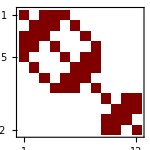

```mathematica
MatrixPlot[Γ2F,ImageSize->150]
```

```mathematica
Γ2F//MatrixForm
```

(hϕ σ | 0 | -ⅈ (q0+ⅈ q3)-μ | -ⅈ (ⅈ q1+q2) | d hΔ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | hϕ σ | -ⅈ (ⅈ q1-q2) | -ⅈ (q0-ⅈ q3)-μ | 0 | d hΔ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ (q0-ⅈ q3)-μ | -ⅈ (-ⅈ q1-q2) | hϕ σ | 0 | 0 | 0 | -d hΔ | 0 | 0 | 0 | 0 | 0
-ⅈ (-ⅈ q1+q2) | -ⅈ (q0+ⅈ q3)-μ | 0 | hϕ σ | 0 | 0 | 0 | -d hΔ | 0 | 0 | 0 | 0
-d hΔ | 0 | 0 | 0 | hϕ σ | 0 | -ⅈ (q0+ⅈ q3)+μ | -ⅈ (ⅈ q1+q2) | 0 | 0 | 0 | 0
0 | -d hΔ | 0 | 0 | 0 | hϕ σ | -ⅈ (ⅈ q1-q2) | -ⅈ (q0-ⅈ q3)+μ | 0 | 0 | 0 | 0
0 | 0 | d hΔ | 0 | -ⅈ (q0-ⅈ q3)+μ | -ⅈ (-ⅈ q1-q2) | hϕ σ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | d hΔ | -ⅈ (-ⅈ q1+q2) | -ⅈ (q0+ⅈ q3)+μ | 0 | hϕ σ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | hϕ σ | 0 | -ⅈ (q0+ⅈ q3)-μ | -ⅈ (ⅈ q1+q2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | hϕ σ | -ⅈ (ⅈ q1-q2) | -ⅈ (q0-ⅈ q3)-μ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (q0-ⅈ q3)-μ | -ⅈ (-ⅈ q1-q2) | hϕ σ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ (-ⅈ q1+q2) | -ⅈ (q0+ⅈ q3)-μ | 0 | hϕ σ)

```mathematica
Rk =-I ( q1 γ1 +q2 γ2+ q3 γ3 )(k/Sqrt[q1^2+q2^2+q3^2]-1)HS; (*q1^2+q2^2+q3^2 = qv^2*)
dkRk=- I ( q1 γ1 +q2 γ2+ q3 γ3 )1/Sqrt[q1^2+q2^2+q3^2]HS;
RkMat = ArrayFlatten[{{Rk,γZero,γZero},{γZero,Rk,γZero},{γZero,γZero,Rk}}];
```

Separate paired and unpaired quark contributions

```mathematica
Γ2FGap=FullSimplify[Γ2F[[1;;8,1;;8]] +RkMat[[1;;8,1;;8]]];
Γ2FNoGap=FullSimplify[Γ2F[[9;;12,9;;12]] +RkMat[[9;;12,9;;12]]];
```

```mathematica
Γ2FNoGapInvDen=Denominator[Inverse[Γ2FNoGap][[1,1]]];
Γ2FNoGapInv=Simplify[Inverse[Γ2FNoGap]/.{Γ2FNoGapInvDen->DenNoGap}]/.{q1^2->qv^2-q2^2-q3^2};
```

## Flow Equation for the Effective Potential

Ungapped Contribution to effective potential:

```mathematica
ΓFNoGapTrace=Simplify[Simplify[Tr[dkRk.Γ2FNoGapInv]/.{DenNoGap->FullSimplify[Γ2FNoGapInvDen]/.{q1^2->qv^2-q2^2-q3^2}}]/.{q1^2->qv^2-q2^2-q3^2}];
```

```mathematica
ΓFNoGapQMM=FullSimplify[ΓFNoGapTrace/.{HS->1}] (* Check! *)
```

(4 k)/(k^2+(q0-ⅈ μ)^2+hϕ^2 σ^2)

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
FullSimplify[MatsubaraSum[ΓFNoGapQMM/.{k^2->Ek^2-hϕ^2 σ^2}/.{q0->-I z},z∈Fermionic]]
```

(2 k (n_F[-Ek-μ]-n_F[Ek-μ]))/Ek

```mathematica
nF[x_]:=1/(1+Exp[x/T])
```

```mathematica
FullSimplify[(2 k (nF[-Ek-μ]-nF[Ek-μ]))/Ek]
```

(2 k Sinh[Ek/T])/(Ek Cosh[Ek/T]+Ek Cosh[μ/T])

```mathematica
1/3*Nf*4*4π/(2π)^3
```

(2 Nf)/(3 π^2)

```mathematica
(* Correct result! (up to some factor times Subscript[N, f]/π^2) *)
```

Gapped Contribution to effective potential:

```mathematica
dkRkGap =ArrayFlatten[{{dkRk,γZero},{γZero,dkRk}}];
```

```mathematica
Γ2FGapInvDen=Denominator[Inverse[Γ2FGap][[1,1]]];
Γ2FGapInv=Inverse[Γ2FGap]/.{Γ2FGapInvDen->DenGap}/.{q1^2->qv^2-q2^2-q3^2};
```

```mathematica
ΓFGapTrace=Tr[dkRkGap .Γ2FGapInv];
```

```mathematica
ΓFGapQC2D=Simplify[Simplify[FullSimplify[Simplify[ΓFGapTrace/.{HS->1}]/.{q1^2->qv^2-q2^2-q3^2,q1^4->(qv^2-q2^2-q3^2)^2,q1^6->(qv^2-q2^2-q3^2)^3}]/.{DenGap-> Simplify[Γ2FGapInvDen/.{HS->1,q1^2+q2^2+q3^2->qv^2}]}]/.{q1^2+q2^2+q3^2->qv^2}]
```

(8 k (d^2 hΔ^2+k^2+q0^2-μ^2+hϕ^2 σ^2))/(d^4 hΔ^4+k^4+q0^4+2 q0^2 μ^2+μ^4+2 hϕ^2 q0^2 σ^2-2 hϕ^2 μ^2 σ^2+hϕ^4 σ^4+2 k^2 (q0^2-μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (k^2+q0^2+μ^2+hϕ^2 σ^2))

```mathematica
den=d^4 hΔ^4+k^4+q0^4+2 q0^2 μ^2+μ^4+2 hϕ^2 q0^2 σ^2-2 hϕ^2 μ^2 σ^2+hϕ^4 σ^4+2 k^2 (q0^2-μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (k^2+q0^2+μ^2+hϕ^2 σ^2);
denPaper = (q0^2+(hΔ^2 d^2+(Sqrt[k^2+hϕ^2 σ^2]+μ)^2))(q0^2+(hΔ^2 d^2+(Sqrt[k^2+hϕ^2 σ^2]-μ)^2));
```

```mathematica
FullSimplify[Expand[denPaper]==Expand[den]]
```

True

```mathematica
FullSimplify[MatsubaraSum[ΓFGapQC2D/.{q0->-I z},z∈Fermionic]/.{(k^2+hϕ^2 σ^2)->ϵ^2}/.{d^2 hΔ^2+ϵ^2+μ^2-2 √(μ^2 (k^2+hϕ^2 σ^2))->Ekm^2,d^2 hΔ^2+ϵ^2+μ^2+2 √(μ^2 (k^2+hϕ^2 σ^2))->Ekp^2},{Ekp>0,Ekm>0,μ>0,ϵ>0}]
```

(2 k (Ekp (ϵ-μ)+Ekm (ϵ+μ)+2 Ekp (-ϵ+μ) n_F[Ekm]-2 Ekm (ϵ+μ) n_F[Ekp]))/(Ekm Ekp ϵ)

## Flow Equation Γ_F^(2): Ungapped Part

```mathematica
dkRkNoGapqp=dkRk/.{q1->q1+p1,q2->q2+p2,q3->q3+p3}/.{HS->1}/.{p1->0,p2->0,p3->pv};
Γ2FNoGapqp=Simplify[Inverse[Γ2FNoGap/.{q1->q1+p1,q2->q2+p2,q3->q3+p3}/.{HS->1}/.{p1->0,p2->0,p3->pv}]];
Γ2FNoGap0=Simplify[Inverse[Γ2FNoGap/.{HS->0}/.{p1->0,p2->0,p3->pv}]];
Γ2FNoGap1=Simplify[Inverse[Γ2FNoGap/.{HS->1}/.{p1->0,p2->0,p3->pv}]];
```

```mathematica
Γψψπ=hϕ I γ5; (*τ cancels with second τ after Trace*)
```

```mathematica
Γ3MatNoGap1=dkRkNoGapqp.Γ2FNoGapqp.Γψψπ.Γ2FNoGap1.Γψψπ.Γ2FNoGapqp;
```

```mathematica
KugelKoord = {q1->qv Sin[θ]Cos[ϕ],q2->qv Sin[θ]Sin[ϕ],q3->qv Cos[θ]};
```

Next line takes a few minutes

```mathematica
Γ3MatNoGapPart1=FullSimplify[Expand[FullSimplify[Tr[Γ3MatNoGap1]/.{q1^2->qv^2-q2^2-q3^2}/.KugelKoord,{qv>0,pv>0}]]]
```

-((4 hϕ^2 k (k^2 qv+pv (k^2-(q0-ⅈ μ)^2-hϕ^2 σ^2) Cos[θ]+((q0-ⅈ μ)^2+hϕ^2 σ^2) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ]))))/((k^2+(q0-ⅈ μ)^2+hϕ^2 σ^2)^3 √(pv^2+qv^2+2 pv qv Cos[θ])))

```mathematica
Γ3MatNoGap0=dkRkNoGapqp.Γ2FNoGapqp.Γψψπ.Γ2FNoGap0.Γψψπ.Γ2FNoGapqp;
```

```mathematica
Γ3MatNoGapPart0=FullSimplify[Expand[FullSimplify[Tr[Γ3MatNoGap0]/.{q1^2->qv^2-q2^2-q3^2}/.KugelKoord,{qv>0,pv>0}]]]
```

-((4 hϕ^2 (qv^2 (k^2-(q0-ⅈ μ)^2-hϕ^2 σ^2)+pv qv (k^2-(q0-ⅈ μ)^2-hϕ^2 σ^2) Cos[θ]+2 k ((q0-ⅈ μ)^2+hϕ^2 σ^2) √(pv^2+qv^2+2 pv qv Cos[θ])))/((k^2+(q0-ⅈ μ)^2+hϕ^2 σ^2)^2 (qv^2+(q0-ⅈ μ)^2+hϕ^2 σ^2) √(pv^2+qv^2+2 pv qv Cos[θ])))

Check with manually calculated result:

```mathematica
cosϕV=(qv^2+qv pv Cos[θ])/(qv Sqrt[qv^2+pv^2+2qv pv Cos[θ]]);
Γ3MatNoGapMan0=4*hϕ^2(qv cosϕV (-k^2+(q0-I μ)^2+(hϕ σ)^2)+k(-2(hϕ σ)^2-2(q0-I μ)^2))/((k^2+(q0-ⅈ μ)^2+hϕ^2 σ^2)^2(qv^2+(q0-ⅈ μ)^2+hϕ^2 σ^2));
Γ3MatNoGapMan1=4*hϕ^2(k cosϕV(-k^2+(q0-I μ)^2+(hϕ σ)^2)+k(-2(hϕ σ)^2-2(q0-I μ)^2))/(k^2+(q0-ⅈ μ)^2+hϕ^2 σ^2)^3 ;
```

```mathematica
FullSimplify[Expand[Γ3MatNoGapPart0]==Expand[Γ3MatNoGapMan0] ]
```

True

```mathematica
FullSimplify[Expand[Γ3MatNoGapPart1]==Expand[Γ3MatNoGapMan1] ]
```

True

## Flow Equation Γ_F^(2): Gapped Part

Simplification takes about 20 minutes!

```mathematica
dkRkGap =ArrayFlatten[{{dkRk,γZero},{γZero,dkRk}}];
KugelKoord = {q1->qv Sin[θ]Cos[ϕ],q2->qv Sin[θ]Sin[ϕ],q3->qv Cos[θ]};
dkRkGapqp=dkRkGap /.{q1->q1+p1,q2->q2+p2,q3->q3+p3}/.{HS->1}/.{p1->0,p2->0,p3->pv};
```

```mathematica
dkRkGapqp=dkRkGap /.{q1->q1+p1,q2->q2+p2,q3->q3+p3}/.{HS->1}/.{p1->0,p2->0,p3->pv};
Γ2FGapqp=Simplify[Inverse[Γ2FGap/.{q1->q1+p1,q2->q2+p2,q3->q3+p3}/.{HS->1}/.{p1->0,p2->0,p3->pv}]];
Γ2FGap0=Simplify[Inverse[Γ2FGap/.{HS->0}/.{p1->0,p2->0,p3->pv}]/.KugelKoord];
Γ2FGap1=Simplify[Inverse[Γ2FGap/.{HS->1}/.{p1->0,p2->0,p3->pv}]/.KugelKoord];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

Save Expressions for the next session

```mathematica
DumpSave["Gamma2FParts.mx",{Γ2FGapqp,Γ2FGap0,Γ2FGap1}];
```

```mathematica
DumpGet["Gamma2FParts.mx"]
```

Fermionc Vertex Functions

```mathematica
Γψψπ=hϕ I γ5; 
ΓψψπGap = ArrayFlatten[{{Γψψπ,γZero},{γZero,-Γψψπ}}];(*Note minus sign in (22) entry*)
```

We first calculate only the trace of the numerator in order to prevent the denominator to be manipulated into another form:

#### Pull out common denominator and simplify

```mathematica
ϵV=Sqrt[k^2+hϕ^2 σ^2];
EkpV=Sqrt[hΔ^2 d^2+(ϵV+μ)^2];
EkmV=Sqrt[hΔ^2 d^2+(ϵV-μ)^2];
ϵqV=Sqrt[qv^2+hϕ^2 σ^2];
EqpV=Sqrt[hΔ^2 d^2+(ϵqV+μ)^2];
EqmV=Sqrt[hΔ^2 d^2+(ϵqV-μ)^2];
```

```mathematica
Γ2FGap0Sim=Simplify[Γ2FGap0,{d^4 hΔ^4+q0^4+(qv^2-μ^2+hϕ^2 σ^2)^2+2 q0^2 (qv^2+μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (q0^2+qv^2+μ^2+hϕ^2 σ^2)==Den0,ϵqV^2==ϵq^2,ϵV^2==ϵ^2,EkpV^2==Ekp^2,EkmV^2==Ekm^2,EqpV^2==Eqp^2,EqmV^2==Eqm^2}];
```

```mathematica
Γ2FGap1Sim=Simplify[Γ2FGap1,{(d^4 hΔ^4+k^4+q0^4+2 q0^2 μ^2+μ^4+2 hϕ^2 q0^2 σ^2-2 hϕ^2 μ^2 σ^2+hϕ^4 σ^4+2 k^2 (q0^2-μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (k^2+q0^2+μ^2+hϕ^2 σ^2))==Den,ϵqV^2==ϵq^2,ϵV^2==ϵ^2,EkpV^2==Ekp^2,EkmV^2==Ekm^2,EqpV^2==Eqp^2,EqmV^2==Eqm^2}];
```

```mathematica
Γ2FGapqpSim=Simplify[Γ2FGapqp,{(d^4 hΔ^4+k^4+q0^4+2 q0^2 μ^2+μ^4+2 hϕ^2 q0^2 σ^2-2 hϕ^2 μ^2 σ^2+hϕ^4 σ^4+2 k^2 (q0^2-μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (k^2+q0^2+μ^2+hϕ^2 σ^2))==Den,ϵqV^2==ϵq^2,ϵV^2==ϵ^2,EkpV^2==Ekp^2,EkmV^2==Ekm^2,EqpV^2==Eqp^2,EqmV^2==Eqm^2}];
```

```mathematica
denqp = (q0^2+Ekp^2)(q0^2+Ekm^2);
denq = (q0^2+Eqp^2)(q0^2+Eqm^2);
```

```mathematica
FullSimplify[(d^4 hΔ^4+k^4+q0^4+2 q0^2 μ^2+μ^4+2 hϕ^2 q0^2 σ^2-2 hϕ^2 μ^2 σ^2+hϕ^4 σ^4+2 k^2 (q0^2-μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (k^2+q0^2+μ^2+hϕ^2 σ^2))==denqp/.{Ekp->EkpV,Ekm->EkmV}]
```

True

#### Calculate Matrix product + Trace

```mathematica
fractionExpand[expr_]:=Replace[Expand@expr,expr2_Plus:>(Together@*Plus@@@GatherBy[List@@expr2,Variables@*Denominator]//Total)]
```

Case 1: k^2 > qv^2

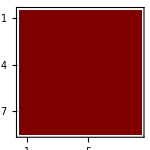

```mathematica
MatrixPlot[dkRkGapqp.(Γ2FGapqpSim).ΓψψπGap.(Γ2FGap1Sim).ΓψψπGap.(Γ2FGapqpSim),ImageSize->150]
```

```mathematica
Γ3MatGap1Numerator=dkRkGapqp.(Den*Γ2FGapqpSim).ΓψψπGap.(Den*Γ2FGap1Sim).ΓψψπGap.(Den*Γ2FGapqpSim);
```

```mathematica
Γ3MatGapPart1Numerator=Simplify[Tr[Γ3MatGap1Numerator]/.KugelKoord,{qv>0,pv>0}]
```

-1/(√(pv^2+qv^2+2 pv qv Cos[θ]))8 hϕ^2 k (k^2 q0^6 qv-q0^8 qv+3 k^2 q0^4 qv ϵ^2-3 q0^6 qv ϵ^2+3 k^2 q0^2 qv ϵ^4-3 q0^4 qv ϵ^4+k^2 qv ϵ^6-q0^2 qv ϵ^6-15 k^2 q0^4 qv μ^2+4 q0^6 qv μ^2-18 k^2 q0^2 qv ϵ^2 μ^2-3 q0^4 qv ϵ^2 μ^2-3 k^2 qv ϵ^4 μ^2-6 q0^2 qv ϵ^4 μ^2+qv ϵ^6 μ^2+15 k^2 q0^2 qv μ^4+10 q0^4 qv μ^4+3 k^2 qv ϵ^2 μ^4+3 q0^2 qv ϵ^2 μ^4-3 qv ϵ^4 μ^4-k^2 qv μ^6+4 q0^2 qv μ^6+3 qv ϵ^2 μ^6-qv μ^8-hϕ^2 q0^6 qv σ^2-3 hϕ^2 q0^4 qv ϵ^2 σ^2-3 hϕ^2 q0^2 qv ϵ^4 σ^2-hϕ^2 qv ϵ^6 σ^2+15 hϕ^2 q0^4 qv μ^2 σ^2+18 hϕ^2 q0^2 qv ϵ^2 μ^2 σ^2+3 hϕ^2 qv ϵ^4 μ^2 σ^2-15 hϕ^2 q0^2 qv μ^4 σ^2-3 hϕ^2 qv ϵ^2 μ^4 σ^2+hϕ^2 qv μ^6 σ^2-pv (d^8 hΔ^8+q0^8+3 q0^6 ϵ^2+3 q0^4 ϵ^4+q0^2 ϵ^6-4 q0^6 μ^2+3 q0^4 ϵ^2 μ^2+6 q0^2 ϵ^4 μ^2-ϵ^6 μ^2-10 q0^4 μ^4-3 q0^2 ϵ^2 μ^4+3 ϵ^4 μ^4-4 q0^2 μ^6-3 ϵ^2 μ^6+μ^8-k^2 (q0^6+3 q0^4 (ϵ^2-5 μ^2)+(ϵ^2-μ^2)^3+3 q0^2 (ϵ^4-6 ϵ^2 μ^2+5 μ^4))+hϕ^2 q0^6 σ^2+3 hϕ^2 q0^4 ϵ^2 σ^2+3 hϕ^2 q0^2 ϵ^4 σ^2+hϕ^2 ϵ^6 σ^2-15 hϕ^2 q0^4 μ^2 σ^2-18 hϕ^2 q0^2 ϵ^2 μ^2 σ^2-3 hϕ^2 ϵ^4 μ^2 σ^2+15 hϕ^2 q0^2 μ^4 σ^2+3 hϕ^2 ϵ^2 μ^4 σ^2-hϕ^2 μ^6 σ^2+d^6 hΔ^6 (-k^2+4 q0^2+3 ϵ^2-4 μ^2+hϕ^2 σ^2)+d^4 hΔ^4 (6 q0^4+3 ϵ^4+3 ϵ^2 μ^2-10 μ^4-3 k^2 (q0^2+ϵ^2-5 μ^2)+3 hϕ^2 ϵ^2 σ^2-15 hϕ^2 μ^2 σ^2+3 q0^2 (3 ϵ^2-4 μ^2+hϕ^2 σ^2))+d^2 hΔ^2 (4 q0^6-3 k^2 (q0^4+ϵ^4-6 ϵ^2 μ^2+5 μ^4+2 q0^2 (ϵ^2-5 μ^2))+3 q0^4 (3 ϵ^2-4 μ^2+hϕ^2 σ^2)+q0^2 (6 ϵ^4+6 ϵ^2 (μ^2+hϕ^2 σ^2)-10 μ^2 (2 μ^2+3 hϕ^2 σ^2))+(ϵ^2-μ^2) (ϵ^4+4 μ^4-15 hϕ^2 μ^2 σ^2+ϵ^2 (7 μ^2+3 hϕ^2 σ^2)))) Cos[θ]+2 q0^8 √(pv^2+qv^2+2 pv qv Cos[θ])+6 q0^6 ϵ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 q0^4 ϵ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+2 q0^2 ϵ^6 √(pv^2+qv^2+2 pv qv Cos[θ])-8 q0^6 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 q0^4 ϵ^2 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+12 q0^2 ϵ^4 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 ϵ^6 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-20 q0^4 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-6 q0^2 ϵ^2 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+6 ϵ^4 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-8 q0^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])-6 ϵ^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])+2 μ^8 √(pv^2+qv^2+2 pv qv Cos[θ])+2 hϕ^2 q0^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 hϕ^2 q0^4 ϵ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 hϕ^2 q0^2 ϵ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+2 hϕ^2 ϵ^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-30 hϕ^2 q0^4 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-36 hϕ^2 q0^2 ϵ^2 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-6 hϕ^2 ϵ^4 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+30 hϕ^2 q0^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 hϕ^2 ϵ^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 μ^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+d^8 hΔ^8 (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ]))+d^6 hΔ^6 (k^2 qv+(4 q0^2+3 ϵ^2-4 μ^2+hϕ^2 σ^2) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ])))+d^4 hΔ^4 (3 k^2 qv (q0^2+ϵ^2-5 μ^2)+(6 q0^4+3 ϵ^4+3 q0^2 (3 ϵ^2-4 μ^2+hϕ^2 σ^2)+3 ϵ^2 (μ^2+hϕ^2 σ^2)-5 (2 μ^4+3 hϕ^2 μ^2 σ^2)) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ])))+d^2 hΔ^2 (3 k^2 qv (q0^4+ϵ^4-6 ϵ^2 μ^2+5 μ^4+2 q0^2 (ϵ^2-5 μ^2))+(4 q0^6+3 q0^4 (3 ϵ^2-4 μ^2+hϕ^2 σ^2)+q0^2 (6 ϵ^4+6 ϵ^2 (μ^2+hϕ^2 σ^2)-10 μ^2 (2 μ^2+3 hϕ^2 σ^2))+(ϵ^2-μ^2) (ϵ^4+4 μ^4-15 hϕ^2 μ^2 σ^2+ϵ^2 (7 μ^2+3 hϕ^2 σ^2))) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ]))))

```mathematica
Γ3MatGapPart1Numerator=-1/(√(pv^2+qv^2+2 pv qv Cos[θ]))8 hϕ^2 k (k^2 q0^6 qv-q0^8 qv+3 k^2 q0^4 qv ϵ^2-3 q0^6 qv ϵ^2+3 k^2 q0^2 qv ϵ^4-3 q0^4 qv ϵ^4+k^2 qv ϵ^6-q0^2 qv ϵ^6-15 k^2 q0^4 qv μ^2+4 q0^6 qv μ^2-18 k^2 q0^2 qv ϵ^2 μ^2-3 q0^4 qv ϵ^2 μ^2-3 k^2 qv ϵ^4 μ^2-6 q0^2 qv ϵ^4 μ^2+qv ϵ^6 μ^2+15 k^2 q0^2 qv μ^4+10 q0^4 qv μ^4+3 k^2 qv ϵ^2 μ^4+3 q0^2 qv ϵ^2 μ^4-3 qv ϵ^4 μ^4-k^2 qv μ^6+4 q0^2 qv μ^6+3 qv ϵ^2 μ^6-qv μ^8-hϕ^2 q0^6 qv σ^2-3 hϕ^2 q0^4 qv ϵ^2 σ^2-3 hϕ^2 q0^2 qv ϵ^4 σ^2-hϕ^2 qv ϵ^6 σ^2+15 hϕ^2 q0^4 qv μ^2 σ^2+18 hϕ^2 q0^2 qv ϵ^2 μ^2 σ^2+3 hϕ^2 qv ϵ^4 μ^2 σ^2-15 hϕ^2 q0^2 qv μ^4 σ^2-3 hϕ^2 qv ϵ^2 μ^4 σ^2+hϕ^2 qv μ^6 σ^2-pv (d^8 hΔ^8+q0^8+3 q0^6 ϵ^2+3 q0^4 ϵ^4+q0^2 ϵ^6-4 q0^6 μ^2+3 q0^4 ϵ^2 μ^2+6 q0^2 ϵ^4 μ^2-ϵ^6 μ^2-10 q0^4 μ^4-3 q0^2 ϵ^2 μ^4+3 ϵ^4 μ^4-4 q0^2 μ^6-3 ϵ^2 μ^6+μ^8-k^2 (q0^6+3 q0^4 (ϵ^2-5 μ^2)+(ϵ^2-μ^2)^3+3 q0^2 (ϵ^4-6 ϵ^2 μ^2+5 μ^4))+hϕ^2 q0^6 σ^2+3 hϕ^2 q0^4 ϵ^2 σ^2+3 hϕ^2 q0^2 ϵ^4 σ^2+hϕ^2 ϵ^6 σ^2-15 hϕ^2 q0^4 μ^2 σ^2-18 hϕ^2 q0^2 ϵ^2 μ^2 σ^2-3 hϕ^2 ϵ^4 μ^2 σ^2+15 hϕ^2 q0^2 μ^4 σ^2+3 hϕ^2 ϵ^2 μ^4 σ^2-hϕ^2 μ^6 σ^2+d^6 hΔ^6 (-k^2+4 q0^2+3 ϵ^2-4 μ^2+hϕ^2 σ^2)+d^4 hΔ^4 (6 q0^4+3 ϵ^4+3 ϵ^2 μ^2-10 μ^4-3 k^2 (q0^2+ϵ^2-5 μ^2)+3 hϕ^2 ϵ^2 σ^2-15 hϕ^2 μ^2 σ^2+3 q0^2 (3 ϵ^2-4 μ^2+hϕ^2 σ^2))+d^2 hΔ^2 (4 q0^6-3 k^2 (q0^4+ϵ^4-6 ϵ^2 μ^2+5 μ^4+2 q0^2 (ϵ^2-5 μ^2))+3 q0^4 (3 ϵ^2-4 μ^2+hϕ^2 σ^2)+q0^2 (6 ϵ^4+6 ϵ^2 (μ^2+hϕ^2 σ^2)-10 μ^2 (2 μ^2+3 hϕ^2 σ^2))+(ϵ^2-μ^2) (ϵ^4+4 μ^4-15 hϕ^2 μ^2 σ^2+ϵ^2 (7 μ^2+3 hϕ^2 σ^2)))) Cos[θ]+2 q0^8 √(pv^2+qv^2+2 pv qv Cos[θ])+6 q0^6 ϵ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 q0^4 ϵ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+2 q0^2 ϵ^6 √(pv^2+qv^2+2 pv qv Cos[θ])-8 q0^6 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 q0^4 ϵ^2 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+12 q0^2 ϵ^4 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 ϵ^6 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-20 q0^4 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-6 q0^2 ϵ^2 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+6 ϵ^4 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-8 q0^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])-6 ϵ^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])+2 μ^8 √(pv^2+qv^2+2 pv qv Cos[θ])+2 hϕ^2 q0^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 hϕ^2 q0^4 ϵ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 hϕ^2 q0^2 ϵ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+2 hϕ^2 ϵ^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-30 hϕ^2 q0^4 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-36 hϕ^2 q0^2 ϵ^2 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-6 hϕ^2 ϵ^4 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+30 hϕ^2 q0^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+6 hϕ^2 ϵ^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 μ^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+d^8 hΔ^8 (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ]))+d^6 hΔ^6 (k^2 qv+(4 q0^2+3 ϵ^2-4 μ^2+hϕ^2 σ^2) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ])))+d^4 hΔ^4 (3 k^2 qv (q0^2+ϵ^2-5 μ^2)+(6 q0^4+3 ϵ^4+3 q0^2 (3 ϵ^2-4 μ^2+hϕ^2 σ^2)+3 ϵ^2 (μ^2+hϕ^2 σ^2)-5 (2 μ^4+3 hϕ^2 μ^2 σ^2)) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ])))+d^2 hΔ^2 (3 k^2 qv (q0^4+ϵ^4-6 ϵ^2 μ^2+5 μ^4+2 q0^2 (ϵ^2-5 μ^2))+(4 q0^6+3 q0^4 (3 ϵ^2-4 μ^2+hϕ^2 σ^2)+q0^2 (6 ϵ^4+6 ϵ^2 (μ^2+hϕ^2 σ^2)-10 μ^2 (2 μ^2+3 hϕ^2 σ^2))+(ϵ^2-μ^2) (ϵ^4+4 μ^4-15 hϕ^2 μ^2 σ^2+ϵ^2 (7 μ^2+3 hϕ^2 σ^2))) (-qv+2 √(pv^2+qv^2+2 pv qv Cos[θ]))));
```

```mathematica
Clear[v]
```

```mathematica
Γ3MatGapPart1NumeratorInt=Integrate[Γ3MatGapPart1Numerator/.{ Cos[θ]->v-1},v];
```

```mathematica
Γ3MatGapPart1NumeratorIntv1=(Γ3MatGapPart1NumeratorInt/.{v->2})-(Γ3MatGapPart1NumeratorInt/.{v->0});
```

```mathematica
simplyfiedNum=Collect[Γ3MatGapPart1NumeratorIntv1,q0];
A5=Coefficient[simplyfiedNum,q0,10];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
```

```mathematica
Γ3MatGapPart1Sim=(simplyfiedNum/.{A0->a0}/.{A4->a4,A3->a3,A2->a2,A1->a1})/denqp^3
```

(a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8)/((Ekm^2+q0^2)^3 (Ekp^2+q0^2)^3)

```mathematica
Γ2FMatSum1=Sum[Γ3MatGapPart1Sim/.{q0->(2n+1)π T},{n,-∞,∞}];
```

```mathematica
Γ2FMatSum1Sim=T Simplify[Γ2FMatSum1];
```

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
Γ2FMatSum1=FullSimplify[MatsubaraSum[Γ3MatGapPart1Sim/.{q0->-I z},z∈Fermionic]]
```

((Ekm-Ekp)^5 (a1 Ekm^2 Ekp^2 (Ekm^2+5 Ekm Ekp+Ekp^2)+3 a0 (Ekm^4+5 Ekm^3 Ekp+9 Ekm^2 Ekp^2+5 Ekm Ekp^3+Ekp^4)+Ekm^4 Ekp^4 (3 a2+Ekm Ekp (3 a3+a4 (Ekm^2+5 Ekm Ekp+Ekp^2))))+2 Ekp^5 (-Ekm^4 (-63 a0+35 a1 Ekm^2-15 a2 Ekm^4+3 a3 Ekm^6+a4 Ekm^8)+2 Ekm^2 (-9 a0-7 a1 Ekm^2+15 a2 Ekm^4-15 a3 Ekm^6+7 a4 Ekm^8) Ekp^2+(3 a0+a1 Ekm^2+3 a2 Ekm^4-15 a3 Ekm^6+35 a4 Ekm^8) Ekp^4) n_F[Ekm]-2 Ekm^5 (3 a0 Ekm^4+Ekm^2 (-18 a0+a1 Ekm^2) Ekp^2+(63 a0-14 a1 Ekm^2+3 a2 Ekm^4) Ekp^4-5 (7 a1-6 a2 Ekm^2+3 a3 Ekm^4) Ekp^6+5 (3 a2-6 a3 Ekm^2+7 a4 Ekm^4) Ekp^8+(-3 a3+14 a4 Ekm^2) Ekp^10-a4 Ekp^12) n_F[Ekp]+2 Ekm (Ekm-Ekp) Ekp (Ekm+Ekp) (Ekp^4 (Ekm^4 (11 a1-7 a2 Ekm^2+3 a3 Ekm^4+a4 Ekm^6)+Ekm^2 (a1-5 a2 Ekm^2+9 a3 Ekm^4-13 a4 Ekm^6) Ekp^2+3 a0 (-5 Ekm^2+Ekp^2)) n'_F[Ekm]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2)) n'_F[Ekp]+Ekp (-Ekm^3+Ekm Ekp^2) (-(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3 n''_F[Ekm]+Ekm^3 (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) n''_F[Ekp])))/(16 Ekm^5 (Ekm-Ekp)^5 Ekp^5 (Ekm+Ekp)^5)

```mathematica
Γ2FMatSum1Sim=((Ekm-Ekp)^5 (a1 Ekm^2 Ekp^2 (Ekm^2+5 Ekm Ekp+Ekp^2)+3 a0 (Ekm^4+5 Ekm^3 Ekp+9 Ekm^2 Ekp^2+5 Ekm Ekp^3+Ekp^4)+Ekm^4 Ekp^4 (3 a2+Ekm Ekp (3 a3+a4 (Ekm^2+5 Ekm Ekp+Ekp^2))))+2 Ekp^5 (-Ekm^4 (-63 a0+35 a1 Ekm^2-15 a2 Ekm^4+3 a3 Ekm^6+a4 Ekm^8)+2 Ekm^2 (-9 a0-7 a1 Ekm^2+15 a2 Ekm^4-15 a3 Ekm^6+7 a4 Ekm^8) Ekp^2+(3 a0+a1 Ekm^2+3 a2 Ekm^4-15 a3 Ekm^6+35 a4 Ekm^8) Ekp^4) nF[Ekm,T]-2 Ekm^5 (3 a0 Ekm^4+Ekm^2 (-18 a0+a1 Ekm^2) Ekp^2+(63 a0-14 a1 Ekm^2+3 a2 Ekm^4) Ekp^4-5 (7 a1-6 a2 Ekm^2+3 a3 Ekm^4) Ekp^6+5 (3 a2-6 a3 Ekm^2+7 a4 Ekm^4) Ekp^8+(-3 a3+14 a4 Ekm^2) Ekp^10-a4 Ekp^12) nF[Ekp,T]+2 Ekm (Ekm-Ekp) Ekp (Ekm+Ekp) (Ekp^4 (Ekm^4 (11 a1-7 a2 Ekm^2+3 a3 Ekm^4+a4 Ekm^6)+Ekm^2 (a1-5 a2 Ekm^2+9 a3 Ekm^4-13 a4 Ekm^6) Ekp^2+3 a0 (-5 Ekm^2+Ekp^2)) nFd[Ekm,T]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2)) nFd[Ekp,T]+Ekp (-Ekm^3+Ekm Ekp^2) (-(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3 nFdd[Ekm,T]+Ekm^3 (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8)nFdd[Ekp,T])))/(16 Ekm^5 (Ekm-Ekp)^5 Ekp^5 (Ekm+Ekp)^5);
```

Integrate to v =  (k^2-(qv-pv)^2)/(2qv pv)

```mathematica
Γ3MatGapPart1NumeratorIntv2=(Γ3MatGapPart1NumeratorInt/.{v->(k^2-(qv-pv)^2)/(2qv pv)})-(Γ3MatGapPart1NumeratorInt/.{v->0});
```

```mathematica
simplyfiedNumv2=Collect[Γ3MatGapPart1NumeratorIntv2,q0];
A5v2=Coefficient[simplyfiedNumv2,q0,10];
A4v2=Coefficient[simplyfiedNumv2,q0,8];
A3v2=Coefficient[simplyfiedNumv2,q0,6];
A2v2=Coefficient[simplyfiedNumv2,q0,4];
A1v2=Coefficient[simplyfiedNumv2,q0,2];
A0v2=Coefficient[simplyfiedNumv2,q0,0];
```

```mathematica
Γ3MatGapPart1Simv2=(simplyfiedNumv2/.{A0v2->a0v2}/.{A4v2->a4v2,A3v2->a3v2,A2v2->a2v2,A1v2->a1v2})/denqp^3
```

(a0v2+a1v2 q0^2+a2v2 q0^4+a3v2 q0^6+a4v2 q0^8)/((Ekm^2+q0^2)^3 (Ekp^2+q0^2)^3)

```mathematica
Γ2FMatSum2=Sum[Γ3MatGapPart1Simv2/.{q0->(2n+1)π T},{n,-∞,∞}]
```

(15 a0v2 Ekm^5 Ekp^5 T Sech[Ekm/(2 T)]^2-11 a1v2 Ekm^7 Ekp^5 T Sech[Ekm/(2 T)]^2+7 a2v2 Ekm^9 Ekp^5 T Sech[Ekm/(2 T)]^2-3 a3v2 Ekm^11 Ekp^5 T Sech[Ekm/(2 T)]^2-a4v2 Ekm^13 Ekp^5 T Sech[Ekm/(2 T)]^2-18 a0v2 Ekm^3 Ekp^7 T Sech[Ekm/(2 T)]^2+10 a1v2 Ekm^5 Ekp^7 T Sech[Ekm/(2 T)]^2-2 a2v2 Ekm^7 Ekp^7 T Sech[Ekm/(2 T)]^2-6 a3v2 Ekm^9 Ekp^7 T Sech[Ekm/(2 T)]^2+14 a4v2 Ekm^11 Ekp^7 T Sech[Ekm/(2 T)]^2+3 a0v2 Ekm Ekp^9 T Sech[Ekm/(2 T)]^2+a1v2 Ekm^3 Ekp^9 T Sech[Ekm/(2 T)]^2-5 a2v2 Ekm^5 Ekp^9 T Sech[Ekm/(2 T)]^2+9 a3v2 Ekm^7 Ekp^9 T Sech[Ekm/(2 T)]^2-13 a4v2 Ekm^9 Ekp^9 T Sech[Ekm/(2 T)]^2-3 a0v2 Ekm^9 Ekp T Sech[Ekp/(2 T)]^2+18 a0v2 Ekm^7 Ekp^3 T Sech[Ekp/(2 T)]^2-a1v2 Ekm^9 Ekp^3 T Sech[Ekp/(2 T)]^2-15 a0v2 Ekm^5 Ekp^5 T Sech[Ekp/(2 T)]^2-10 a1v2 Ekm^7 Ekp^5 T Sech[Ekp/(2 T)]^2+5 a2v2 Ekm^9 Ekp^5 T Sech[Ekp/(2 T)]^2+11 a1v2 Ekm^5 Ekp^7 T Sech[Ekp/(2 T)]^2+2 a2v2 Ekm^7 Ekp^7 T Sech[Ekp/(2 T)]^2-9 a3v2 Ekm^9 Ekp^7 T Sech[Ekp/(2 T)]^2-7 a2v2 Ekm^5 Ekp^9 T Sech[Ekp/(2 T)]^2+6 a3v2 Ekm^7 Ekp^9 T Sech[Ekp/(2 T)]^2+13 a4v2 Ekm^9 Ekp^9 T Sech[Ekp/(2 T)]^2+3 a3v2 Ekm^5 Ekp^11 T Sech[Ekp/(2 T)]^2-14 a4v2 Ekm^7 Ekp^11 T Sech[Ekp/(2 T)]^2+a4v2 Ekm^5 Ekp^13 T Sech[Ekp/(2 T)]^2+8 a0v2 Ekm^6 Ekp^5 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-8 a1v2 Ekm^8 Ekp^5 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+8 a2v2 Ekm^10 Ekp^5 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-8 a3v2 Ekm^12 Ekp^5 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+8 a4v2 Ekm^14 Ekp^5 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-16 a0v2 Ekm^4 Ekp^7 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+16 a1v2 Ekm^6 Ekp^7 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-16 a2v2 Ekm^8 Ekp^7 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+16 a3v2 Ekm^10 Ekp^7 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-16 a4v2 Ekm^12 Ekp^7 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+8 a0v2 Ekm^2 Ekp^9 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-8 a1v2 Ekm^4 Ekp^9 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+8 a2v2 Ekm^6 Ekp^9 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-8 a3v2 Ekm^8 Ekp^9 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4+8 a4v2 Ekm^10 Ekp^9 Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-126 a0v2 Ekm^4 Ekp^5 T^2 Tanh[Ekm/(2 T)]+70 a1v2 Ekm^6 Ekp^5 T^2 Tanh[Ekm/(2 T)]-30 a2v2 Ekm^8 Ekp^5 T^2 Tanh[Ekm/(2 T)]+6 a3v2 Ekm^10 Ekp^5 T^2 Tanh[Ekm/(2 T)]+2 a4v2 Ekm^12 Ekp^5 T^2 Tanh[Ekm/(2 T)]+36 a0v2 Ekm^2 Ekp^7 T^2 Tanh[Ekm/(2 T)]+28 a1v2 Ekm^4 Ekp^7 T^2 Tanh[Ekm/(2 T)]-60 a2v2 Ekm^6 Ekp^7 T^2 Tanh[Ekm/(2 T)]+60 a3v2 Ekm^8 Ekp^7 T^2 Tanh[Ekm/(2 T)]-28 a4v2 Ekm^10 Ekp^7 T^2 Tanh[Ekm/(2 T)]-6 a0v2 Ekp^9 T^2 Tanh[Ekm/(2 T)]-2 a1v2 Ekm^2 Ekp^9 T^2 Tanh[Ekm/(2 T)]-6 a2v2 Ekm^4 Ekp^9 T^2 Tanh[Ekm/(2 T)]+30 a3v2 Ekm^6 Ekp^9 T^2 Tanh[Ekm/(2 T)]-70 a4v2 Ekm^8 Ekp^9 T^2 Tanh[Ekm/(2 T)]+6 a0v2 Ekm^9 T^2 Tanh[Ekp/(2 T)]-36 a0v2 Ekm^7 Ekp^2 T^2 Tanh[Ekp/(2 T)]+2 a1v2 Ekm^9 Ekp^2 T^2 Tanh[Ekp/(2 T)]+126 a0v2 Ekm^5 Ekp^4 T^2 Tanh[Ekp/(2 T)]-28 a1v2 Ekm^7 Ekp^4 T^2 Tanh[Ekp/(2 T)]+6 a2v2 Ekm^9 Ekp^4 T^2 Tanh[Ekp/(2 T)]-70 a1v2 Ekm^5 Ekp^6 T^2 Tanh[Ekp/(2 T)]+60 a2v2 Ekm^7 Ekp^6 T^2 Tanh[Ekp/(2 T)]-30 a3v2 Ekm^9 Ekp^6 T^2 Tanh[Ekp/(2 T)]+30 a2v2 Ekm^5 Ekp^8 T^2 Tanh[Ekp/(2 T)]-60 a3v2 Ekm^7 Ekp^8 T^2 Tanh[Ekp/(2 T)]+70 a4v2 Ekm^9 Ekp^8 T^2 Tanh[Ekp/(2 T)]-6 a3v2 Ekm^5 Ekp^10 T^2 Tanh[Ekp/(2 T)]+28 a4v2 Ekm^7 Ekp^10 T^2 Tanh[Ekp/(2 T)]-2 a4v2 Ekm^5 Ekp^12 T^2 Tanh[Ekp/(2 T)]-a0v2 Ekm^9 Ekp^2 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+2 a0v2 Ekm^7 Ekp^4 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+a1v2 Ekm^9 Ekp^4 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-a0v2 Ekm^5 Ekp^6 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-2 a1v2 Ekm^7 Ekp^6 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-a2v2 Ekm^9 Ekp^6 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+a1v2 Ekm^5 Ekp^8 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+2 a2v2 Ekm^7 Ekp^8 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+a3v2 Ekm^9 Ekp^8 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-a2v2 Ekm^5 Ekp^10 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-2 a3v2 Ekm^7 Ekp^10 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-a4v2 Ekm^9 Ekp^10 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+a3v2 Ekm^5 Ekp^12 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]+2 a4v2 Ekm^7 Ekp^12 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)]-a4v2 Ekm^5 Ekp^14 Sech[Ekp/(2 T)]^2 Tanh[Ekp/(2 T)])/(32 Ekm^5 Ekp^5 (Ekm^2-Ekp^2)^5 T^3)

```mathematica
Γ2FMatSum2Sim=T Simplify[Γ2FMatSum2];
```

```mathematica
Γ2FMatSum2Sim=T(-8 Ekm^4 (a1v2+a3v2 Ekm^4) Ekp^5 (Ekm^4+Ekp^4) Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-8 Ekm^5 Ekp^2 (Ekm^4+Ekp^4) (a0v2+a2v2 Ekp^4+a4v2 Ekp^8) Csch[Ekp/T]^3 Sinh[Ekp/(2 T)]^4+Ekm Ekp^5 Sech[Ekm/(2 T)]^2 (-(Ekm^2-Ekp^2) (-7 a2v2 Ekm^6+3 a3v2 Ekm^8+a4v2 Ekm^10-5 a2v2 Ekm^4 Ekp^2+9 a3v2 Ekm^6 Ekp^2-13 a4v2 Ekm^8 Ekp^2+3 a0v2 (-5 Ekm^2+Ekp^2)+a1v2 Ekm^2 (11 Ekm^2+Ekp^2)) T+Ekm (a0v2 (Ekm^2-Ekp^2)^2+Ekm^4 (2 (a1v2+a3v2 Ekm^4) Ekp^2+a2v2 (Ekm^2-Ekp^2)^2+a4v2 Ekm^4 (Ekm^2-Ekp^2)^2)) Tanh[Ekm/(2 T)])+2 T^2 (-Ekp^5 (-a4v2 Ekm^8 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)+a1v2 Ekm^2 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)+3 a0v2 (21 Ekm^4-6 Ekm^2 Ekp^2+Ekp^4)+3 a2v2 Ekm^4 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)-3 a3v2 Ekm^6 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)) Tanh[Ekm/(2 T)]+Ekm^5 (a1v2 Ekp^2 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)-a4v2 Ekp^8 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)-3 a3v2 Ekp^6 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)+3 a2v2 Ekp^4 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)+3 a0v2 (Ekm^4-6 Ekm^2 Ekp^2+21 Ekp^4)) Tanh[Ekp/(2 T)])+Ekm^5 Ekp Sech[Ekp/(2 T)]^2 (-(Ekm^2-Ekp^2) (-5 a2v2 Ekm^2 Ekp^4-7 a2v2 Ekp^6+9 a3v2 Ekm^2 Ekp^6+3 a3v2 Ekp^8-13 a4v2 Ekm^2 Ekp^8+a4v2 Ekp^10+3 a0v2 (Ekm^2-5 Ekp^2)+a1v2 Ekp^2 (Ekm^2+11 Ekp^2)) T+Ekp^3 (2 a0v2 Ekm^2+a1v2 (Ekm^2-Ekp^2)^2+Ekp^4 (2 a2v2 Ekm^2+2 a4v2 Ekm^2 Ekp^4+a3v2 (Ekm^2-Ekp^2)^2)) Tanh[Ekp/(2 T)]))/(32 Ekm^5 Ekp^5 (Ekm^2-Ekp^2)^5 T^3);
```

```mathematica
Γ2FMatSum2Sim=(-8 Ekm^4 (a1v2+a3v2 Ekm^4) Ekp^5 (Ekm^4+Ekp^4) Csch[Ekm/T]^3 Sinh[Ekm/(2 T)]^4-8 Ekm^5 Ekp^2 (Ekm^4+Ekp^4) (a0v2+a2v2 Ekp^4+a4v2 Ekp^8) Csch[Ekp/T]^3 Sinh[Ekp/(2 T)]^4+Ekm Ekp^5 Sech[Ekm/(2 T)]^2 (-(Ekm^2-Ekp^2) (-7 a2v2 Ekm^6+3 a3v2 Ekm^8+a4v2 Ekm^10-5 a2v2 Ekm^4 Ekp^2+9 a3v2 Ekm^6 Ekp^2-13 a4v2 Ekm^8 Ekp^2+3 a0v2 (-5 Ekm^2+Ekp^2)+a1v2 Ekm^2 (11 Ekm^2+Ekp^2)) T+Ekm (a0v2 (Ekm^2-Ekp^2)^2+Ekm^4 (2 (a1v2+a3v2 Ekm^4) Ekp^2+a2v2 (Ekm^2-Ekp^2)^2+a4v2 Ekm^4 (Ekm^2-Ekp^2)^2)) Tanh[Ekm/(2 T)])+2 T^2 (-Ekp^5 (-a4v2 Ekm^8 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)+a1v2 Ekm^2 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)+3 a0v2 (21 Ekm^4-6 Ekm^2 Ekp^2+Ekp^4)+3 a2v2 Ekm^4 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)-3 a3v2 Ekm^6 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)) Tanh[Ekm/(2 T)]+Ekm^5 (a1v2 Ekp^2 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)-a4v2 Ekp^8 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)-3 a3v2 Ekp^6 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)+3 a2v2 Ekp^4 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)+3 a0v2 (Ekm^4-6 Ekm^2 Ekp^2+21 Ekp^4)) Tanh[Ekp/(2 T)])+Ekm^5 Ekp Sech[Ekp/(2 T)]^2 (-(Ekm^2-Ekp^2) (-5 a2v2 Ekm^2 Ekp^4-7 a2v2 Ekp^6+9 a3v2 Ekm^2 Ekp^6+3 a3v2 Ekp^8-13 a4v2 Ekm^2 Ekp^8+a4v2 Ekp^10+3 a0v2 (Ekm^2-5 Ekp^2)+a1v2 Ekp^2 (Ekm^2+11 Ekp^2)) T+Ekp^3 (2 a0v2 Ekm^2+a1v2 (Ekm^2-Ekp^2)^2+Ekp^4 (2 a2v2 Ekm^2+2 a4v2 Ekm^2 Ekp^4+a3v2 (Ekm^2-Ekp^2)^2)) Tanh[Ekp/(2 T)]))/(32 Ekm^5 Ekp^5 (Ekm^2-Ekp^2)^5 T^2);
```

Case 2: k^2 < qv^2

```mathematica
Γ3MatGap2Numerator=dkRkGapqp.(Den*Γ2FGapqpSim).ΓψψπGap.(Den0*Γ2FGap0Sim).ΓψψπGap.(Den*Γ2FGapqpSim);
```

```mathematica
Γ3MatGapPart2Numerator=Simplify[Tr[Γ3MatGap2Numerator]/.KugelKoord,{qv>0,pv>0}]
```

1/(√(pv^2+qv^2+2 pv qv Cos[θ]))8 hϕ^2 (-k^2 q0^6 qv^2+q0^8 qv^2-2 k^2 q0^4 qv^2 ϵ^2+2 q0^6 qv^2 ϵ^2-k^2 q0^2 qv^2 ϵ^4+q0^4 qv^2 ϵ^4-k^2 q0^4 qv^2 ϵq^2+q0^6 qv^2 ϵq^2-2 k^2 q0^2 qv^2 ϵ^2 ϵq^2+2 q0^4 qv^2 ϵ^2 ϵq^2-k^2 qv^2 ϵ^4 ϵq^2+q0^2 qv^2 ϵ^4 ϵq^2+15 k^2 q0^4 qv^2 μ^2-4 q0^6 qv^2 μ^2+12 k^2 q0^2 qv^2 ϵ^2 μ^2+2 q0^4 qv^2 ϵ^2 μ^2+k^2 qv^2 ϵ^4 μ^2+2 q0^2 qv^2 ϵ^4 μ^2+6 k^2 q0^2 qv^2 ϵq^2 μ^2+q0^4 qv^2 ϵq^2 μ^2+2 k^2 qv^2 ϵ^2 ϵq^2 μ^2+4 q0^2 qv^2 ϵ^2 ϵq^2 μ^2-qv^2 ϵ^4 ϵq^2 μ^2-15 k^2 q0^2 qv^2 μ^4-10 q0^4 qv^2 μ^4-2 k^2 qv^2 ϵ^2 μ^4-2 q0^2 qv^2 ϵ^2 μ^4+qv^2 ϵ^4 μ^4-k^2 qv^2 ϵq^2 μ^4-q0^2 qv^2 ϵq^2 μ^4+2 qv^2 ϵ^2 ϵq^2 μ^4+k^2 qv^2 μ^6-4 q0^2 qv^2 μ^6-2 qv^2 ϵ^2 μ^6-qv^2 ϵq^2 μ^6+qv^2 μ^8+hϕ^2 q0^6 qv^2 σ^2+2 hϕ^2 q0^4 qv^2 ϵ^2 σ^2+hϕ^2 q0^2 qv^2 ϵ^4 σ^2+hϕ^2 q0^4 qv^2 ϵq^2 σ^2+2 hϕ^2 q0^2 qv^2 ϵ^2 ϵq^2 σ^2+hϕ^2 qv^2 ϵ^4 ϵq^2 σ^2-15 hϕ^2 q0^4 qv^2 μ^2 σ^2-12 hϕ^2 q0^2 qv^2 ϵ^2 μ^2 σ^2-hϕ^2 qv^2 ϵ^4 μ^2 σ^2-6 hϕ^2 q0^2 qv^2 ϵq^2 μ^2 σ^2-2 hϕ^2 qv^2 ϵ^2 ϵq^2 μ^2 σ^2+15 hϕ^2 q0^2 qv^2 μ^4 σ^2+2 hϕ^2 qv^2 ϵ^2 μ^4 σ^2+hϕ^2 qv^2 ϵq^2 μ^4 σ^2-hϕ^2 qv^2 μ^6 σ^2+pv qv (d^8 hΔ^8+q0^8+2 q0^6 ϵ^2+q0^4 ϵ^4+q0^6 ϵq^2+2 q0^4 ϵ^2 ϵq^2+q0^2 ϵ^4 ϵq^2-4 q0^6 μ^2+2 q0^4 ϵ^2 μ^2+2 q0^2 ϵ^4 μ^2+q0^4 ϵq^2 μ^2+4 q0^2 ϵ^2 ϵq^2 μ^2-ϵ^4 ϵq^2 μ^2-10 q0^4 μ^4-2 q0^2 ϵ^2 μ^4+ϵ^4 μ^4-q0^2 ϵq^2 μ^4+2 ϵ^2 ϵq^2 μ^4-4 q0^2 μ^6-2 ϵ^2 μ^6-ϵq^2 μ^6+μ^8-k^2 (q0^6+q0^4 (2 ϵ^2+ϵq^2-15 μ^2)+(ϵ^2-μ^2)^2 (ϵq^2-μ^2)+q0^2 (ϵ^4-6 ϵq^2 μ^2+15 μ^4+2 ϵ^2 (ϵq^2-6 μ^2)))+hϕ^2 q0^6 σ^2+2 hϕ^2 q0^4 ϵ^2 σ^2+hϕ^2 q0^2 ϵ^4 σ^2+hϕ^2 q0^4 ϵq^2 σ^2+2 hϕ^2 q0^2 ϵ^2 ϵq^2 σ^2+hϕ^2 ϵ^4 ϵq^2 σ^2-15 hϕ^2 q0^4 μ^2 σ^2-12 hϕ^2 q0^2 ϵ^2 μ^2 σ^2-hϕ^2 ϵ^4 μ^2 σ^2-6 hϕ^2 q0^2 ϵq^2 μ^2 σ^2-2 hϕ^2 ϵ^2 ϵq^2 μ^2 σ^2+15 hϕ^2 q0^2 μ^4 σ^2+2 hϕ^2 ϵ^2 μ^4 σ^2+hϕ^2 ϵq^2 μ^4 σ^2-hϕ^2 μ^6 σ^2+d^6 hΔ^6 (-k^2+4 q0^2+2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+d^4 hΔ^4 (6 q0^4+ϵ^4+2 ϵ^2 ϵq^2+2 ϵ^2 μ^2+ϵq^2 μ^2-10 μ^4-k^2 (3 q0^2+2 ϵ^2+ϵq^2-15 μ^2)+2 hϕ^2 ϵ^2 σ^2+hϕ^2 ϵq^2 σ^2-15 hϕ^2 μ^2 σ^2+3 q0^2 (2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2))+d^2 hΔ^2 (4 q0^6+ϵ^4 ϵq^2+2 ϵ^4 μ^2+4 ϵ^2 ϵq^2 μ^2-2 ϵ^2 μ^4-ϵq^2 μ^4-4 μ^6-k^2 (3 q0^4+ϵ^4-6 ϵq^2 μ^2+15 μ^4+2 q0^2 (2 ϵ^2+ϵq^2-15 μ^2)+2 ϵ^2 (ϵq^2-6 μ^2))+hϕ^2 ϵ^4 σ^2+2 hϕ^2 ϵ^2 ϵq^2 σ^2-12 hϕ^2 ϵ^2 μ^2 σ^2-6 hϕ^2 ϵq^2 μ^2 σ^2+15 hϕ^2 μ^4 σ^2+3 q0^4 (2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+2 q0^2 (ϵ^4+ϵq^2 (μ^2+hϕ^2 σ^2)+2 ϵ^2 (ϵq^2+μ^2+hϕ^2 σ^2)-5 (2 μ^4+3 hϕ^2 μ^2 σ^2)))) Cos[θ]-2 k q0^8 √(pv^2+qv^2+2 pv qv Cos[θ])-4 k q0^6 ϵ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 k q0^4 ϵ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-2 k q0^6 ϵq^2 √(pv^2+qv^2+2 pv qv Cos[θ])-4 k q0^4 ϵ^2 ϵq^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 k q0^2 ϵ^4 ϵq^2 √(pv^2+qv^2+2 pv qv Cos[θ])+8 k q0^6 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-4 k q0^4 ϵ^2 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-4 k q0^2 ϵ^4 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 k q0^4 ϵq^2 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-8 k q0^2 ϵ^2 ϵq^2 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+2 k ϵ^4 ϵq^2 μ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+20 k q0^4 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+4 k q0^2 ϵ^2 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-2 k ϵ^4 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+2 k q0^2 ϵq^2 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])-4 k ϵ^2 ϵq^2 μ^4 √(pv^2+qv^2+2 pv qv Cos[θ])+8 k q0^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])+4 k ϵ^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])+2 k ϵq^2 μ^6 √(pv^2+qv^2+2 pv qv Cos[θ])-2 k μ^8 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 k q0^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-4 hϕ^2 k q0^4 ϵ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 k q0^2 ϵ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 k q0^4 ϵq^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-4 hϕ^2 k q0^2 ϵ^2 ϵq^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 k ϵ^4 ϵq^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+30 hϕ^2 k q0^4 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+24 hϕ^2 k q0^2 ϵ^2 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+2 hϕ^2 k ϵ^4 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+12 hϕ^2 k q0^2 ϵq^2 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+4 hϕ^2 k ϵ^2 ϵq^2 μ^2 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-30 hϕ^2 k q0^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-4 hϕ^2 k ϵ^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])-2 hϕ^2 k ϵq^2 μ^4 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+2 hϕ^2 k μ^6 σ^2 √(pv^2+qv^2+2 pv qv Cos[θ])+d^8 hΔ^8 (qv^2-2 k √(pv^2+qv^2+2 pv qv Cos[θ]))-d^6 hΔ^6 (k^2 qv^2-qv^2 (4 q0^2+2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+2 k (4 q0^2+2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2) √(pv^2+qv^2+2 pv qv Cos[θ]))-d^4 hΔ^4 (k^2 qv^2 (3 q0^2+2 ϵ^2+ϵq^2-15 μ^2)-qv^2 (6 q0^4+ϵ^4+ϵq^2 μ^2-10 μ^4+hϕ^2 ϵq^2 σ^2-15 hϕ^2 μ^2 σ^2+3 q0^2 (2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+2 ϵ^2 (ϵq^2+μ^2+hϕ^2 σ^2))+2 k (6 q0^4+ϵ^4+ϵq^2 μ^2-10 μ^4+hϕ^2 ϵq^2 σ^2-15 hϕ^2 μ^2 σ^2+3 q0^2 (2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+2 ϵ^2 (ϵq^2+μ^2+hϕ^2 σ^2)) √(pv^2+qv^2+2 pv qv Cos[θ]))-d^2 hΔ^2 (k^2 qv^2 (3 q0^4+ϵ^4-6 ϵq^2 μ^2+15 μ^4+2 q0^2 (2 ϵ^2+ϵq^2-15 μ^2)+2 ϵ^2 (ϵq^2-6 μ^2))-qv^2 (4 q0^6-4 μ^6+15 hϕ^2 μ^4 σ^2+3 q0^4 (2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+ϵ^4 (ϵq^2+2 μ^2+hϕ^2 σ^2)-ϵq^2 (μ^4+6 hϕ^2 μ^2 σ^2)+2 ϵ^2 (ϵq^2 (2 μ^2+hϕ^2 σ^2)-μ^2 (μ^2+6 hϕ^2 σ^2))+2 q0^2 (ϵ^4+ϵq^2 (μ^2+hϕ^2 σ^2)+2 ϵ^2 (ϵq^2+μ^2+hϕ^2 σ^2)-5 (2 μ^4+3 hϕ^2 μ^2 σ^2)))+2 k (4 q0^6-4 μ^6+15 hϕ^2 μ^4 σ^2+3 q0^4 (2 ϵ^2+ϵq^2-4 μ^2+hϕ^2 σ^2)+ϵ^4 (ϵq^2+2 μ^2+hϕ^2 σ^2)-ϵq^2 (μ^4+6 hϕ^2 μ^2 σ^2)+2 ϵ^2 (ϵq^2 (2 μ^2+hϕ^2 σ^2)-μ^2 (μ^2+6 hϕ^2 σ^2))+2 q0^2 (ϵ^4+ϵq^2 (μ^2+hϕ^2 σ^2)+2 ϵ^2 (ϵq^2+μ^2+hϕ^2 σ^2)-5 (2 μ^4+3 hϕ^2 μ^2 σ^2))) √(pv^2+qv^2+2 pv qv Cos[θ])))

```mathematica
Γ3MatGapPart2NumeratorIntv=Integrate[Γ3MatGapPart2Numerator/.{Cos[θ]->v-1},v];
```

Case 2a: Integrate to v =  (k^2-(qv-pv)^2)/(2qv pv)

```mathematica
Γ3MatGapPart2NumeratorIntv2=(Γ3MatGapPart2NumeratorIntv/.{v-> (k^2-(qv-pv)^2)/(2qv pv)})-(Γ3MatGapPart2NumeratorIntv/.{v->0});
```

```mathematica
simplyfiedNumPart2v2=Collect[Γ3MatGapPart2NumeratorIntv2,q0];
A5Part2v2=Coefficient[simplyfiedNumPart2v2,q0,10];
A4Part2v2=Coefficient[simplyfiedNumPart2v2,q0,8];
A3Part2v2=Coefficient[simplyfiedNumPart2v2,q0,6];
A2Part2v2=Coefficient[simplyfiedNumPart2v2,q0,4];
A1Part2v2=Coefficient[simplyfiedNumPart2v2,q0,2];
A0Part2v2=Coefficient[simplyfiedNumPart2v2,q0,0];
```

```mathematica
Γ3MatGapPart1Simv2=(simplyfiedNumPart2v2/.{A0Part2v2->a0Part2v2}/.{A4Part2v2->a4Part2v2,A3Part2v2->a3Part2v2,A2Part2v2->a2Part2v2,A1Part2v2->a1Part2v2})/(denqp^2 denq)
```

(a0Part2v2+a1Part2v2 q0^2+a2Part2v2 q0^4+a3Part2v2 q0^6+a4Part2v2 q0^8)/((Ekm^2+q0^2)^2 (Ekp^2+q0^2)^2 (Eqm^2+q0^2) (Eqp^2+q0^2))

```mathematica
Γ2FMatSum2=Sum[Γ3MatGapPart1Simv2/.{q0->(2n+1)π T},{n,-∞,∞}]
```

$Aborted

```mathematica
Γ2FMatSum2Sim=T Simplify[Γ2FMatSum2];
```

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
Γ2FMatSum2=Simplify[MatsubaraSum[Γ3MatGapPart1Simv2/.{q0->-I z},z∈Fermionic]]
```

```mathematica
Γ2FMatSum2=1/4 (-(2 (a0Part2v2-a1Part2v2 Eqm^2+a2Part2v2 Eqm^4-a3Part2v2 Eqm^6+a4Part2v2 Eqm^8) nF[-Eqm,T])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))+(2 (a0Part2v2-a1Part2v2 Eqm^2+a2Part2v2 Eqm^4-a3Part2v2 Eqm^6+a4Part2v2 Eqm^8) nF[Eqm,T])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))-(2 (a0Part2v2-a1Part2v2 Eqp^2+a2Part2v2 Eqp^4-a3Part2v2 Eqp^6+a4Part2v2 Eqp^8) nF[-Eqp,T])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+(2 (a0Part2v2-a1Part2v2 Eqp^2+a2Part2v2 Eqp^4-a3Part2v2 Eqp^6+a4Part2v2 Eqp^8) nF[Eqp,T])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+((-a1Part2v2 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0Part2v2 (9 Ekm^6-Ekp^2 Eqm^2 Eqp^2-Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))+Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+Ekm^4 (a2Part2v2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3Part2v2 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4Part2v2 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) nF[-Ekm,T]+Ekm (a0Part2v2-a1Part2v2 Ekm^2+a2Part2v2 Ekm^4-a3Part2v2 Ekm^6+a4Part2v2 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) nFd[-Ekm,T])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)+((a1Part2v2 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0Part2v2 (-9 Ekm^6+Ekp^2 Eqm^2 Eqp^2+Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))-Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))-Ekm^4 (a2Part2v2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3Part2v2 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4Part2v2 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) nF[Ekm,T]+Ekm (a0Part2v2-a1Part2v2 Ekm^2+a2Part2v2 Ekm^4-a3Part2v2 Ekm^6+a4Part2v2 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) nFd[Ekm,T])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)-((a0Part2v2 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1Part2v2 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4Part2v2 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2Part2v2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3Part2v2 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) nF[-Ekp,T]+Ekp (Ekm^2-Ekp^2) (a0Part2v2-a1Part2v2 Ekp^2+a2Part2v2 Ekp^4-a3Part2v2 Ekp^6+a4Part2v2 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) nFd[-Ekp,T])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2)+((a0Part2v2 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1Part2v2 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4Part2v2 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2Part2v2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3Part2v2 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) nF[Ekp,T]+Ekp (-Ekm^2+Ekp^2) (a0Part2v2-a1Part2v2 Ekp^2+a2Part2v2 Ekp^4-a3Part2v2 Ekp^6+a4Part2v2 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) nFd[Ekp,T])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2));
```

```mathematica
simplyfiedNum=Collect[Γ3MatGapPart1Int1B,q0];
A5=Coefficient[simplyfiedNum,q0,10];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
```

```mathematica
Γ3MatGapPart1BSim=(simplyfiedNum/.{A0->a0}/.{A4->a4,A3->a3,A2->a2,A1->a1})/(denqp^3)
```

(a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8)/((Ekm^2+q0^2)^3 (Ekp^2+q0^2)^3)

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
Γ2FMatSum1B=Simplify[MatsubaraSum[Γ3MatGapPart1BSim/.{q0->-I z},z∈Fermionic]]
```

$Aborted

```mathematica
Γ2FMatSum1BSim=1/(16 Ekm^5 Ekp^5 (Ekm^2-Ekp^2)^5)(Ekp^5 (-3 a0 (21 Ekm^4-6 Ekm^2 Ekp^2+Ekp^4)+Ekm^2 (a4 Ekm^6 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)+a1 (35 Ekm^4+14 Ekm^2 Ekp^2-Ekp^4)-3 a2 Ekm^2 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)+3 a3 (Ekm^8+10 Ekm^6 Ekp^2+5 Ekm^4 Ekp^4))) nF[-Ekm,T]+Ekp^5 (-a4 Ekm^8 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)+a1 Ekm^2 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)+3 a0 (21 Ekm^4-6 Ekm^2 Ekp^2+Ekp^4)+3 a2 Ekm^4 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)-3 a3 Ekm^6 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)) nF[Ekm,T]+Ekm^5 (a1 Ekp^2 (Ekm^4-14 Ekm^2 Ekp^2-35 Ekp^4)-a4 Ekp^8 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)-3 a3 Ekp^6 (5 Ekm^4+10 Ekm^2 Ekp^2+Ekp^4)+3 a2 Ekp^4 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)+3 a0 (Ekm^4-6 Ekm^2 Ekp^2+21 Ekp^4)) nF[-Ekp,T]+Ekm^5 (-3 a0 (Ekm^4-6 Ekm^2 Ekp^2+21 Ekp^4)+Ekp^2 (a4 Ekp^6 (-35 Ekm^4-14 Ekm^2 Ekp^2+Ekp^4)-3 a2 Ekp^2 (Ekm^4+10 Ekm^2 Ekp^2+5 Ekp^4)+a1 (-Ekm^4+14 Ekm^2 Ekp^2+35 Ekp^4)+3 a3 (5 Ekm^4 Ekp^4+10 Ekm^2 Ekp^6+Ekp^8))) nF[Ekp,T]+Ekm Ekp (Ekm^2-Ekp^2) (Ekp^4 (-7 a2 Ekm^6+3 a3 Ekm^8+a4 Ekm^10-5 a2 Ekm^4 Ekp^2+9 a3 Ekm^6 Ekp^2-13 a4 Ekm^8 Ekp^2+3 a0 (-5 Ekm^2+Ekp^2)+a1 Ekm^2 (11 Ekm^2+Ekp^2)) nFd[-Ekm,T]+Ekp^4 (-7 a2 Ekm^6+3 a3 Ekm^8+a4 Ekm^10-5 a2 Ekm^4 Ekp^2+9 a3 Ekm^6 Ekp^2-13 a4 Ekm^8 Ekp^2+3 a0 (-5 Ekm^2+Ekp^2)+a1 Ekm^2 (11 Ekm^2+Ekp^2)) nFd[Ekm,T]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2)) nFd[-Ekp,T]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2)) nFd[Ekp,T]+Ekm Ekp (Ekm^2-Ekp^2) (-(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3 nFdd[-Ekm,T]+(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3 nFdd[Ekm,T]+Ekm^3 (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (nFdd[-Ekp,T]-nFdd[Ekp,T]))));
```

```mathematica
Γ2FMatSum1BSim2=Simplify[Γ2FMatSum1BSim];
```

```mathematica
simplyfiedNum=Collect[Numerator[Γ3MatGapPart1ManInt2],q0];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
```

```mathematica
(simplyfiedNum/.{A0->a0}/.{A4->a4,A3->a3,A2->a2,A1->a1})
```

a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8

```mathematica
Γ3MatGapPart1Sim=(simplyfiedNum/.{A0->a0}/.{A4->a4,A3->a3,A2->a2,A1->a1})/Denominator[Γ3MatGapPart1ManInt2]
```

(a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8)/(3 pv (Ekm^2+q0^2)^3 (Ekp^2+q0^2)^3 qv^2)

```mathematica
Γ3MatGap0Numerator=dkRkGapqp.(Den*Γ2FGapqpSim).ΓψψπGap.(Den0*Γ2FGap0Sim).ΓψψπGap.(Den*Γ2FGapqpSim);
```

```mathematica
Γ3MatGapPart0Numerator=Simplify[Tr[Γ3MatGap0Numerator]/.KugelKoord,{qv>0,pv>0}];
```

```mathematica
Γ3MatGapPart0=(1/(denqp^2(d^4 hΔ^4+q0^4+(q^2-μ^2+hϕ^2 σ^2)^2+2 q0^2 (q^2+μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (q0^2+q^2+μ^2+hϕ^2 σ^2)))(FullSimplify[fractionExpand[Γ3MatGapPart0Numerator][[1]]]+8/(√(pv^2+qv^2+2 pv qv Cos[θ]))FullSimplify[fractionExpand[Γ3MatGapPart0Numerator][[2,3]]]))/.{Ekm->EkmV,Ekp-> EkpV}
```

(-16 hϕ^2 k (d^8 hΔ^8+d^6 hΔ^6 (2 k^2+4 q0^2+qv^2-4 μ^2+4 hϕ^2 σ^2)+2 k^2 (q0^2+qv^2-μ^2+hϕ^2 σ^2) (q0^4+(μ^2-hϕ^2 σ^2)^2+2 q0^2 (μ^2+hϕ^2 σ^2))+(q0^4+(μ^2-hϕ^2 σ^2)^2+2 q0^2 (μ^2+hϕ^2 σ^2)) (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2-6 μ^2+2 hϕ^2 σ^2))+k^4 (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2+2 μ^2+2 hϕ^2 σ^2))+d^4 hΔ^4 (k^4+6 q0^4+3 q0^2 qv^2-12 q0^2 μ^2+qv^2 μ^2-10 μ^4+3 hϕ^2 (4 q0^2+qv^2-4 μ^2) σ^2+6 hϕ^4 σ^4+2 k^2 (3 q0^2+qv^2+μ^2+3 hϕ^2 σ^2))+d^2 hΔ^2 ((q0^2+μ^2) (4 q0^4+q0^2 (3 qv^2-16 μ^2)-μ^2 (qv^2+4 μ^2))+2 hϕ^2 (6 q0^4-qv^2 μ^2+6 μ^4+3 q0^2 (qv^2-4 μ^2)) σ^2+3 hϕ^4 (4 q0^2+qv^2-4 μ^2) σ^4+4 hϕ^6 σ^6+k^4 (2 q0^2+qv^2+2 μ^2+2 hϕ^2 σ^2)+2 k^2 ((3 q0^2+2 qv^2-μ^2) (q0^2+μ^2)+2 hϕ^2 (3 q0^2+qv^2-μ^2) σ^2+3 hϕ^4 σ^4)))+1/(√(pv^2+qv^2+2 pv qv Cos[θ]))8 hϕ^2 qv (d^8 hΔ^8-k^6 (q0^2+qv^2-μ^2+hϕ^2 σ^2)+d^6 hΔ^6 (k^2+4 q0^2+qv^2-4 μ^2+4 hϕ^2 σ^2)-k^4 (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2-14 μ^2+2 hϕ^2 σ^2))+(q0^4+(μ^2-hϕ^2 σ^2)^2+2 q0^2 (μ^2+hϕ^2 σ^2)) (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2-6 μ^2+2 hϕ^2 σ^2))+d^4 hΔ^4 (-k^4+6 q0^4+3 q0^2 qv^2-12 q0^2 μ^2+qv^2 μ^2-10 μ^4+3 hϕ^2 (4 q0^2+qv^2-4 μ^2) σ^2+6 hϕ^4 σ^4+k^2 (3 q0^2+qv^2+17 μ^2+3 hϕ^2 σ^2))+d^2 hΔ^2 (-k^6+(q0^2+μ^2) (4 q0^4+q0^2 (3 qv^2-16 μ^2)-μ^2 (qv^2+4 μ^2))+2 hϕ^2 (6 q0^4-qv^2 μ^2+6 μ^4+3 q0^2 (qv^2-4 μ^2)) σ^2+3 hϕ^4 (4 q0^2+qv^2-4 μ^2) σ^4+4 hϕ^6 σ^6-k^4 (2 q0^2+qv^2-14 μ^2+2 hϕ^2 σ^2)+k^2 (3 q0^4+2 q0^2 qv^2+34 q0^2 μ^2+10 qv^2 μ^2-17 μ^4+2 hϕ^2 (3 q0^2+qv^2+7 μ^2) σ^2+3 hϕ^4 σ^4))+k^2 (q0^6+(μ^2-hϕ^2 σ^2)^2 (qv^2-μ^2+hϕ^2 σ^2)+q0^4 (qv^2+17 μ^2+3 hϕ^2 σ^2)+q0^2 (-17 μ^4+14 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (5 μ^2+hϕ^2 σ^2)))) (qv+pv Cos[θ]))/((d^4 hΔ^4+q0^4+(q^2-μ^2+hϕ^2 σ^2)^2+2 q0^2 (q^2+μ^2+hϕ^2 σ^2)+2 d^2 hΔ^2 (q^2+q0^2+μ^2+hϕ^2 σ^2)) (d^2 hΔ^2+q0^2+(-μ+√(k^2+hϕ^2 σ^2))^2)^2 (d^2 hΔ^2+q0^2+(μ+√(k^2+hϕ^2 σ^2))^2)^2)

```mathematica
Γ3MatGapPart0Man=(-16 hϕ^2 k (d^8 hΔ^8+d^6 hΔ^6 (2 k^2+4 q0^2+qv^2-4 μ^2+4 hϕ^2 σ^2)+2 k^2 (q0^2+qv^2-μ^2+hϕ^2 σ^2) (q0^4+(μ^2-hϕ^2 σ^2)^2+2 q0^2 (μ^2+hϕ^2 σ^2))+(q0^4+(μ^2-hϕ^2 σ^2)^2+2 q0^2 (μ^2+hϕ^2 σ^2)) (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2-6 μ^2+2 hϕ^2 σ^2))+k^4 (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2+2 μ^2+2 hϕ^2 σ^2))+d^4 hΔ^4 (k^4+6 q0^4+3 q0^2 qv^2-12 q0^2 μ^2+qv^2 μ^2-10 μ^4+3 hϕ^2 (4 q0^2+qv^2-4 μ^2) σ^2+6 hϕ^4 σ^4+2 k^2 (3 q0^2+qv^2+μ^2+3 hϕ^2 σ^2))+d^2 hΔ^2 ((q0^2+μ^2) (4 q0^4+q0^2 (3 qv^2-16 μ^2)-μ^2 (qv^2+4 μ^2))+2 hϕ^2 (6 q0^4-qv^2 μ^2+6 μ^4+3 q0^2 (qv^2-4 μ^2)) σ^2+3 hϕ^4 (4 q0^2+qv^2-4 μ^2) σ^4+4 hϕ^6 σ^6+k^4 (2 q0^2+qv^2+2 μ^2+2 hϕ^2 σ^2)+2 k^2 ((3 q0^2+2 qv^2-μ^2) (q0^2+μ^2)+2 hϕ^2 (3 q0^2+qv^2-μ^2) σ^2+3 hϕ^4 σ^4)))+cosϕ 8 hϕ^2 qv (d^8 hΔ^8-k^6 (q0^2+qv^2-μ^2+hϕ^2 σ^2)+d^6 hΔ^6 (k^2+4 q0^2+qv^2-4 μ^2+4 hϕ^2 σ^2)-k^4 (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2-14 μ^2+2 hϕ^2 σ^2))+(q0^4+(μ^2-hϕ^2 σ^2)^2+2 q0^2 (μ^2+hϕ^2 σ^2)) (q0^4+(μ-hϕ σ) (μ+hϕ σ) (-qv^2+μ^2-hϕ^2 σ^2)+q0^2 (qv^2-6 μ^2+2 hϕ^2 σ^2))+d^4 hΔ^4 (-k^4+6 q0^4+3 q0^2 qv^2-12 q0^2 μ^2+qv^2 μ^2-10 μ^4+3 hϕ^2 (4 q0^2+qv^2-4 μ^2) σ^2+6 hϕ^4 σ^4+k^2 (3 q0^2+qv^2+17 μ^2+3 hϕ^2 σ^2))+d^2 hΔ^2 (-k^6+(q0^2+μ^2) (4 q0^4+q0^2 (3 qv^2-16 μ^2)-μ^2 (qv^2+4 μ^2))+2 hϕ^2 (6 q0^4-qv^2 μ^2+6 μ^4+3 q0^2 (qv^2-4 μ^2)) σ^2+3 hϕ^4 (4 q0^2+qv^2-4 μ^2) σ^4+4 hϕ^6 σ^6-k^4 (2 q0^2+qv^2-14 μ^2+2 hϕ^2 σ^2)+k^2 (3 q0^4+2 q0^2 qv^2+34 q0^2 μ^2+10 qv^2 μ^2-17 μ^4+2 hϕ^2 (3 q0^2+qv^2+7 μ^2) σ^2+3 hϕ^4 σ^4))+k^2 (q0^6+(μ^2-hϕ^2 σ^2)^2 (qv^2-μ^2+hϕ^2 σ^2)+q0^4 (qv^2+17 μ^2+3 hϕ^2 σ^2)+q0^2 (-17 μ^4+14 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (5 μ^2+hϕ^2 σ^2)))))/(denqp^2 denq);
```

```mathematica
Γ3MatGapPart0ManInt=Integrate[Γ3MatGapPart0Man/.{cosϕ-> (qv+pv (v-1))/(√(pv^2+qv^2+2 pv qv (v-1)))},v];
Γ3MatGapPart0BManInt2=Simplify[(Γ3MatGapPart0ManInt/.{v-> (k^2-(qv-pv)^2)/(2qv pv)})-(Γ3MatGapPart0ManInt/.{v-> 0}),k>0];
```

```mathematica
simplyfiedNum=Collect[Numerator[Γ3MatGapPart0BManInt2],q0];
A5=Coefficient[simplyfiedNum,q0,10];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
```

```mathematica
Γ3MatGapPart0BSim=(simplyfiedNum/.{A0->a0}/.{A4->a4,A3->a3,A2->a2,A1->a1})/Denominator[Γ3MatGapPart0BManInt2]
```

(a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8)/(3 pv (Ekm^2+q0^2)^2 (Ekp^2+q0^2)^2 (Eqm^2+q0^2) (Eqp^2+q0^2) qv)

```mathematica
Γ2FMatSum0B=Simplify[MatsubaraSum[Γ3MatGapPart0BSim/.{q0->-I z},z∈Fermionic]]
```

1/(12 pv qv)(-(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) n_F[-Eqm])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))+(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) n_F[Eqm])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))-(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) n_F[-Eqp])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) n_F[Eqp])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+((-a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (9 Ekm^6-Ekp^2 Eqm^2 Eqp^2-Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))+Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) n_F[-Ekm]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) n'_F[-Ekm])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)+((a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (-9 Ekm^6+Ekp^2 Eqm^2 Eqp^2+Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))-Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))-Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) n_F[Ekm]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) n'_F[Ekm])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)-((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) n_F[-Ekp]+Ekp (Ekm^2-Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) n'_F[-Ekp])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2)+((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) n_F[Ekp]+Ekp (-Ekm^2+Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) n'_F[Ekp])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2))

Case 2a: Integrate to v = 2

```mathematica
Γ3MatGapPart0AManInt2=Simplify[(Γ3MatGapPart0ManInt/.{v->2})-(Γ3MatGapPart0ManInt/.{v-> 0}),k>0];
```

```mathematica
simplyfiedNum=Collect[Numerator[Γ3MatGapPart0AManInt2],q0];
A4=Coefficient[simplyfiedNum,q0,8];
A3=Coefficient[simplyfiedNum,q0,6];
A2=Coefficient[simplyfiedNum,q0,4];
A1=Coefficient[simplyfiedNum,q0,2];
A0=Coefficient[simplyfiedNum,q0,0];
```

```mathematica
Γ3MatGapPart0ASim=(simplyfiedNum/.{A0->a0}/.{A4->a4,A3->a3,A2->a2,A1->a1})/Denominator[Γ3MatGapPart0AManInt2]
```

(a0+a1 q0^2+a2 q0^4+a3 q0^6+a4 q0^8)/(pv (Ekm^2+q0^2)^2 (Ekp^2+q0^2)^2 (Eqm^2+q0^2) (Eqp^2+q0^2) qv)

```mathematica
Γ2FMatSum0A=Simplify[MatsubaraSum[Γ3MatGapPart0ASim/.{q0->-I z},z∈Fermionic]]
```

1/(4 pv qv)(-(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) n_F[-Eqm])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))+(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) n_F[Eqm])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))-(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) n_F[-Eqp])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) n_F[Eqp])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+((-a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (9 Ekm^6-Ekp^2 Eqm^2 Eqp^2-Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))+Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) n_F[-Ekm]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) n'_F[-Ekm])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)+((a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (-9 Ekm^6+Ekp^2 Eqm^2 Eqp^2+Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))-Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))-Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) n_F[Ekm]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) n'_F[Ekm])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)-((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) n_F[-Ekp]+Ekp (Ekm^2-Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) n'_F[-Ekp])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2)+((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) n_F[Ekp]+Ekp (-Ekm^2+Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) n'_F[Ekp])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2))

```mathematica
Needs["MatsubaraSum`",FileNameJoin[{NotebookDirectory[],"MatsubaraSum.m"}]]
```

```mathematica
Γ2FMatSum1=FullSimplify[MatsubaraSum[Γ3MatGapPart1Sim/.{q0->-I z},z∈Fermionic]]
```

((Ekm-Ekp)^5 (a1 Ekm^2 Ekp^2 (Ekm^2+5 Ekm Ekp+Ekp^2)+3 a0 (Ekm^4+5 Ekm^3 Ekp+9 Ekm^2 Ekp^2+5 Ekm Ekp^3+Ekp^4)+Ekm^4 Ekp^4 (3 a2+Ekm Ekp (3 a3+a4 (Ekm^2+5 Ekm Ekp+Ekp^2))))+2 Ekp^5 (-Ekm^4 (-63 a0+35 a1 Ekm^2-15 a2 Ekm^4+3 a3 Ekm^6+a4 Ekm^8)+2 Ekm^2 (-9 a0-7 a1 Ekm^2+15 a2 Ekm^4-15 a3 Ekm^6+7 a4 Ekm^8) Ekp^2+(3 a0+a1 Ekm^2+3 a2 Ekm^4-15 a3 Ekm^6+35 a4 Ekm^8) Ekp^4) n_F[Ekm]-2 Ekm^5 (3 a0 Ekm^4+Ekm^2 (-18 a0+a1 Ekm^2) Ekp^2+(63 a0-14 a1 Ekm^2+3 a2 Ekm^4) Ekp^4-5 (7 a1-6 a2 Ekm^2+3 a3 Ekm^4) Ekp^6+5 (3 a2-6 a3 Ekm^2+7 a4 Ekm^4) Ekp^8+(-3 a3+14 a4 Ekm^2) Ekp^10-a4 Ekp^12) n_F[Ekp]+2 Ekm (Ekm-Ekp) Ekp (Ekm+Ekp) (Ekp^4 (Ekm^4 (11 a1-7 a2 Ekm^2+3 a3 Ekm^4+a4 Ekm^6)+Ekm^2 (a1-5 a2 Ekm^2+9 a3 Ekm^4-13 a4 Ekm^6) Ekp^2+3 a0 (-5 Ekm^2+Ekp^2)) n'_F[Ekm]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2)) n'_F[Ekp]+Ekp (-Ekm^3+Ekm Ekp^2) (-(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3 n''_F[Ekm]+Ekm^3 (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) n''_F[Ekp])))/(48 Ekm^5 (Ekm-Ekp)^5 Ekp^5 (Ekm+Ekp)^5 pv qv^2)

#### Block Function For Γ2FMatSum0

```mathematica
nF[x_,T_]:=1/(Exp[x/T]+1)
nFd[x_,T_]:=1/(-2 T-2 T Cosh[x/T])
nFdd[x_,T_]:=(ⅇ^(x/T)/(1+ⅇ^(x/T)))((2 ⅇ^(x/T))/((1+ⅇ^(x/T))^2 T^2)-1/((1+ⅇ^(x/T)) T^2))
```

```mathematica
Γ2FMatSum0ABlock[k_,qv_,pv_,d_,σ_,hϕ_,hΔ_,T_,μ_]:=Block[{a0,a1,a2,a3,a4,Eqp,Eqm,Ekp,Ekm,ϵ,ϵq,qpVar},
qpVar=√((pv-qv)^2) (pv^2+pv qv-2 qv^2)-√((pv+qv)^2) (pv^2-pv qv-2 qv^2);
a0=8/3 hϕ^2 (d^8 hΔ^8 (qpVar-12 k pv qv)+(-qv^2+μ^2-hϕ^2 σ^2) (k^2-μ^2+hϕ^2 σ^2)^2 (k^2 qpVar+qpVar (μ^2-hϕ^2 σ^2)-12 k pv qv (μ^2-hϕ^2 σ^2))-d^6 hΔ^6 (-k^2 qpVar+24 k^3 pv qv-qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)+12 k pv qv (qv^2-4 μ^2+4 hϕ^2 σ^2))-d^2 hΔ^2 (k^6 qpVar+k^4 qpVar (qv^2-14 μ^2+2 hϕ^2 σ^2)+12 k^5 pv qv (qv^2+2 (μ^2+hϕ^2 σ^2))+24 k^3 pv qv (-μ^4-2 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (μ^2+hϕ^2 σ^2))-k^2 qpVar (-17 μ^4+14 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (5 μ^2+hϕ^2 σ^2))+qpVar (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))-12 k pv qv (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2)))-d^4 hΔ^4 (k^4 qpVar+12 k^5 pv qv+24 k^3 pv qv (qv^2+μ^2+3 hϕ^2 σ^2)-k^2 qpVar (qv^2+17 μ^2+3 hϕ^2 σ^2)-qpVar (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))+12 k pv qv (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))));
a1=8/3 hϕ^2 (-k^6 qpVar+4 d^6 hΔ^6 (qpVar-12 k pv qv)-k^4 qpVar (qv^2-14 μ^2+2 hϕ^2 σ^2)-12 k^5 pv qv (qv^2+2 (μ^2+hϕ^2 σ^2))-24 k^3 pv qv (-μ^4-2 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (μ^2+hϕ^2 σ^2))+k^2 qpVar (-17 μ^4+14 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (5 μ^2+hϕ^2 σ^2))-qpVar (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))+12 k pv qv (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))-3 d^4 hΔ^4 (-k^2 qpVar+24 k^3 pv qv-qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)+12 k pv qv (qv^2-4 μ^2+4 hϕ^2 σ^2))-2 d^2 hΔ^2 (k^4 qpVar+12 k^5 pv qv+24 k^3 pv qv (qv^2+μ^2+3 hϕ^2 σ^2)-k^2 qpVar (qv^2+17 μ^2+3 hϕ^2 σ^2)-qpVar (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))+12 k pv qv (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))));
a2=8/3 hϕ^2 (-k^4 qpVar-12 k^5 pv qv+6 d^4 hΔ^4 (qpVar-12 k pv qv)-24 k^3 pv qv (qv^2+μ^2+3 hϕ^2 σ^2)+k^2 qpVar (qv^2+17 μ^2+3 hϕ^2 σ^2)-3 d^2 hΔ^2 (-k^2 qpVar+24 k^3 pv qv-qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)+12 k pv qv (qv^2-4 μ^2+4 hϕ^2 σ^2))+qpVar (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))-12 k pv qv (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4)));
a3=8/3 hϕ^2 (k^2 qpVar-24 k^3 pv qv+4 d^2 hΔ^2 (qpVar-12 k pv qv)+qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)-12 k pv qv (qv^2-4 μ^2+4 hϕ^2 σ^2));
a4=8/3 hϕ^2 (qpVar-12 k pv qv);
ϵq=Sqrt[qv^2+hϕ^2 σ^2];
Eqp=Sqrt[hΔ^2 d^2+(ϵq+μ)^2];
Eqm=Sqrt[hΔ^2 d^2+(ϵq-μ)^2];
ϵ=Sqrt[k^2+hϕ^2 σ^2];
Ekp=Sqrt[hΔ^2 d^2+(ϵ+μ)^2];
Ekm=Sqrt[hΔ^2 d^2+(ϵ-μ)^2];
1/(4 pv qv)(-(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) nF[-Eqm,T])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))+(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) nF[Eqm,T])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))-(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) nF[-Eqp,T])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) nF[Eqp,T])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+((-a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (9 Ekm^6-Ekp^2 Eqm^2 Eqp^2-Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))+Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) nF[-Ekm,T]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) nFd[-Ekm,T])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)+((a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (-9 Ekm^6+Ekp^2 Eqm^2 Eqp^2+Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))-Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))-Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) nF[Ekm,T]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) nFd[Ekm,T])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)-((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) nF[-Ekp,T]+Ekp (Ekm^2-Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) nFd[-Ekp,T])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2)+((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) nF[Ekp,T]+Ekp (-Ekm^2+Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) nFd[Ekp,T])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2))
]
```

```mathematica
Γ2FMatSum0BBlock[k_,qv_,pv_,d_,σ_,hϕ_,hΔ_,T_,μ_]:=Block[{a0,a1,a2,a3,a4,Eqp,Eqm,Ekp,Ekm,ϵ,ϵq,qpVar},
qpVar=√((pv-qv)^2) (pv^2+pv qv-2 qv^2);
a0=4 hϕ^2 (d^8 hΔ^8 (-5 k^3+2 qpVar+3 k (pv^2-4 pv qv+3 qv^2))+(-qv^2+μ^2-hϕ^2 σ^2) (k^2-μ^2+hϕ^2 σ^2)^2 (k^5+2 k^2 qpVar+2 qpVar (μ^2-hϕ^2 σ^2)+3 k (pv^2-4 pv qv+3 qv^2) (μ^2-hϕ^2 σ^2)+k^3 (-3 pv^2+3 qv^2-5 μ^2+5 hϕ^2 σ^2))+d^6 hΔ^6 (-11 k^5+2 k^2 qpVar+2 qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)+3 k (pv^2-4 pv qv+3 qv^2) (qv^2-4 μ^2+4 hϕ^2 σ^2)+k^3 (9 pv^2-24 pv qv+10 (qv^2+2 μ^2-2 hϕ^2 σ^2)))+d^4 hΔ^4 (-7 k^7-2 k^4 qpVar+k^5 (9 pv^2-12 pv qv-8 qv^2+5 μ^2-33 hϕ^2 σ^2)+2 k^2 qpVar (qv^2+17 μ^2+3 hϕ^2 σ^2)+k^3 (15 qv^4+58 qv^2 μ^2+50 μ^4+30 hϕ^2 qv^2 σ^2+60 hϕ^2 μ^2 σ^2-30 hϕ^4 σ^4-24 pv qv (qv^2+μ^2+3 hϕ^2 σ^2)+3 pv^2 (3 qv^2-13 μ^2+9 hϕ^2 σ^2))+2 qpVar (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))+3 k (pv^2-4 pv qv+3 qv^2) (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4)))-d^2 hΔ^2 (k^9+2 k^6 qpVar+2 k^4 qpVar (qv^2-14 μ^2+2 hϕ^2 σ^2)+k^7 (-3 pv^2+10 qv^2-2 μ^2+14 hϕ^2 σ^2)-2 k^2 qpVar (-17 μ^4+14 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (5 μ^2+hϕ^2 σ^2))+2 qpVar (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))+3 k (pv^2-4 pv qv+3 qv^2) (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))+k^5 (-3 qv^4+5 μ^4-38 hϕ^2 μ^2 σ^2+33 hϕ^4 σ^4-8 qv^2 (5 μ^2-2 hϕ^2 σ^2)-3 pv^2 (3 qv^2-10 μ^2+6 hϕ^2 σ^2)+12 pv (qv^3+2 qv (μ^2+hϕ^2 σ^2)))+k^3 (3 pv^2 (-13 μ^4+22 hϕ^2 μ^2 σ^2-9 hϕ^4 σ^4+2 qv^2 (μ^2-3 hϕ^2 σ^2))+24 pv qv (-μ^4-2 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (μ^2+hϕ^2 σ^2))-2 (10 (μ^2-hϕ^2 σ^2)^3+3 qv^4 (9 μ^2+5 hϕ^2 σ^2)+qv^2 (-29 μ^4+14 hϕ^2 μ^2 σ^2+15 hϕ^4 σ^4)))));
a1=4 hϕ^2 (-k^9-2 k^6 qpVar-4 d^6 hΔ^6 (5 k^3-2 qpVar-3 k (pv^2-4 pv qv+3 qv^2))-2 k^4 qpVar (qv^2-14 μ^2+2 hϕ^2 σ^2)+k^7 (3 pv^2+2 (-5 qv^2+μ^2-7 hϕ^2 σ^2))+2 k^2 qpVar (-17 μ^4+14 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (5 μ^2+hϕ^2 σ^2))-2 qpVar (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))-3 k (pv^2-4 pv qv+3 qv^2) (μ^2-hϕ^2 σ^2) (4 (μ^2-hϕ^2 σ^2)^2+qv^2 (μ^2+3 hϕ^2 σ^2))-3 d^4 hΔ^4 (11 k^5-2 k^2 qpVar-2 qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)-3 k (pv^2-4 pv qv+3 qv^2) (qv^2-4 μ^2+4 hϕ^2 σ^2)+k^3 (-9 pv^2+24 pv qv-10 (qv^2+2 μ^2-2 hϕ^2 σ^2)))+k^5 (3 qv^4-5 μ^4+38 hϕ^2 μ^2 σ^2-33 hϕ^4 σ^4+8 qv^2 (5 μ^2-2 hϕ^2 σ^2)+3 pv^2 (3 qv^2-10 μ^2+6 hϕ^2 σ^2)-12 pv (qv^3+2 qv (μ^2+hϕ^2 σ^2)))+k^3 (20 (μ^2-hϕ^2 σ^2)^3+6 qv^4 (9 μ^2+5 hϕ^2 σ^2)+qv^2 (-58 μ^4+28 hϕ^2 μ^2 σ^2+30 hϕ^4 σ^4)+pv^2 (39 μ^4-66 hϕ^2 μ^2 σ^2+27 hϕ^4 σ^4-6 qv^2 (μ^2-3 hϕ^2 σ^2))-24 pv qv (-μ^4-2 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4+2 qv^2 (μ^2+hϕ^2 σ^2)))-2 d^2 hΔ^2 (7 k^7+2 k^4 qpVar-2 k^2 qpVar (qv^2+17 μ^2+3 hϕ^2 σ^2)+k^5 (-9 pv^2+12 pv qv+8 qv^2-5 μ^2+33 hϕ^2 σ^2)-k^3 (15 qv^4+58 qv^2 μ^2+50 μ^4+30 hϕ^2 qv^2 σ^2+60 hϕ^2 μ^2 σ^2-30 hϕ^4 σ^4-24 pv qv (qv^2+μ^2+3 hϕ^2 σ^2)+3 pv^2 (3 qv^2-13 μ^2+9 hϕ^2 σ^2))-2 qpVar (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))-3 k (pv^2-4 pv qv+3 qv^2) (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))));
a2=4 hϕ^2 (-7 k^7-2 k^4 qpVar-6 d^4 hΔ^4 (5 k^3-2 qpVar-3 k (pv^2-4 pv qv+3 qv^2))+k^5 (9 pv^2-12 pv qv-8 qv^2+5 μ^2-33 hϕ^2 σ^2)+2 k^2 qpVar (qv^2+17 μ^2+3 hϕ^2 σ^2)+k^3 (15 qv^4+58 qv^2 μ^2+50 μ^4+30 hϕ^2 qv^2 σ^2+60 hϕ^2 μ^2 σ^2-30 hϕ^4 σ^4-24 pv qv (qv^2+μ^2+3 hϕ^2 σ^2)+3 pv^2 (3 qv^2-13 μ^2+9 hϕ^2 σ^2))+2 qpVar (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))+3 k (pv^2-4 pv qv+3 qv^2) (qv^2 (μ^2+3 hϕ^2 σ^2)+2 (-5 μ^4-6 hϕ^2 μ^2 σ^2+3 hϕ^4 σ^4))-3 d^2 hΔ^2 (11 k^5-2 k^2 qpVar-2 qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)-3 k (pv^2-4 pv qv+3 qv^2) (qv^2-4 μ^2+4 hϕ^2 σ^2)+k^3 (-9 pv^2+24 pv qv-10 (qv^2+2 μ^2-2 hϕ^2 σ^2))));
a3=4 hϕ^2 (-11 k^5+2 k^2 qpVar-4 d^2 hΔ^2 (5 k^3-2 qpVar-3 k (pv^2-4 pv qv+3 qv^2))+2 qpVar (qv^2-4 μ^2+4 hϕ^2 σ^2)+3 k (pv^2-4 pv qv+3 qv^2) (qv^2-4 μ^2+4 hϕ^2 σ^2)+k^3 (9 pv^2-24 pv qv+10 (qv^2+2 μ^2-2 hϕ^2 σ^2)));
a4=4 hϕ^2 (-5 k^3+2 qpVar+3 k (pv^2-4 pv qv+3 qv^2));
ϵq=Sqrt[qv^2+hϕ^2 σ^2];
Eqp=Sqrt[hΔ^2 d^2+(ϵq+μ)^2];
Eqm=Sqrt[hΔ^2 d^2+(ϵq-μ)^2];
ϵ=Sqrt[k^2+hϕ^2 σ^2];
Ekp=Sqrt[hΔ^2 d^2+(ϵ+μ)^2];
Ekm=Sqrt[hΔ^2 d^2+(ϵ-μ)^2];
1/(12 pv qv)(-(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8) nF[-Eqm,T])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))+(2 (a0-a1 Eqm^2+a2 Eqm^4-a3 Eqm^6+a4 Eqm^8)nF[Eqm,T])/((Ekm^2-Eqm^2)^2 (Ekp^2-Eqm^2)^2 (Eqm^3-Eqm Eqp^2))-(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) nF[-Eqp,T])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+(2 (a0-a1 Eqp^2+a2 Eqp^4-a3 Eqp^6+a4 Eqp^8) nF[Eqp,T])/((Ekm^2-Eqp^2)^2 (Ekp^2-Eqp^2)^2 (-Eqm^2 Eqp+Eqp^3))+((-a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (9 Ekm^6-Ekp^2 Eqm^2 Eqp^2-Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))+Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) nF[-Ekm,T]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) nFd[-Ekm,T])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)+((a1 Ekm^2 (7 Ekm^6+Ekp^2 Eqm^2 Eqp^2-Ekm^4 (3 Ekp^2+5 (Eqm^2+Eqp^2))+Ekm^2 (3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a0 (-9 Ekm^6+Ekp^2 Eqm^2 Eqp^2+Ekm^4 (5 Ekp^2+7 (Eqm^2+Eqp^2))-Ekm^2 (5 Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))-Ekm^4 (a2 (5 Ekm^6+3 Ekp^2 Eqm^2 Eqp^2-Ekm^4 (Ekp^2+3 (Eqm^2+Eqp^2))-Ekm^2 (-Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekm^8-5 Ekm^2 Ekp^2 Eqm^2 Eqp^2+Ekm^6 (-Ekp^2+Eqm^2+Eqp^2)+Ekm^4 (Eqm^2 Eqp^2+3 Ekp^2 (Eqm^2+Eqp^2)))+a4 Ekm^4 (Ekm^6+7 Ekp^2 Eqm^2 Eqp^2+Ekm^4 (3 Ekp^2+Eqm^2+Eqp^2)-Ekm^2 (3 Eqm^2 Eqp^2+5 Ekp^2 (Eqm^2+Eqp^2))))) nF[Ekm,T]+Ekm (a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) (Ekm^2-Ekp^2) (Ekm^2-Eqm^2) (Ekm^2-Eqp^2) nFd[Ekm,T])/((Ekm^3-Ekm Ekp^2)^3 (Ekm^2-Eqm^2)^2 (Ekm^2-Eqp^2)^2)-((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) nF[-Ekp,T]+Ekp (Ekm^2-Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) nFd[-Ekp,T])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2)+((a0 (-9 Ekp^6-5 Ekp^2 Eqm^2 Eqp^2+7 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (5 Ekp^4+Eqm^2 Eqp^2-3 Ekp^2 (Eqm^2+Eqp^2)))+a1 Ekp^2 (7 Ekp^6+3 Ekp^2 Eqm^2 Eqp^2-5 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (-3 Ekp^4+Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))-Ekp^4 (a4 Ekp^4 (Ekp^6-3 Ekp^2 Eqm^2 Eqp^2+Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (3 Ekp^4+7 Eqm^2 Eqp^2-5 Ekp^2 (Eqm^2+Eqp^2)))-a2 (-5 Ekp^6-Ekp^2 Eqm^2 Eqp^2+3 Ekp^4 (Eqm^2+Eqp^2)+Ekm^2 (Ekp^4-3 Eqm^2 Eqp^2+Ekp^2 (Eqm^2+Eqp^2)))+a3 (-3 Ekp^8+Ekp^4 Eqm^2 Eqp^2+Ekp^6 (Eqm^2+Eqp^2)-Ekm^2 (Ekp^6+5 Ekp^2 Eqm^2 Eqp^2-3 Ekp^4 (Eqm^2+Eqp^2))))) nF[Ekp,T]+Ekp (-Ekm^2+Ekp^2) (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) (Ekp^2-Eqm^2) (Ekp^2-Eqp^2) nFd[Ekp,T])/((-Ekm^2 Ekp+Ekp^3)^3 (Ekp^2-Eqm^2)^2 (Ekp^2-Eqp^2)^2))
]
```

#### Block Function For Γ2FMatSum1

```mathematica
nF[x_,T_]:=1/(Exp[x/T]+1)
nFd[x_,T_]:=1/(-2 T-2 T Cosh[x/T])
nFdd[x_,T_]:=(ⅇ^(x/T)/(1+ⅇ^(x/T)))((2 ⅇ^(x/T))/((1+ⅇ^(x/T))^2 T^2)-1/((1+ⅇ^(x/T)) T^2))
```

```mathematica
Γ2FMatSum1ABlock[k_,qv_,pv_,d_,σ_,hϕ_,hΔ_,T_,μ_]:=Block[{a0,a1,a2,a3,a4,Ekp,Ekm,ϵ,qp1,qp2,qpAbs1,qpAbs2},
qp1=√((pv+qv)^2) (pv^2-pv qv-2 qv^2);
qp2=√((pv-qv)^2) (pv^2+pv qv-2 qv^2);
qpAbs1=√((pv+qv)^2);
qpAbs2=√((pv-qv)^2);
a0=-8/3 hϕ^2 k (d^8 hΔ^8 (qp1-qp2+12 pv qv^2)+2 d^6 hΔ^6 (k^2 (qp1-qp2+18 pv qv^2)-2 (qp1-qp2+12 pv qv^2) (μ^2-hϕ^2 σ^2))-(k^2-μ^2+hϕ^2 σ^2)^3 (k^2 (qp1-qp2)+(qp1-qp2+12 pv qv^2) (μ^2-hϕ^2 σ^2))+2 d^4 hΔ^4 (18 k^4 pv qv^2-(qp1-qp2+12 pv qv^2) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)+3 k^2 (qp1 (3 μ^2+hϕ^2 σ^2)-qp2 (3 μ^2+hϕ^2 σ^2)+6 pv qv^2 (μ^2+3 hϕ^2 σ^2)))-2 d^2 hΔ^2 (k^2-μ^2+hϕ^2 σ^2) (k^4 (qp1-qp2-6 pv qv^2)-2 (qp1-qp2+12 pv qv^2) (μ^2-hϕ^2 σ^2)^2-k^2 (qp1 (11 μ^2+hϕ^2 σ^2)-qp2 (11 μ^2+hϕ^2 σ^2)+6 pv qv^2 (7 μ^2+5 hϕ^2 σ^2))));a1=16/3 hϕ^2 k (2 d^6 hΔ^6 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2)+3 d^4 hΔ^4 (k^2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-18 qv) qv+2 (qpAbs1-qpAbs2) qv^2)-2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2) (μ^2-hϕ^2 σ^2))-2 d^2 hΔ^2 (18 k^4 pv qv^2+(pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)-3 k^2 (pv^2 (-qpAbs1+qpAbs2) (3 μ^2+hϕ^2 σ^2)+2 (qpAbs1-qpAbs2) qv^2 (3 μ^2+hϕ^2 σ^2)+pv qv ((qpAbs1+qpAbs2) (3 μ^2+hϕ^2 σ^2)-6 qv (μ^2+3 hϕ^2 σ^2))))-(k^2-μ^2+hϕ^2 σ^2) (k^4 (pv^2 (-qpAbs1+qpAbs2)+2 (qpAbs1-qpAbs2) qv^2+pv qv (qpAbs1+qpAbs2+6 qv))-2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2) (μ^2-hϕ^2 σ^2)^2-k^2 (pv^2 (-qpAbs1+qpAbs2) (11 μ^2+hϕ^2 σ^2)+2 (qpAbs1-qpAbs2) qv^2 (11 μ^2+hϕ^2 σ^2)+pv qv ((qpAbs1+qpAbs2) (11 μ^2+hϕ^2 σ^2)-6 qv (7 μ^2+5 hϕ^2 σ^2)))));a2=16/3 hϕ^2 k (-18 k^4 pv qv^2+3 d^4 hΔ^4 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2)-(pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)+3 d^2 hΔ^2 (k^2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-18 qv) qv+2 (qpAbs1-qpAbs2) qv^2)-2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2) (μ^2-hϕ^2 σ^2))+3 k^2 (pv^2 (-qpAbs1+qpAbs2) (3 μ^2+hϕ^2 σ^2)+2 (qpAbs1-qpAbs2) qv^2 (3 μ^2+hϕ^2 σ^2)+pv qv ((qpAbs1+qpAbs2) (3 μ^2+hϕ^2 σ^2)-6 qv (μ^2+3 hϕ^2 σ^2))));a3=16/3 hϕ^2 k (k^2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-18 qv) qv+2 (qpAbs1-qpAbs2) qv^2)+2 d^2 hΔ^2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2)-2 (pv^2 (-qpAbs1+qpAbs2)+pv (qpAbs1+qpAbs2-12 qv) qv+2 (qpAbs1-qpAbs2) qv^2) (μ^2-hϕ^2 σ^2));a4=-8/3 hϕ^2 k (pv^2 (qpAbs1-qpAbs2)-pv (qpAbs1+qpAbs2-12 qv) qv+2 (-qpAbs1+qpAbs2) qv^2);
ϵ=Sqrt[k^2+hϕ^2 σ^2];
Ekp=Sqrt[hΔ^2 d^2+(ϵ+μ)^2];
Ekm=Sqrt[hΔ^2 d^2+(ϵ-μ)^2];
((Ekm-Ekp)^5 (a1 Ekm^2 Ekp^2 (Ekm^2+5 Ekm Ekp+Ekp^2)+3 a0 (Ekm^4+5 Ekm^3 Ekp+9 Ekm^2 Ekp^2+5 Ekm Ekp^3+Ekp^4)+Ekm^4 Ekp^4 (3 a2+Ekm Ekp (3 a3+a4 (Ekm^2+5 Ekm Ekp+Ekp^2))))+2 Ekp^5 (-Ekm^4 (-63 a0+35 a1 Ekm^2-15 a2 Ekm^4+3 a3 Ekm^6+a4 Ekm^8)+2 Ekm^2 (-9 a0-7 a1 Ekm^2+15 a2 Ekm^4-15 a3 Ekm^6+7 a4 Ekm^8) Ekp^2+(3 a0+a1 Ekm^2+3 a2 Ekm^4-15 a3 Ekm^6+35 a4 Ekm^8) Ekp^4)  nF[Ekm,T]-2 Ekm^5 (3 a0 Ekm^4+Ekm^2 (-18 a0+a1 Ekm^2) Ekp^2+(63 a0-14 a1 Ekm^2+3 a2 Ekm^4) Ekp^4-5 (7 a1-6 a2 Ekm^2+3 a3 Ekm^4) Ekp^6+5 (3 a2-6 a3 Ekm^2+7 a4 Ekm^4) Ekp^8+(-3 a3+14 a4 Ekm^2) Ekp^10-a4 Ekp^12)  nF[Ekp,T]+2 Ekm (Ekm-Ekp) Ekp (Ekm+Ekp) (Ekp^4 (Ekm^4 (11 a1-7 a2 Ekm^2+3 a3 Ekm^4+a4 Ekm^6)+Ekm^2 (a1-5 a2 Ekm^2+9 a3 Ekm^4-13 a4 Ekm^6) Ekp^2+3 a0 (-5 Ekm^2+Ekp^2))  nFd[Ekm,T]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2))  nFd[Ekp,T]+Ekp (-Ekm^3+Ekm Ekp^2) (-(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3  nFdd[Ekm,T]+Ekm^3 (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) nFdd[Ekp,T])))/(16 Ekm^5 (Ekm-Ekp)^5 Ekp^5 (Ekm+Ekp)^5 pv qv^2)
]
```

```mathematica
Γ2FMatSum1Block[k_,qv_,pv_,d_,σ_,hϕ_,hΔ_,T_,μ_]:=Block[{a0,a1,a2,a3,a4,Ekp,Ekm,ϵ,qpAbs},
qpAbs=√((pv-qv)^2);
a0=4 hϕ^2 k (d^8 hΔ^8 (k^3-6 k^2 qv+2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2)+3 k (-pv^2+qv^2))-(k^2-μ^2+hϕ^2 σ^2)^3 (k^5-3 k (pv-qv) (pv+qv) (μ-hϕ σ) (μ+hϕ σ)+2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ-hϕ σ) (μ+hϕ σ)+k^3 (-3 pv^2+3 qv^2+μ^2-hϕ^2 σ^2)+2 k^2 (pv^2 qpAbs+pv qpAbs qv+qv (-2 qpAbs qv-3 μ^2+3 hϕ^2 σ^2)))+2 d^6 hΔ^6 (k^5-9 k^4 qv+6 k (pv-qv) (pv+qv) (μ-hϕ σ) (μ+hϕ σ)-4 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ-hϕ σ) (μ+hϕ σ)+k^3 (-3 pv^2+3 qv^2-2 μ^2+2 hϕ^2 σ^2)+k^2 (2 pv (qpAbs-9 qv) qv+pv^2 (2 qpAbs+9 qv)+qv (qv (-4 qpAbs+9 qv)+12 (μ-hϕ σ) (μ+hϕ σ))))-2 d^2 hΔ^2 (k^2-μ^2+hϕ^2 σ^2) (k^7+3 k^6 qv+6 k (pv-qv) (pv+qv) (μ-hϕ σ)^2 (μ+hϕ σ)^2-4 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ^2-hϕ^2 σ^2)^2-k^5 (3 pv^2-3 qv^2+11 μ^2+hϕ^2 σ^2)+k^3 (-2 (μ^2-hϕ^2 σ^2)^2+3 pv^2 (11 μ^2+hϕ^2 σ^2)-3 qv^2 (11 μ^2+hϕ^2 σ^2))+k^4 (pv^2 (2 qpAbs-3 qv)+2 pv qv (qpAbs+3 qv)+qv (-4 qpAbs qv-3 qv^2+21 μ^2+15 hϕ^2 σ^2))-k^2 (2 pv qv (qpAbs (11 μ^2+hϕ^2 σ^2)-3 qv (7 μ^2+5 hϕ^2 σ^2))+pv^2 (2 qpAbs (11 μ^2+hϕ^2 σ^2)+3 qv (7 μ^2+5 hϕ^2 σ^2))+qv (-12 (μ^2-hϕ^2 σ^2)^2-4 qpAbs qv (11 μ^2+hϕ^2 σ^2)+3 qv^2 (7 μ^2+5 hϕ^2 σ^2))))-2 d^4 hΔ^4 (9 k^6 qv-9 k^4 qv ((pv-qv)^2-μ^2-3 hϕ^2 σ^2)-3 k^5 (3 μ^2+hϕ^2 σ^2)-3 k (pv-qv) (pv+qv) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)+2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)+k^3 (27 (pv-qv) (pv+qv) μ^2+5 μ^4+3 hϕ^2 (3 pv^2-3 qv^2+2 μ^2) σ^2-3 hϕ^4 σ^4)-3 k^2 (2 pv qv (qpAbs (3 μ^2+hϕ^2 σ^2)-3 qv (μ^2+3 hϕ^2 σ^2))+pv^2 (2 qpAbs (3 μ^2+hϕ^2 σ^2)+3 qv (μ^2+3 hϕ^2 σ^2))+qv (-4 qpAbs qv (3 μ^2+hϕ^2 σ^2)+3 qv^2 (μ^2+3 hϕ^2 σ^2)+2 (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)))));a1=4 hϕ^2 k (4 d^6 hΔ^6 (k^3-6 k^2 qv+2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2)+3 k (-pv^2+qv^2))+4 d^2 hΔ^2 (-9 k^6 qv+9 k^4 qv ((pv-qv)^2-μ^2-3 hϕ^2 σ^2)+3 k^5 (3 μ^2+hϕ^2 σ^2)+3 k (pv-qv) (pv+qv) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)-2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)+k^3 (μ^2 (-27 pv^2+27 qv^2-5 μ^2)-3 hϕ^2 (3 pv^2-3 qv^2+2 μ^2) σ^2+3 hϕ^4 σ^4)+3 k^2 (3 (pv-qv) (2 pv qpAbs+pv qv+4 qpAbs qv-qv^2) μ^2+10 qv μ^4+hϕ^2 ((pv-qv) (2 pv qpAbs+9 pv qv+4 qpAbs qv-9 qv^2)+12 qv μ^2) σ^2-6 hϕ^4 qv σ^4))-2 (k^2-μ^2+hϕ^2 σ^2) (k^7+3 k^6 qv+6 k (pv-qv) (pv+qv) (μ-hϕ σ)^2 (μ+hϕ σ)^2-4 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ^2-hϕ^2 σ^2)^2-k^5 (3 pv^2-3 qv^2+11 μ^2+hϕ^2 σ^2)+k^2 ((-pv+qv) (22 pv qpAbs+21 pv qv+44 qpAbs qv-21 qv^2) μ^2+12 qv μ^4-hϕ^2 ((pv-qv) (2 pv qpAbs+15 pv qv+4 qpAbs qv-15 qv^2)+24 qv μ^2) σ^2+12 hϕ^4 qv σ^4)+k^3 (-2 (μ^2-hϕ^2 σ^2)^2+3 pv^2 (11 μ^2+hϕ^2 σ^2)-3 qv^2 (11 μ^2+hϕ^2 σ^2))+k^4 (pv^2 (2 qpAbs-3 qv)+2 pv qv (qpAbs+3 qv)+qv (-4 qpAbs qv-3 qv^2+21 μ^2+15 hϕ^2 σ^2)))+6 d^4 hΔ^4 (k^5-9 k^4 qv+6 k (pv-qv) (pv+qv) (μ-hϕ σ) (μ+hϕ σ)-4 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ-hϕ σ) (μ+hϕ σ)+k^3 (-3 pv^2+3 qv^2-2 μ^2+2 hϕ^2 σ^2)+k^2 (2 pv (qpAbs-9 qv) qv+pv^2 (2 qpAbs+9 qv)+qv (qv (-4 qpAbs+9 qv)+12 (μ-hϕ σ) (μ+hϕ σ)))));a2=8 hϕ^2 k (-9 k^6 qv+3 d^4 hΔ^4 (k^3-6 k^2 qv+2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2)+3 k (-pv^2+qv^2))+9 k^4 qv ((pv-qv)^2-μ^2-3 hϕ^2 σ^2)+3 k^5 (3 μ^2+hϕ^2 σ^2)+3 k (pv-qv) (pv+qv) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)-2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (5 μ^4+6 hϕ^2 μ^2 σ^2-3 hϕ^4 σ^4)+k^3 (μ^2 (-27 pv^2+27 qv^2-5 μ^2)-3 hϕ^2 (3 pv^2-3 qv^2+2 μ^2) σ^2+3 hϕ^4 σ^4)+3 k^2 (3 (pv-qv) (2 pv qpAbs+pv qv+4 qpAbs qv-qv^2) μ^2+10 qv μ^4+hϕ^2 ((pv-qv) (2 pv qpAbs+9 pv qv+4 qpAbs qv-9 qv^2)+12 qv μ^2) σ^2-6 hϕ^4 qv σ^4)+3 d^2 hΔ^2 (k^5-9 k^4 qv+6 k (pv-qv) (pv+qv) (μ-hϕ σ) (μ+hϕ σ)-4 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ-hϕ σ) (μ+hϕ σ)+k^3 (-3 pv^2+3 qv^2-2 μ^2+2 hϕ^2 σ^2)+k^2 (2 pv (qpAbs-9 qv) qv+pv^2 (2 qpAbs+9 qv)+qv (qv (-4 qpAbs+9 qv)+12 (μ-hϕ σ) (μ+hϕ σ)))));a3=8 hϕ^2 k (k^5-9 k^4 qv+2 d^2 hΔ^2 (k^3-6 k^2 qv+2 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2)+3 k (-pv^2+qv^2))+6 k (pv-qv) (pv+qv) (μ-hϕ σ) (μ+hϕ σ)-4 (pv-qv) (pv qpAbs+3 pv qv+2 qpAbs qv-3 qv^2) (μ-hϕ σ) (μ+hϕ σ)+k^3 (-3 pv^2+3 qv^2-2 μ^2+2 hϕ^2 σ^2)+k^2 (2 pv (qpAbs-9 qv) qv+pv^2 (2 qpAbs+9 qv)+qv (qv (-4 qpAbs+9 qv)+12 (μ-hϕ σ) (μ+hϕ σ))));a4=4 hϕ^2 k (k^3-6 k^2 qv+3 k (-pv^2+qv^2)+2 (pv-qv) ((2 qpAbs-3 qv) qv+pv (qpAbs+3 qv)));
ϵ=Sqrt[k^2+hϕ^2 σ^2];
Ekp=Sqrt[hΔ^2 d^2+(ϵ+μ)^2];
Ekm=Sqrt[hΔ^2 d^2+(ϵ-μ)^2];
((Ekm-Ekp)^5 (a1 Ekm^2 Ekp^2 (Ekm^2+5 Ekm Ekp+Ekp^2)+3 a0 (Ekm^4+5 Ekm^3 Ekp+9 Ekm^2 Ekp^2+5 Ekm Ekp^3+Ekp^4)+Ekm^4 Ekp^4 (3 a2+Ekm Ekp (3 a3+a4 (Ekm^2+5 Ekm Ekp+Ekp^2))))+2 Ekp^5 (-Ekm^4 (-63 a0+35 a1 Ekm^2-15 a2 Ekm^4+3 a3 Ekm^6+a4 Ekm^8)+2 Ekm^2 (-9 a0-7 a1 Ekm^2+15 a2 Ekm^4-15 a3 Ekm^6+7 a4 Ekm^8) Ekp^2+(3 a0+a1 Ekm^2+3 a2 Ekm^4-15 a3 Ekm^6+35 a4 Ekm^8) Ekp^4) nF[Ekm,T]-2 Ekm^5 (3 a0 Ekm^4+Ekm^2 (-18 a0+a1 Ekm^2) Ekp^2+(63 a0-14 a1 Ekm^2+3 a2 Ekm^4) Ekp^4-5 (7 a1-6 a2 Ekm^2+3 a3 Ekm^4) Ekp^6+5 (3 a2-6 a3 Ekm^2+7 a4 Ekm^4) Ekp^8+(-3 a3+14 a4 Ekm^2) Ekp^10-a4 Ekp^12) nF[Ekp,T]+2 Ekm (Ekm-Ekp) Ekp (Ekm+Ekp) (Ekp^4 (Ekm^4 (11 a1-7 a2 Ekm^2+3 a3 Ekm^4+a4 Ekm^6)+Ekm^2 (a1-5 a2 Ekm^2+9 a3 Ekm^4-13 a4 Ekm^6) Ekp^2+3 a0 (-5 Ekm^2+Ekp^2)) nFd[Ekm,T]+Ekm^4 (-5 a2 Ekm^2 Ekp^4-7 a2 Ekp^6+9 a3 Ekm^2 Ekp^6+3 a3 Ekp^8-13 a4 Ekm^2 Ekp^8+a4 Ekp^10+3 a0 (Ekm^2-5 Ekp^2)+a1 Ekp^2 (Ekm^2+11 Ekp^2)) nFd[Ekp,T]+Ekp (-Ekm^3+Ekm Ekp^2) (-(a0-a1 Ekm^2+a2 Ekm^4-a3 Ekm^6+a4 Ekm^8) Ekp^3 nFdd[Ekm,T]+Ekm^3 (a0-a1 Ekp^2+a2 Ekp^4-a3 Ekp^6+a4 Ekp^8) nFdd[Ekp,T])))/(48 Ekm^5 (Ekm-Ekp)^5 Ekp^5 (Ekm+Ekp)^5 pv qv^2)
]
```